# Optimal parameters lookup and Limit

## Version 2.0.0

JSON Import

```mathematica
OpenJSONDialog[]:=SystemDialogInput["FileOpen",{"simdata.json",{"RiverSim files"->{"*.json"}}}]
```

```mathematica
OpenJSONDialog[]
```

```mathematica
OpenJSONData[]:=Import[SystemDialogInput["FileOpen",{"simdata.json",{"RiverSim files"->{"*.json"}}}],"RawJSON"];
```

```mathematica
data = Import[OpenJSONDialog[],"RawJSON"];
```

```mathematica
data = Import[SystemDialogInput["FileOpen"],"RawJSON"];
```

```mathematica
Keys[data]
```

{Border,Description,GeometryDifference,Model,RuntimeInfo,Trees,Version}

Visualize and process input JSON

### Plots simulation data structure. Single or list of simulations data

```mathematica
plotSimData[data_, color_:Blue,legend_:"" ]:=
ListPlot[
Flatten[data["Trees"]["Branches"][[All,"coords"]],{1}],
Joined->True,
PlotRange->{{0,data["Model", "width"]},{0,data["Model", "height"]}}, 
AspectRatio->1, 
Joined->True,
PlotStyle->color,
PlotLegends->{legend},
AxesLabel->{"X","Y"}];
```

```mathematica
|
```

```mathematica
plotJSON[filePath_]:=
plotSimData[Import[filePath, "RawJSON"]];
```

### TODO

JSON Export

```mathematica
Options[ModelJSONStructure] = {
"dx"->0.2,
"width"->1,
"height"->1,
"riverBoundaryId"->4,
"boundaryIds"->{1,2,3,4},
"boundaryCondition"->0,
"fieldValue"->1,
"eta"->0,
"biffurcationType"->0,
"biffurcationThreshold"->-0.2,
"biffurcationThreshold2"->0.0001,
"biffurcationMinDistance"->0.07,
"biffurcationAngle"->Pi/5.,
"growthType"->0,
"growthThreshold"->0,
"growthMinDistance"->0.03,
"ds"->0.005,

"integrRadius"->0.03,
"integrExponant"->3,
"weightRadius"->0.02,

"meshEps"->1. 10^-5,
"meshExponant"->3,
"meshRefinmentRadius"->0.2,
"meshMinArea"->1. 10^-9,
"meshMaxArea"->1. 10,
"meshMinAngle"->32,

"quadratureDegree"->3,
"refinmentFraction"->0.1,
"refinmentSteps"->3
};
ModelJSONStructure[OptionsPattern[]]:={
"Model"->{
"width"->OptionValue["width"],
"height"->OptionValue["height"],
"dx"->OptionValue["dx"],
"riverBoundaryId"->OptionValue["riverBoundaryId"],
"boundaryIds"->OptionValue["boundaryIds"],

"boundaryCondition"->OptionValue["boundaryCondition"],
"fieldValue"->OptionValue["fieldValue"],
"eta"->OptionValue["eta"],
"biffurcationType"->OptionValue["biffurcationType"],
"biffurcationThreshold"->OptionValue["biffurcationThreshold"],
"biffurcationThreshold2"->OptionValue["biffurcationThreshold2"],
"biffurcationAngle"->OptionValue["biffurcationAngle"],
"biffurcationMinDistance"->OptionValue["biffurcationMinDistance"],
"growthType"->OptionValue["growthType"],
"growthThreshold"->OptionValue["growthThreshold"],
"growthMinDistance"->OptionValue["growthMinDistance"],
"ds"->OptionValue["ds"],

"Mesh"->{
"eps"->OptionValue["meshEps"],
"refinmentRadius"->OptionValue["meshRefinmentRadius"],
"minArea"->OptionValue["meshMinArea"],
"maxArea"->OptionValue["meshMaxArea"],
"minAngle"->OptionValue["meshMinAngle"],
"exponant"->OptionValue["meshExponant"]
},

"Integration"->{
"radius"->OptionValue["integrRadius"],
"weightRadius"->OptionValue["weightRadius"],
"exponant"->OptionValue["integrExponant"]},

"Solver"->{
"quadratureDegree"->OptionValue["quadratureDegree"],
"refinmentFraction"->OptionValue["refinmentFraction"],
"refinmentSteps"->OptionValue["refinmentSteps"]}
}};
```

### Test and example of usage

```mathematica
ModelJSONStructure["dx"->0.19]
```

{Model→{width→1,height→1,dx→0.19,riverBoundaryId→4,boundaryIds→{1,2,3,4},boundaryCondition→0,fieldValue→1,eta→0,biffurcationType→0,biffurcationThreshold→-0.2,biffurcationThreshold2→0.0001,biffurcationAngle→0.314159,biffurcationMinDistance→biffurcationMinDistance,growthType→0,growthThreshold→0,growthMinDistance→0.03,ds→0.005,Mesh→{eps→0.00001,refinmentRadius→0.2,minArea→1.×10^-8,maxArea→10.,minAngle→32,exponant→3},Integration→{radius→0.03,weightRadius→0.02,exponant→3},Solver→{quadratureDegree→3,refinmentFraction→0.1,refinmentSteps→3}}}

```mathematica
Export[NotebookDirectory[]<>"test.json",ModelJSONStructure[]]
```

/home/oleg/dev/riversim/research/test.json

```mathematica
mdl=Import[NotebookDirectory[]<>"test.json","RawJSON"]
```

<|Model→<|width→1,height→1,dx→0.2,riverBoundaryId→4,boundaryIds→{1,2,3,4},boundaryCondition→0,fieldValue→1,eta→0,biffurcationType→0,biffurcationThreshold→-0.2,biffurcationThreshold2→0.0001,biffurcationAngle→0.314159,biffurcationMinDistance→biffurcationMinDistance,growthType→0,growthThreshold→0,growthMinDistance→0.03,ds→0.005,Mesh→<|eps→0.00001,refinmentRadius→0.2,minArea→1.×10^-8,maxArea→10.,minAngle→32,exponant→3|>,Integration→<|radius→0.03,weightRadius→0.02,exponant→3|>,Solver→<|quadratureDegree→3,refinmentFraction→0.1,refinmentSteps→3|>|>|>

```mathematica
mdl["Model","width"]
```

1

Runner

### This function calls riversim program and communicate with it through file

```mathematica
RunSimulation[numOfSteps_:10, modelParams_:ModelJSONStructure[], outputName_:"simdata"]:=Module[{
resultDir="/home/oleg/dev/build",
riversimPath= "/home/oleg/dev/build/source/riversim",
exportJSONPath = "/home/oleg/dev/build/mathematica_model_params.json",
importJSONPath = "/home/oleg/dev/build/"<>outputName<>".json",
log},
Export[
exportJSONPath,
modelParams
];
log=RunProcess[{
riversimPath, 
"-o",outputName,
"-n",numOfSteps,
exportJSONPath},
ProcessDirectory->resultDir
];
Import[importJSONPath,"RawJSON"]
];
```

```mathematica
data1=RunSimulation[30, ModelJSONStructure["ds"->0.04444], "testdata"];
data2=RunSimulation[100, ModelJSONStructure["ds"->0.01], "testdata"];
```

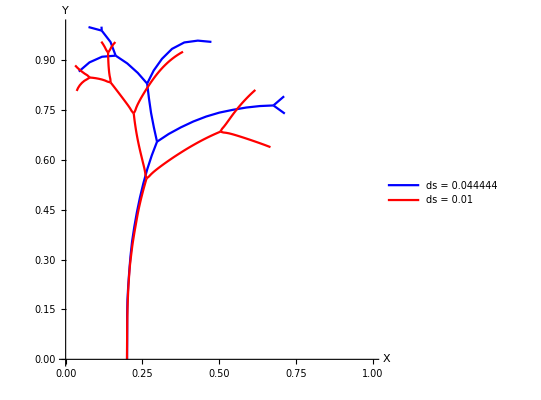

```mathematica
Show[MapThread[plotSimData[#1, #2, #3]&,{{data1, data2},{Blue, Red},{"ds = 0.044444","ds = 0.01"}}]]
```

### This is GUI interface for simulation and its data

```mathematica
Manipulate[
plotSimData@
RunSimulation[n, ModelJSONStructure["ds"->ds, "dx"->0.4], outputname],
{ds, 0.001, 0.1},
{n,3,150,10},
{outputname, "simdata"}
]
```

# Comparing results with analytical solution

```mathematica
cc[z_,a0_]:=-Sqrt[Cos[Pi z/2]]/Sin[Pi*a0/2]-EllipticF[Pi*z/4,2];
solvak[a0_,t_,gamma_]:=ⅇ^((-π^2 t)/8)((cc[gamma,a0]+EllipticF[1/2 ArcSin[ⅇ^(-(π^2 t)/8) Sin[(a0 π)/2]],2]) Sin[(a0 π)/2])/((1-ⅇ^(-(π^2 t)/4) Sin[(a0 π)/2]^2)^(1/4));
krzy[t_]:=FindRoot[solvak[0.5,t,gamma]==-1,{gamma,0.01+0.48*I}][[1,2]];
```

```mathematica
testGrowthPlot = ListPlot[
Table[
{-Re[krzy[t]]*0.5+0.5,0.5*Im[krzy[t]]},
{t,0,4.69,.01}],
Joined->True,
AspectRatio->0.4,
PlotStyle->{Red},
PlotRange->{{0.25,0.5},{0,4}}]//Quiet;
```

```mathematica
testsimdata = RunSimulation[600, ModelJSONStructure["dx"->0.25, "biffurcationType"->3, "fieldValue"->0, "boundaryCondition"->1(*Laplacea*), "width"->1, "height"->30]];
```

```mathematica
sim=plotJSON[OpenJSONDialog[]];
Show[testGrowthPlot, sim]
```

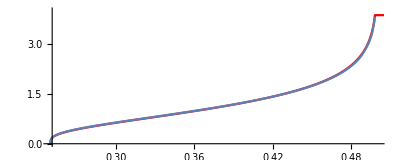

# Biffurcation test

Test data

```mathematica
biffurcationTestCoords={{2.73823*^-19,0.0044721},{2.7607*^-19,0.00453847},{-4.81269*^-19,0.00460533},{-4.1163*^-19,0.00467269},{1.36899*^-19,0.00474054},{1.3685*^-19,0.00480889},{-4.11264*^-19,0.00487773},{-1.41494*^-19,0.00494706},{-8.28414*^-19,0.00501689},{4.14948*^-19,0.00508722},{-2.57979*^-21,0.00515804},{2.75715*^-19,0.00522936},{-2.72556*^-21,0.00530117},{-5.49505*^-19,0.00537347},{5.54046*^-19,0.00544627},{-2.70731*^-19,0.00551957},{-2.81562*^-19,0.00559336},{-3.11721*^-21,0.00566764},{5.53983*^-19,0.00574242},{-3.28523*^-21,0.0058177},{-3.37177*^-21,0.00589347},{-2.82151*^-19,0.00596974},{8.32624*^-19,0.0060465},{-8.26711*^-19,0.00612376},{-3.73524*^-21,0.00620151},{-3.83057*^-21,0.00627975},{2.74933*^-19,0.0063585},{8.32661*^-19,0.00643773},{-4.12759*^-21,0.00651747},{-4.23037*^-21,0.0065977},{-8.25619*^-19,0.00667842},{2.75371*^-18,0.00675964},{-3.32042*^-18,0.00684135},{-1.66241*^-18,0.00692356},{-1.66233*^-18,0.00700627},{-4.88828*^-21,0.00708947},{-2.20245*^-18,0.00717317},{-1.66207*^-18,0.00725736},{-5.24486*^-21,0.00734205},{1.11195*^-18,0.00742723},{3.30707*^-18,0.00751291},{-5.62079*^-21,0.00759909},{-5.43784*^-19,0.00768576},{-5.88249*^-21,0.00777292},{-1.10228*^-18,0.00786058},{1.64889*^-18,0.00794874},{2.20767*^-18,0.0080374},{-6.43346*^-21,0.00812655},{-1.10143*^-18,0.00821619},{2.20662*^-18,0.00830633},{-5.41464*^-19,0.00839697},{-5.41148*^-19,0.0084881},{5.52496*^-19,0.00857973},{-5.40497*^-19,0.00867186},{-2.75234*^-18,0.00876448},{-3.87157*^-18,0.00885759},{-2.75113*^-18,0.0089512},{5.53494*^-18,0.00904531},{-5.38758*^-19,0.00913992},{3.85305*^-18,0.00923502},{1.11217*^-18,0.00933061},{-1.09805*^-18,0.00942671},{2.20104*^-18,0.0095233},{-1.09744*^-18,0.00962038},{3.32137*^-18,0.00971796},{-5.51462*^-18,0.00981604},{4.40752*^-18,0.00991461},{4.40662*^-18,0.0100137},{5.51027*^-19,0.0101132},{7.73443*^-18,0.0102133},{-1.04846*^-17,0.0103139},{-1.09472*^-18,0.0104149},{-1.65573*^-18,0.0105165},{-1.10269*^-20,0.0106185},{3.87889*^-18,0.0107211},{6.64519*^-18,0.0108241},{-1.16839*^-20,0.0109276},{-1.09239*^-18,0.0110317},{-4.4195*^-18,0.0111362},{1.11166*^-18,0.0112412},{-3.29384*^-18,0.0113467},{-1.28443*^-20,0.0114528},{-4.41655*^-18,0.0115593},{-4.41577*^-18,0.0116663},{4.43706*^-18,0.0117738},{2.18633*^-18,0.0118818},{-1.40901*^-20,0.0119903},{-8.8106*^-18,0.0120993},{3.30962*^-18,0.0122088},{-1.08686*^-18,0.0123188},{3.3083*^-18,0.0124292},{-4.40887*^-18,0.0125402},{-1.54454*^-17,0.0126517},{-2.21147*^-18,0.0127637},{-4.40596*^-18,0.0128761},{-1.08363*^-18,0.0129891},{-3.33771*^-18,0.0131026},{3.30323*^-18,0.0132165},{8.8145*^-18,0.013331},{-7.72009*^-18,0.0134459},{-1.80687*^-20,0.0135614},{8.80838*^-18,0.0136773},{1.10634*^-17,0.0137938},{4.42702*^-18,0.0139107},{-2.20712*^-18,0.0140282},{-1.96783*^-20,0.0141461},{-6.65117*^-18,0.0142645},{4.42423*^-18,0.0143834},{1.10522*^-17,0.0145029},{-2.10426*^-20,0.0146228},{6.60484*^-18,0.0147432},{-2.20377*^-18,0.0148641},{-7.6962*^-18,0.0149855},{2.23928*^-18,0.0151074},{-1.10024*^-17,0.0152298},{2.23941*^-18,0.0153527},{-2.20109*^-18,0.0154761},{-2.39856*^-20,0.0156},{1.10302*^-17,0.0157244},{2.23963*^-18,0.0158493},{-3.33117*^-18,0.0159747},{-1.06549*^-18,0.0161006},{-2.59775*^-20,0.0162269},{1.32837*^-17,0.0163538},{-9.93507*^-18,0.0164812},{-2.19558*^-18,0.016609},{6.57441*^-18,0.0167374},{-2.19424*^-18,0.0168663},{-9.9263*^-18,0.0169956},{7.70218*^-18,0.0171255},{-2.19213*^-18,0.0172558},{-1.10542*^-17,0.0173867},{2.31482*^-17,0.017518},{-3.30877*^-17,0.0176499},{-1.10475*^-17,0.0177822},{1.21175*^-17,0.017915},{-1.21789*^-17,0.0180484},{-1.54672*^-17,0.0181822},{3.25616*^-18,0.0183165},{-5.47344*^-18,0.0184513},{6.66421*^-18,0.0185867},{1.10867*^-17,0.0187225},{-5.46753*^-18,0.0188588},{-2.10059*^-17,0.0189956},{-1.21602*^-17,0.0191329},{-9.88105*^-18,0.0192707},{-5.45921*^-18,0.019409},{3.37849*^-18,0.0195478},{2.23965*^-18,0.0196871},{9.9318*^-18,0.0198269},{-5.45036*^-18,0.0199672},{9.927*^-18,0.020108},{9.92453*^-18,0.0202492},{-8.86429*^-18,0.020391},{-1.76834*^-17,0.0205333},{1.10577*^-17,0.0206761},{4.36504*^-18,0.0208193},{2.21494*^-17,0.0209631},{-1.09784*^-17,0.0211073},{1.54524*^-17,0.0212521},{1.31644*^-17,0.0213974},{1.54448*^-17,0.0215431},{4.35399*^-18,0.0216894},{-2.16117*^-18,0.0218361},{-8.8445*^-18,0.0219834},{-2.15878*^-18,0.0221311},{3.08984*^-17,0.0222793},{4.34403*^-18,0.0224281},{-4.85551*^-17,0.0225773},{1.98028*^-17,0.022727},{2.20864*^-17,0.0228772},{1.54025*^-17,0.023028},{1.33015*^-17,0.0231792},{6.6223*^-18,0.0233309},{-2.42663*^-17,0.0234831},{2.23651*^-18,0.0236358},{8.90992*^-18,0.023789},{2.43396*^-17,0.0239427},{1.0991*^-17,0.0240969},{2.43283*^-17,0.0242516},{3.74453*^-17,0.0244068},{-6.02969*^-20,0.0245625},{1.09768*^-17,0.0247187},{-1.10968*^-17,0.0248754},{1.09693*^-17,0.0250326},{-1.5458*^-17,0.0251902},{4.29943*^-18,0.0253484},{4.29676*^-18,0.0255071},{3.09325*^-17,0.0256663},{8.89166*^-18,0.0258259},{-2.43947*^-17,0.0259861},{-6.84937*^-20,0.0261467},{-3.97431*^-17,0.0263079},{-3.30795*^-17,0.0264695},{-4.63727*^-17,0.0266317},{2.21814*^-17,0.0267943},{-2.1128*^-18,0.0269575},{3.75028*^-17,0.0271211},{8.87609*^-18,0.0272853},{-7.56438*^-20,0.0274499},{-2.10553*^-18,0.027615},{-2.10365*^-18,0.0277807},{6.5605*^-18,0.0279468},{3.7436*^-17,0.0281134},{-8.03943*^-20,0.0282805},{-8.72985*^-18,0.0284481},{-4.40424*^-18,0.0286162},{-1.33441*^-17,0.0287848},{-6.71293*^-18,0.0289539},{-8.53701*^-20,0.0291235},{6.5385*^-18,0.0292936},{8.84893*^-18,0.0294642},{6.53263*^-18,0.0296353},{-4.39408*^-18,0.0298069},{-8.69452*^-18,0.029979},{2.63691*^-17,0.0301516},{1.11534*^-17,0.0303247},{-4.40545*^-17,0.0304982},{-1.3313*^-17,0.0306723},{1.77545*^-17,0.0308469},{-1.75924*^-17,0.0310219},{2.86317*^-17,0.0311975},{2.63021*^-17,0.0313736},{-2.41722*^-17,0.0315501},{2.86033*^-17,0.0317272},{-1.09678*^-17,0.0319047},{-4.37243*^-18,0.0320828},{1.5396*^-17,0.0322613},{-1.06467*^-19,0.0324403},{-2.64439*^-17,0.0326199},{-4.365*^-18,0.0327999},{-4.36308*^-18,0.0329804},{-2.03432*^-18,0.0331615},{-2.64087*^-17,0.033343},{3.54844*^-17,0.033525},{-3.9528*^-17,0.0337075},{9.26542*^-17,0.0338905},{2.65631*^-17,0.034074},{2.21177*^-18,0.034258},{8.76909*^-18,0.0344425},{-2.44516*^-17,0.0346275},{-4.41028*^-17,0.034813},{-2.63223*^-17,0.034999},{-3.75271*^-17,0.0351855},{-1.55494*^-17,0.0353725},{1.34189*^-17,0.03556},{3.30296*^-17,0.035748},{3.30181*^-17,0.0359364},{-3.09343*^-17,0.0361254},{-3.51147*^-17,0.0363149},{3.29826*^-17,0.0365048},{-2.43829*^-17,0.0366953},{6.38024*^-18,0.0368862},{-2.2028*^-17,0.0370777},{2.87627*^-17,0.0372696},{-2.20124*^-17,0.0374621},{6.36093*^-18,0.037655},{-1.08063*^-17,0.0378485},{-1.3145*^-17,0.0380424},{5.05488*^-17,0.0382368},{-3.73012*^-17,0.0384317},{-5.7303*^-17,0.0386272},{-2.43024*^-17,0.0388231},{-6.37432*^-17,0.0390195},{-2.84144*^-17,0.0392164},{-1.31054*^-17,0.0394138},{-1.92898*^-18,0.0396117},{1.98229*^-17,0.0398101},{-1.77914*^-17,0.040009},{-1.30813*^-17,0.0402084},{-1.7782*^-17,0.0404083},{-4.41897*^-17,0.0406087},{-2.65732*^-17,0.0408095},{6.14102*^-17,0.0410109},{8.61997*^-18,0.0412128},{4.37777*^-17,0.0414152},{-8.96499*^-18,0.041618},{2.61718*^-17,0.0418214},{-3.05833*^-17,0.0420252},{8.59347*^-18,0.0422296},{2.20829*^-17,0.0424344},{-7.50648*^-17,0.0426398},{3.5558*^-17,0.0428456},{4.5359*^-18,0.043052},{1.32936*^-17,0.0432588},{-3.99407*^-17,0.0434661},{9.67687*^-17,0.0436739},{1.32807*^-17,0.0438823},{-4.20836*^-18,0.0440911},{1.72744*^-17,0.0443004},{-2.64069*^-17,0.0445102},{3.07231*^-17,0.0447205},{1.32582*^-17,0.0449313},{7.0326*^-17,0.0451426},{2.67099*^-17,0.0453544},{1.79892*^-17,0.0455667},{-4.17842*^-18,0.0457794},{3.53914*^-17,0.0459927},{-7.457*^-17,0.0462065},{-1.76136*^-17,0.0464208},{3.06009*^-17,0.0466355},{4.52775*^-18,0.0468508},{-2.29213*^-19,0.0470665},{5.74272*^-17,0.0472828},{-4.14613*^-18,0.0474995},{-1.28093*^-17,0.0477168},{-1.28002*^-17,0.0479345},{8.41729*^-18,0.0481527},{-2.42583*^-19,0.0483715},{-7.89617*^-17,0.0485907},{-2.47172*^-19,0.0488104},{4.52161*^-18,0.0490306},{5.24553*^-17,0.0492513},{-3.9537*^-17,0.0494725},{-3.08981*^-17,0.0496942},{-8.87545*^-18,0.0499164},{-1.74836*^-17,0.0501391},{-2.63765*^-19,0.0503623},{3.98828*^-17,0.050586},{7.90319*^-17,0.0508102},{-7.47531*^-17,0.0510348},{-8.85706*^-18,0.05126},{1.40973*^-16,0.0514857},{5.31741*^-17,0.0517118},{1.78708*^-17,0.0519385},{-1.31775*^-16,0.0521656},{-4.04432*^-18,0.0523933},{7.01935*^-17,0.0526214},{-9.2629*^-17,0.05285},{4.45205*^-17,0.0530791},{-4.40235*^-17,0.0533088},{-8.82335*^-18,0.0535389},{4.44773*^-17,0.0537695},{-7.91172*^-17,0.0540006},{-3.91371*^-17,0.0542322},{2.14982*^-17,0.0544643},{-2.21105*^-17,0.0546969},{-3.54027*^-17,0.05493},{3.95688*^-17,0.0551636},{-3.05563*^-17,0.0553976},{9.31721*^-18,0.0556322},{3.10571*^-17,0.0558673},{1.29456*^-17,0.0561028},{-3.53188*^-17,0.0563389},{-8.83658*^-17,0.0565754},{-2.20294*^-17,0.0568125},{1.77444*^-17,0.05705},{5.74859*^-17,0.057288},{-3.4793*^-19,0.0575265},{9.32307*^-18,0.0577656},{-2.19808*^-17,0.0580051},{-7.48794*^-17,0.0582451},{3.09252*^-17,0.0584856},{4.41281*^-17,0.0587266},{-4.35135*^-17,0.0589681},{1.14958*^-16,0.0592101},{-8.3059*^-17,0.0594525},{-7.95278*^-17,0.0596955},{3.56998*^-17,0.059939},{-5.65703*^-17,0.0601829},{-1.35591*^-17,0.0604274},{-3.01724*^-17,0.0606723},{-4.81748*^-17,0.0609178},{-1.355*^-17,0.0611637},{4.46594*^-18,0.0614102},{-1.69519*^-17,0.0616571},{5.2134*^-17,0.0619045},{-9.7177*^-17,0.0621524},{2.58305*^-17,0.0624008},{-6.1115*^-17,0.0626497},{1.14195*^-16,0.0628991},{3.88797*^-17,0.063149},{6.99228*^-17,0.0633994},{3.88303*^-17,0.0636503},{1.26461*^-17,0.0639016},{-9.68294*^-17,0.0641535},{-3.73032*^-18,0.0644058},{-4.44345*^-19,0.0646587},{-8.60665*^-18,0.064912},{9.24856*^-17,0.0651659},{4.35457*^-17,0.0654202},{-5.74667*^-17,0.065675},{-7.04613*^-17,0.0659303},{7.92976*^-17,0.0661861},{-4.43862*^-17,0.0664424},{4.8325*^-17,0.0666992},{-6.54189*^-17,0.0669565},{-7.83624*^-17,0.0672143},{9.20794*^-17,0.0674726},{4.01774*^-17,0.0677313},{-1.26922*^-16,0.0679906},{-1.13908*^-16,0.0682503},{-1.36625*^-16,0.0685106},{-1.107*^-16,0.0687713},{1.04709*^-16,0.0690326},{7.38995*^-17,0.0692943},{4.40939*^-18,0.0695565},{2.22316*^-17,0.0698192},{9.33669*^-18,0.0700824},{3.50904*^-17,0.0703461},{-4.40737*^-17,0.0706103},{3.01159*^-17,0.070875},{7.55527*^-17,0.0711401},{-1.13151*^-16,0.0714058},{-5.1874*^-17,0.071672},{3.99236*^-17,0.0719386},{-4.39428*^-17,0.0722058},{-6.1672*^-17,0.0724734},{1.2364*^-16,0.0727415},{-8.7175*^-17,0.0730101},{-8.39409*^-18,0.0732792},{1.21794*^-17,0.0735488},{1.7937*^-16,0.0738189},{3.48172*^-17,0.0740895},{1.28243*^-16,0.0743606},{-1.19451*^-16,0.0746322},{5.74027*^-17,0.0749042},{3.97036*^-17,0.0751768},{-6.15003*^-19,0.0754498},{-9.65948*^-17,0.0757234},{1.70212*^-17,0.0759974},{-1.36745*^-16,0.0762719},{-1.19049*^-16,0.0765469},{1.32663*^-16,0.0768224},{-4.8488*^-17,0.0770984},{-1.01267*^-16,0.0773749},{1.14879*^-16,0.0776519},{9.32679*^-18,0.0779293},{1.22349*^-16,0.0782073},{-8.84876*^-17,0.0784857},{-2.57837*^-17,0.0787647},{1.57223*^-16,0.0790441},{9.32347*^-18,0.079324},{-1.23365*^-16,0.0796045},{-6.94065*^-19,0.0798854},{8.68272*^-17,0.0801668},{-7.81557*^-17,0.0804486},{-9.55907*^-17,0.080731},{-8.8089*^-17,0.0810139},{-8.14649*^-18,0.0812972},{-8.79957*^-17,0.0815811},{-5.30615*^-17,0.0818654},{-1.30147*^-16,0.0821503},{-2.55299*^-17,0.0824356},{-2.55092*^-17,0.0827214},{-7.52909*^-19,0.0830077},{1.31037*^-16,0.0832945},{1.93167*^-16,0.0835818},{-7.69622*^-19,0.0838695},{-1.22265*^-16,0.0841578},{-1.91569*^-16,0.0844466},{-2.63632*^-16,0.0847358},{5.11713*^-17,0.0850255},{-2.28716*^-16,0.0853158},{-9.7399*^-17,0.0856065},{-2.70208*^-16,0.0858977},{-7.9737*^-18,0.0861894},{-6.27271*^-17,0.0864815},{1.74668*^-16,0.0867742},{7.11376*^-17,0.0870674},{-1.80642*^-17,0.087361},{1.63668*^-17,0.0876552},{-5.24505*^-17,0.0879498},{-1.82875*^-16,0.0882449},{-1.4841*^-16,0.0885405},{-3.51922*^-17,0.0888366},{-9.67793*^-17,0.0891332},{7.78248*^-17,0.0894303},{-1.13791*^-16,0.0897278},{6.06069*^-17,0.0900259},{-4.52727*^-17,0.0903244},{-6.2338*^-17,0.0906235},{-1.79817*^-17,0.090923},{2.27455*^-16,0.091223},{2.63136*^-17,0.0915235},{1.38659*^-16,0.0918245},{-6.8987*^-17,0.0921259},{-5.19391*^-17,0.0924279},{3.04894*^-16,0.0927303},{-1.29965*^-16,0.0930333},{-7.90129*^-17,0.0933367},{-8.56702*^-17,0.0936406},{-1.56856*^-16,0.093945},{2.19332*^-16,0.0942499},{-6.85721*^-17,0.0945553},{1.20784*^-16,0.0948612},{2.61156*^-17,0.0951675},{3.74112*^-16,0.0954744},{-1.49662*^-16,0.0957817},{-4.803*^-16,0.0960895},{-6.17205*^-17,0.0963978},{-1.49397*^-16,0.0967066},{-4.48793*^-17,0.0970159},{1.57396*^-16,0.0973256},{5.30089*^-17,0.0976359},{-5.12355*^-17,0.0979466},{-1.07934*^-18,0.0982579},{-1.48846*^-16,0.0985696},{-7.44602*^-18,0.0988818},{2.17066*^-16,0.0991945},{-2.3577*^-16,0.0995077},{2.70671*^-16,0.0998213},{2.10343*^-16,0.100135},{-1.75198*^-16,0.10045},{-1.21249*^-16,0.100765},{1.72679*^-16,0.101081},{-5.07538*^-17,0.101397},{-1.6438*^-16,0.101714},{-1.17038*^-18,0.102031},{-6.0991*^-17,0.102348},{-7.741*^-17,0.102666},{1.65833*^-16,0.102985},{-1.47343*^-16,0.103304},{8.52037*^-17,0.103623},{6.27601*^-17,0.103943},{2.68032*^-16,0.104264},{7.90477*^-17,0.104585},{-1.3047*^-16,0.104906},{8.93701*^-17,0.105228},{-2.86031*^-16,0.10555},{1.95994*^-17,0.105873},{-2.4267*^-16,0.106197},{2.34136*^-16,0.106521},{1.9606*^-17,0.106845},{3.13729*^-16,0.10717},{-2.36237*^-16,0.107495},{-6.02345*^-17,0.107821},{5.1874*^-17,0.108147},{3.02366*^-16,0.108474},{2.86047*^-16,0.108801},{-2.79071*^-17,0.109129},{8.87452*^-17,0.109457},{3.11927*^-16,0.109786},{-1.97925*^-16,0.110115},{1.96286*^-17,0.110445},{-1.39762*^-18,0.110775},{-2.50362*^-16,0.111106},{-1.02046*^-16,0.111437},{7.78481*^-17,0.111768},{-2.78416*^-17,0.1121},{-8.06149*^-17,0.112433},{-2.86293*^-16,0.112766},{-2.86079*^-16,0.1131},{2.88256*^-16,0.113434},{6.69195*^-17,0.113768},{1.56332*^-16,0.114103},{5.10719*^-17,0.114439},{1.1925*^-16,0.114775},{2.76643*^-16,0.115111},{2.4703*^-17,0.115448},{2.76209*^-16,0.115785},{-1.74308*^-16,0.116123},{-1.89749*^-16,0.116462},{-1.37282*^-16,0.116801},{-1.73925*^-16,0.11714},{-1.5876*^-18,0.11748},{1.39532*^-16,0.11782},{2.69832*^-16,0.118161},{3.89294*^-16,0.118502},{4.10284*^-16,0.118844},{7.64253*^-17,0.119186},{8.70146*^-17,0.119529},{-1.31564*^-16,0.119872},{3.49626*^-17,0.120216},{1.79902*^-16,0.12056},{-8.40027*^-17,0.120905},{1.12583*^-16,0.12125},{1.53555*^-16,0.121595},{-1.72178*^-18,0.121941},{2.52198*^-16,0.122288},{-2.75572*^-17,0.122635},{7.1266*^-17,0.122983},{-2.75355*^-17,0.123331},{7.11804*^-17,0.123679},{2.14762*^-16,0.124028},{-1.70988*^-16,0.124378},{-8.96019*^-17,0.124728},{1.6289*^-16,0.125078},{-1.6641*^-16,0.125429},{-9.35329*^-17,0.12578},{-6.78552*^-17,0.126132},{-2.02391*^-16,0.126484},{-1.80686*^-16,0.126837},{-1.88772*^-18,0.127191},{7.45916*^-17,0.127544},{7.45083*^-17,0.127899},{3.9759*^-16,0.128253},{1.83053*^-16,0.128609},{2.84514*^-16,0.128964},{-2.26613*^-16,0.12932},{1.97149*^-16,0.129677},{5.29747*^-16,0.130034},{1.10054*^-16,0.130392},{-2.51185*^-16,0.13075},{-1.7523*^-16,0.131108},{-1.751*^-16,0.131467},{-3.81081*^-17,0.131827},{-3.47623*^-16,0.132187},{-2.61026*^-16,0.132547},{-7.74397*^-17,0.132908},{3.3895*^-17,0.13327},{-6.31362*^-17,0.133632},{-2.71097*^-16,0.133994},{-6.62575*^-17,0.134357},{2.16428*^-16,0.13472},{5.86862*^-17,0.135084},{2.87788*^-16,0.135448},{-6.29217*^-17,0.135813},{-1.01693*^-16,0.136179},{-6.5798*^-17,0.136544},{-2.19767*^-16,0.13691},{-3.40687*^-16,0.137277},{8.01794*^-17,0.137644},{3.85104*^-16,0.138012},{2.85937*^-16,0.13838},{-2.18947*^-16,0.138749},{1.96872*^-17,0.139118},{6.89158*^-17,0.139487},{-5.14946*^-17,0.139857},{4.15978*^-16,0.140228},{-1.58585*^-17,0.140599},{-3.26922*^-16,0.14097},{-4.0865*^-16,0.141342},{-3.78637*^-17,0.141714},{2.12577*^-16,0.142087},{-9.76325*^-17,0.142461},{6.17017*^-16,0.142834},{-7.537*^-17,0.143209},{-2.67389*^-17,0.143584},{-3.98871*^-17,0.143959},{4.69451*^-16,0.144334},{4.93238*^-16,0.144711},{-3.7763*^-17,0.145087},{-2.99173*^-16,0.145464},{-4.52613*^-16,0.145842},{-9.87484*^-17,0.14622},{2.14323*^-17,0.146599},{-4.14478*^-16,0.146978},{-5.08217*^-16,0.147357},{-4.13742*^-16,0.147737},{-4.1337*^-16,0.148118},{-3.91814*^-17,0.148499},{-4.12618*^-16,0.14888},{-2.71042*^-16,0.149262},{-3.53206*^-16,0.149644},{-1.78468*^-16,0.150027},{-2.70378*^-16,0.15041},{-3.52237*^-16,0.150794},{-9.5947*^-17,0.151178},{-4.9891*^-17,0.151563},{-2.47037*^-16,0.151948},{-2.80912*^-18,0.152334},{-1.53747*^-16,0.15272},{-2.45363*^-16,0.153106},{4.35899*^-16,0.153494},{-3.14133*^-16,0.153881},{-3.83758*^-16,0.154269},{-4.98209*^-16,0.154658},{5.41116*^-17,0.155046},{8.85363*^-17,0.155436},{-1.06807*^-16,0.155826},{1.45901*^-16,0.156216},{1.33997*^-16,0.156607},{-7.20763*^-17,0.156998},{1.96048*^-17,0.15739},{2.93715*^-16,0.157782},{3.39254*^-16,0.158175},{-2.08256*^-16,0.158568},{1.22084*^-16,0.158962},{-3.10551*^-18,0.159356},{-2.87273*^-16,0.15975},{-2.52906*^-16,0.160145},{-3.15728*^-18,0.160541},{9.88005*^-17,0.160937},{-7.11055*^-17,0.161333},{-5.79873*^-16,0.16173},{-1.15976*^-16,0.162128},{-8.19864*^-17,0.162526},{-1.04705*^-16,0.162924},{1.2089*^-16,0.163323},{-3.70401*^-17,0.163722},{-3.3168*^-18,0.164122},{-1.15125*^-16,0.164522},{6.39078*^-17,0.164923},{3.02216*^-17,0.165324},{-4.75767*^-17,0.165725},{-1.39874*^-17,0.166127},{-4.74325*^-17,0.16653},{3.53931*^-16,0.166933},{-4.72867*^-17,0.167336},{2.98805*^-17,0.16774},{3.19427*^-16,0.168145},{-3.68054*^-17,0.168549},{2.97056*^-17,0.168955},{-8.01195*^-17,0.169361},{2.51648*^-16,0.169767},{-1.69221*^-16,0.170174},{-3.61651*^-18,0.170581},{-3.01025*^-16,0.170988},{-1.35287*^-17,0.171396},{-7.55464*^-16,0.171805},{-1.34552*^-17,0.172214},{5.23361*^-17,0.172624},{3.05322*^-16,0.173034},{-1.58128*^-16,0.173444},{-2.33023*^-16,0.173855},{-5.3139*^-16,0.174266},{3.59903*^-16,0.174678},{-2.55439*^-16,0.17509},{-4.08753*^-16,0.175503},{4.47155*^-16,0.175916},{-1.66337*^-16,0.17633},{-3.63606*^-17,0.176744},{-3.63365*^-17,0.177159},{2.9258*^-16,0.177574},{-1.00904*^-16,0.177989},{2.27467*^-16,0.178405},{4.20563*^-16,0.178822},{5.40007*^-16,0.179239},{-6.76021*^-16,0.179656},{2.67348*^-16,0.180074},{-2.43212*^-16,0.180492},{-6.09766*^-16,0.180911},{2.02512*^-16,0.18133},{-1.55231*^-16,0.18175},{3.44617*^-16,0.18217},{-4.21572*^-18,0.182591},{1.14544*^-16,0.183012},{2.74336*^-17,0.183433},{-1.30859*^-16,0.183855},{-1.2269*^-16,0.184278},{-4.32674*^-18,0.1847},{2.71454*^-17,0.185124},{-2.4813*^-16,0.185548},{-6.878*^-16,0.185972},{4.35071*^-16,0.186397},{-1.20352*^-17,0.186822},{2.30399*^-16,0.187247},{-3.56359*^-16,0.187674},{-2.07675*^-16,0.1881},{-1.52625*^-16,0.188527},{2.64743*^-17,0.188955},{5.01895*^-17,0.189383},{-2.13954*^-16,0.189811},{-4.62661*^-18,0.19024},{1.04662*^-16,0.190669},{-2.36957*^-16,0.191099},{-2.05979*^-16,0.191529},{7.37065*^-17,0.19196},{-1.51039*^-16,0.192391},{-1.74778*^-16,0.192823},{-4.79496*^-18,0.193255},{6.49727*^-16,0.193687},{-1.26337*^-16,0.19412},{3.03289*^-16,0.194553},{3.3319*^-16,0.194987},{-8.01106*^-16,0.195422},{3.3235*^-16,0.195856},{-1.79451*^-16,0.196292},{-5.93858*^-16,0.196727},{-6.49572*^-17,0.197163},{-1.48786*^-16,0.1976},{-2.86378*^-16,0.198037},{-5.37185*^-16,0.198475},{-3.45154*^-16,0.198913},{-2.31507*^-16,0.199351},{1.61637*^-16,0.19979},{6.85397*^-16,0.200229},{-2.25317*^-16,0.200669},{-1.76618*^-16,0.201109},{-5.88927*^-17,0.20155},{-1.17478*^-16,0.201991},{-1.70858*^-16,0.202433},{1.01599*^-16,0.202875},{-2.53019*^-16,0.203317},{-1.7028*^-16,0.20376},{-4.12423*^-16,0.204203},{-2.2318*^-16,0.204647},{-4.11521*^-16,0.205091},{2.60456*^-16,0.205536},{7.63269*^-17,0.205981},{-9.79796*^-18,0.206427},{7.60425*^-17,0.206873},{2.06371*^-16,0.20732},{-3.5977*^-16,0.207767},{-1.96672*^-16,0.208214},{-9.51781*^-18,0.208662},{-5.93981*^-16,0.20911},{-3.39617*^-17,0.209559},{-2.72837*^-16,0.210008},{-9.28886*^-18,0.210458},{1.79914*^-16,0.210908},{-1.42174*^-16,0.211359},{-3.76546*^-16,0.21181},{2.03807*^-16,0.212261},{-1.90829*^-16,0.212713},{-6.39844*^-16,0.213166},{-8.7572*^-16,0.213618},{-1.92977*^-16,0.214072},{4.13926*^-16,0.214525},{-2.41919*^-16,0.214979},{5.93767*^-16,0.215434},{1.4983*^-16,0.215889},{7.0559*^-17,0.216345},{9.32224*^-16,0.216801},{7.25427*^-17,0.217257},{-1.11884*^-16,0.217714},{9.71099*^-17,0.218171},{-1.63192*^-16,0.218629},{-7.59033*^-16,0.219087},{8.46575*^-16,0.219545},{1.72973*^-16,0.220005},{6.38572*^-16,0.220464},{9.62224*^-17,0.220924},{4.81532*^-16,0.221384},{-5.78293*^-17,0.221845},{2.49335*^-16,0.222306},{-1.86084*^-16,0.222768},{3.75887*^-16,0.22323},{9.53046*^-17,0.223693},{-4.65924*^-16,0.224156},{1.83741*^-17,0.224619},{-5.91469*^-16,0.225083},{-3.37338*^-16,0.225548},{-2.85825*^-16,0.226012},{-2.60238*^-16,0.226478},{-4.11544*^-16,0.226943},{-5.74684*^-17,0.22741},{8.50403*^-16,0.227876},{-4.35074*^-16,0.228343},{3.19753*^-16,0.228811},{8.46957*^-16,0.229278},{-6.5885*^-16,0.229747},{2.68726*^-16,0.230216},{3.438*^-16,0.230685},{-1.05663*^-15,0.231154},{-8.0572*^-16,0.231624},{8.90769*^-16,0.232095},{1.28658*^-15,0.232566},{-6.53435*^-16,0.233037},{-1.54921*^-16,0.233509},{6.38283*^-16,0.233981},{4.39493*^-16,0.234454},{4.37235*^-16,0.234927},{5.35251*^-16,0.235401},{-9.67474*^-16,0.235875},{4.1161*^-16,0.236349},{1.39733*^-16,0.236824},{1.16073*^-16,0.2373},{-7.42493*^-16,0.237775},{9.00563*^-17,0.238252},{-5.66385*^-17,0.238728},{4.36189*^-17,0.239205},{6.27876*^-16,0.239683},{-7.9113*^-18,0.240161},{-5.41858*^-16,0.240639},{1.14743*^-16,0.241118},{1.40398*^-16,0.241597},{-5.29863*^-17,0.242077},{-3.04637*^-17,0.242557},{8.8172*^-17,0.243037},{9.17097*^-17,0.243518},{1.13706*^-16,0.244},{-5.21987*^-17,0.244482},{1.13353*^-16,0.244964},{3.94343*^-17,0.245447},{4.36403*^-17,0.24593},{3.91964*^-17,0.246413},{6.51179*^-17,0.246897},{-2.45656*^-16,0.247382},{-1.24498*^-16,0.247867},{-5.08982*^-17,0.248352},{-4.8048*^-16,0.248838},{-3.45997*^-18,0.249324},{-2.17622*^-16,0.24981},{-8.17498*^-16,0.250297},{-2.94075*^-17,0.250785},{-5.02694*^-16,0.251273},{-5.74823*^-16,0.251761},{2.03771*^-16,0.25225},{-6.9239*^-16,0.252739},{6.73449*^-16,0.253228},{4.2064*^-16,0.253718},{7.43804*^-16,0.254209},{-3.84925*^-16,0.2547},{4.12215*^-16,0.255191},{2.27572*^-16,0.255683},{-1.92775*^-16,0.256175},{-3.10506*^-16,0.256667},{-2.90778*^-16,0.25716},{-2.44785*^-16,0.257654},{1.53722*^-16,0.258148},{4.0714*^-16,0.258642},{-5.61351*^-16,0.259137},{-2.81016*^-16,0.259632},{-4.23994*^-16,0.260127},{1.60372*^-16,0.260623},{-2.61115*^-16,0.26112},{-5.38388*^-16,0.261616},{1.51299*^-16,0.262114},{2.22367*^-16,0.262611},{-1.61448*^-16,0.263109},{-9.88326*^-17,0.263608},{4.25537*^-16,0.264107},{-3.02498*^-16,0.264606},{-1.01055*^-15,0.265106},{-2.3053*^-16,0.265606},{-5.03766*^-16,0.266107},{-1.01145*^-17,0.266608},{2.72574*^-16,0.267109},{1.57905*^-16,0.267611},{-1.02504*^-17,0.268113},{7.00303*^-16,0.268616},{-1.03418*^-17,0.269119},{1.24962*^-15,0.269623},{1.65751*^-17,0.270127},{-7.48852*^-16,0.270631},{4.68596*^-16,0.271136},{5.64844*^-16,0.271641},{-1.23261*^-16,0.272147},{-1.11553*^-16,0.272653},{-5.32753*^-17,0.273159},{1.01307*^-16,0.273666},{-9.55032*^-17,0.274174},{1.30974*^-18,0.274681},{3.23555*^-16,0.27519},{-3.02802*^-16,0.275698},{1.62674*^-17,0.276207},{5.80437*^-17,0.276717},{-5.78962*^-16,0.277226},{-3.56884*^-16,0.277737},{-1.77075*^-16,0.278247},{9.24258*^-16,0.278758},{2.77132*^-16,0.27927},{8.66146*^-16,0.279782},{6.59361*^-16,0.280294},{-4.35102*^-16,0.280807},{-1.88837*^-16,0.28132},{-5.83347*^-16,0.281833},{-7.3158*^-16,0.282347},{4.49667*^-16,0.282862},{5.31523*^-16,0.283376},{-3.2318*^-16,0.283892},{-2.55019*^-16,0.284407},{-9.67794*^-16,0.284923},{4.20877*^-16,0.28544},{-1.19103*^-16,0.285957},{-4.39742*^-16,0.286474},{2.96336*^-16,0.286991},{-2.52854*^-16,0.28751},{-5.04282*^-16,0.288028},{-6.76323*^-16,0.288547},{8.28653*^-16,0.289066},{5.60364*^-16,0.289586},{-7.94869*^-16,0.290106},{-1.24231*^-17,0.290627},{-2.50237*^-16,0.291147},{-1.47486*^-15,0.291669},{3.84689*^-16,0.292191},{-1.26382*^-17,0.292713},{-6.92701*^-16,0.293235},{-6.25501*^-16,0.293758},{-5.76875*^-16,0.294282},{-7.0732*^-16,0.294805},{-3.78282*^-16,0.29533},{-7.88944*^-16,0.295854},{6.03388*^-16,0.296379},{-3.11178*^-16,0.296905},{7.77363*^-16,0.29743},{-8.7585*^-16,0.297957},{8.83641*^-17,0.298483},{-5.40099*^-16,0.29901},{-6.03806*^-16,0.299538},{-6.31004*^-16,0.300065},{7.3192*^-16,0.300594},{1.07547*^-16,0.301122},{1.43293*^-16,0.301651},{1.23334*^-15,0.302181},{7.87454*^-17,0.302711},{1.55541*^-15,0.303241},{1.77548*^-16,0.303771},{-1.38771*^-17,0.304302},{2.62295*^-16,0.304834},{5.85481*^-16,0.305366},{-8.37189*^-16,0.305898},{9.33871*^-16,0.306431},{-1.40191*^-15,0.306964},{-1.21612*^-15,0.307497},{-4.59663*^-16,0.308031},{-5.16082*^-16,0.308565},{-2.0736*^-16,0.3091},{-2.06881*^-16,0.309635},{-2.01577*^-16,0.31017},{-1.39042*^-16,0.310706},{-4.53828*^-16,0.311242},{-1.47167*^-17,0.311779},{-3.24019*^-16,0.312316},{-1.42238*^-16,0.312853},{-3.88248*^-16,0.313391},{-1.41499*^-16,0.313929},{-7.97893*^-17,0.314468},{-2.01964*^-16,0.315007},{-1.40379*^-16,0.315546},{-1.40003*^-16,0.316086},{-2.00443*^-16,0.316626},{-7.60292*^-17,0.317167},{-1.38861*^-16,0.317708},{-1.54695*^-17,0.318249},{-7.58226*^-17,0.318791},{-1.73942*^-17,0.319333},{-1.72744*^-17,0.319875},{-1.95382*^-16,0.320418},{-1.70331*^-17,0.320962},{-1.58577*^-17,0.321505},{-1.94348*^-16,0.322049},{-7.60042*^-17,0.322594},{-1.65444*^-17,0.323139},{-1.34539*^-16,0.323684},{-1.6297*^-17,0.32423},{-1.61725*^-17,0.324776},{-1.33322*^-16,0.325322},{-4.25853*^-16,0.325869},{-1.64552*^-17,0.326416},{-4.23986*^-16,0.326964},{-9.47728*^-16,0.327512},{-1.66585*^-17,0.32806},{-1.52865*^-17,0.328609},{-1.51578*^-17,0.329158},{-6.51005*^-16,0.329707},{-7.22338*^-17,0.330257},{-7.19555*^-17,0.330808},{-1.9661*^-15,0.331358},{-1.45065*^-17,0.331909},{-7.57646*^-16,0.332461},{2.71734*^-16,0.333013},{-4.15645*^-16,0.333565},{-7.02594*^-17,0.334118},{-6.98364*^-16,0.334671},{-4.69237*^-16,0.335224},{-3.56634*^-16,0.335778},{-1.84709*^-16,0.336332},{-9.14924*^-16,0.336886},{-1.3163*^-17,0.337441},{-4.09206*^-16,0.337996},{-4.63423*^-16,0.338552},{-5.77519*^-16,0.339108},{-2.97281*^-16,0.339665},{-1.8214*^-17,0.340221},{-1.2709*^-16,0.340779},{-2.9573*^-16,0.341336},{-5.7198*^-16,0.341894},{-2.40769*^-16,0.342452},{-5.62907*^-16,0.343011},{-2.86587*^-16,0.34357},{-5.06774*^-16,0.34413},{-7.26068*^-16,0.344689},{-2.92019*^-16,0.34525},{-7.18802*^-17,0.34581},{-6.68337*^-16,0.346371},{-6.66831*^-16,0.346932},{-2.28842*^-16,0.347494},{1.66192*^-15,0.348056},{-4.44948*^-16,0.348619},{-1.75118*^-16,0.349182},{-4.52285*^-16,0.349745},{-6.67357*^-16,0.350308},{-8.71544*^-16,0.350872},{8.4022*^-16,0.351437},{7.87221*^-16,0.352001},{-1.94624*^-15,0.352566},{4.07155*^-16,0.353132},{-9.22868*^-16,0.353698},{4.15237*^-17,0.354264},{-1.18105*^-15,0.354831},{4.14736*^-17,0.355397},{-8.64923*^-16,0.355965},{-2.04476*^-17,0.356532},{4.13971*^-17,0.357101},{-5.51133*^-16,0.357669},{-3.8997*^-16,0.358238},{1.19556*^-15,0.358807},{-1.80342*^-16,0.359376},{-1.17903*^-16,0.359946},{-6.90746*^-16,0.360517},{-7.37216*^-16,0.361087},{2.67315*^-17,0.361658},{-8.91423*^-16,0.36223},{-4.16585*^-16,0.362801},{2.45673*^-16,0.363373},{-9.47461*^-16,0.363946},{-1.71245*^-15,0.364519},{4.00251*^-16,0.365092},{-2.17746*^-17,0.365665},{-1.09437*^-15,0.366239},{-1.09184*^-15,0.366814},{-6.87568*^-16,0.367388},{-4.85766*^-16,0.367963},{1.32004*^-16,0.368539},{1.45325*^-15,0.369114},{-2.23774*^-17,0.369691},{-4.18764*^-16,0.370267},{-2.20151*^-16,0.370844},{-2.264*^-17,0.371421},{-3.26975*^-16,0.371999},{5.40104*^-16,0.372577},{-2.23063*^-15,0.373155},{-1.54236*^-16,0.373733},{-4.55103*^-16,0.374312},{-2.85931*^-15,0.374892},{-2.01613*^-15,0.375472},{-1.96838*^-15,0.376052},{-1.60137*^-15,0.376632},{-1.95905*^-15,0.377213},{-1.06325*^-15,0.377794},{-8.70547*^-16,0.378376},{-8.04537*^-16,0.378957},{-5.90996*^-16,0.37954},{-1.26443*^-15,0.380122},{-1.05065*^-15,0.380705},{-7.55548*^-16,0.381288},{-8.18124*^-16,0.381872},{-3.15389*^-16,0.382456},{-1.14518*^-15,0.38304},{-1.44827*^-16,0.383625},{-1.29134*^-16,0.38421},{-1.68709*^-16,0.384796},{-3.11991*^-16,0.385381},{8.98986*^-16,0.385968},{-2.50254*^-17,0.386554},{-1.28778*^-16,0.387141},{-1.04568*^-15,0.387728},{-6.3595*^-17,0.388316},{-3.07809*^-16,0.388903},{1.01475*^-15,0.389492},{-7.27565*^-16,0.39008},{-2.32133*^-15,0.390669},{-2.58003*^-17,0.391258},{-5.1717*^-16,0.391848},{1.78219*^-16,0.392438},{8.62179*^-16,0.393028},{9.68704*^-16,0.393619},{4.81587*^-16,0.39421},{-1.7015*^-15,0.394802},{2.77158*^-16,0.395393},{-1.32227*^-16,0.395985},{-1.07426*^-15,0.396578},{-8.04452*^-16,0.397171},{6.44995*^-16,0.397764},{-3.3031*^-16,0.398357},{1.21016*^-15,0.398951},{5.72397*^-16,0.399545},{8.04156*^-16,0.40014},{3.04506*^-16,0.400734},{1.59459*^-15,0.40133},{3.02661*^-16,0.401925},{-6.20125*^-16,0.402521},{1.15565*^-15,0.403117},{3.3184*^-16,0.403714},{-5.97559*^-17,0.404311},{1.21341*^-15,0.404908},{-2.86705*^-16,0.405505},{8.47107*^-16,0.406103},{9.78532*^-16,0.406702},{-1.02716*^-15,0.4073},{3.90426*^-16,0.407899},{-8.94755*^-16,0.408498},{-8.54907*^-16,0.409098},{2.90271*^-16,0.409698},{1.24447*^-15,0.410298},{-5.29472*^-16,0.410899},{3.8128*^-17,0.4115},{-1.32073*^-15,0.412101},{1.05614*^-16,0.412703},{-3.03736*^-16,0.413305},{3.78501*^-16,0.413907},{-3.4204*^-16,0.41451},{-7.20342*^-16,0.415113},{-8.34245*^-17,0.415716},{-1.24557*^-16,0.41632},{-2.96926*^-16,0.416924},{-1.66237*^-15,0.417528},{6.7652*^-16,0.418133},{-1.50886*^-15,0.418738},{-2.20778*^-15,0.419343},{-1.2464*^-15,0.419949},{6.67714*^-16,0.420555},{-2.86187*^-15,0.421161},{8.24198*^-16,0.421768},{1.0588*^-16,0.422375},{-9.74257*^-16,0.422982},{2.60577*^-15,0.42359},{9.74844*^-16,0.424198},{-5.10597*^-16,0.424806},{7.18586*^-16,0.425414},{-6.89614*^-16,0.426023},{2.39618*^-16,0.426633},{3.29172*^-16,0.427242},{-1.87689*^-15,0.427852},{-2.92255*^-15,0.428463},{-1.48763*^-15,0.429073},{-5.19972*^-16,0.429684},{-1.85627*^-15,0.430295},{-7.13989*^-16,0.430907},{-7.62021*^-16,0.431519},{-8.67228*^-16,0.432131},{-3.37247*^-15,0.432744},{-8.43724*^-16,0.433356},{-2.24558*^-15,0.43397},{-1.2766*^-15,0.434583},{2.35717*^-15,0.435197},{-3.20105*^-15,0.435811},{7.13694*^-16,0.436426},{8.85056*^-16,0.437041},{1.01717*^-15,0.437656},{-2.44366*^-15,0.438271},{-2.8965*^-15,0.438887},{-4.05515*^-15,0.439503},{-6.11983*^-15,0.440119},{-6.5265*^-15,0.440736},{-4.37302*^-15,0.441353},{-1.81026*^-15,0.441971},{1.90564*^-16,0.442588},{2.74327*^-16,0.443206},{4.669*^-16,0.443825},{1.37116*^-15,0.444443},{1.18833*^-15,0.445062},{-2.20498*^-15,0.445682},{3.54466*^-16,0.446301},{2.82372*^-16,0.446921},{6.92389*^-16,0.447541},{1.98743*^-16,0.448162},{3.71549*^-16,0.448783},{2.07329*^-16,0.449404},{3.68589*^-16,0.450025},{2.0544*^-16,0.450647},{1.24298*^-15,0.451269},{1.23039*^-15,0.451892},{5.06472*^-16,0.452515},{2.65899*^-16,0.453138},{-1.3811*^-15,0.453761},{9.77402*^-16,0.454385},{6.65418*^-16,0.455009},{-8.96598*^-16,0.455633},{-7.49262*^-16,0.456258},{1.9014*^-16,0.456883},{-7.3846*^-16,0.457508},{2.66353*^-16,0.458133},{1.11032*^-16,0.458759},{-1.1115*^-15,0.459385},{5.70047*^-16,0.460012},{-5.00683*^-16,0.460639},{6.41882*^-16,0.461266},{1.69171*^-15,0.461893},{-1.39306*^-15,0.462521},{-2.36368*^-15,0.463149},{-4.87467*^-16,0.463777},{-1.1591*^-16,0.464406},{-4.20153*^-17,0.465035},{3.72721*^-15,0.465664},{-1.14168*^-16,0.466294},{-6.27555*^-16,0.466923},{3.25109*^-16,0.467553},{-9.87732*^-16,0.468184},{-8.38025*^-16,0.468815},{-7.64383*^-16,0.469446},{1.26011*^-15,0.470077},{-4.15159*^-17,0.470709},{3.91386*^-16,0.471341},{8.22084*^-16,0.471973},{2.5248*^-15,0.472606},{4.61943*^-16,0.473238},{5.26274*^-16,0.473872},{8.07755*^-16,0.474505},{1.79634*^-15,0.475139},{-4.56708*^-16,0.475773},{-1.37181*^-15,0.476407},{-2.7602*^-15,0.477042},{-8.7317*^-16,0.477677},{8.58526*^-16,0.478312},{3.27457*^-15,0.478948},{1.75588*^-15,0.479584},{-1.77213*^-16,0.48022},{3.057*^-16,0.480856},{-1.27012*^-15,0.481493},{-7.96166*^-16,0.48213},{-7.18434*^-16,0.482767},{-7.70665*^-16,0.483405},{-7.13668*^-16,0.484043},{-2.19546*^-15,0.484681},{-2.37141*^-16,0.485319},{-1.72569*^-16,0.485958},{6.89284*^-16,0.486597},{-4.54717*^-17,0.487237},{-8.37853*^-16,0.487876},{3.03351*^-17,0.488516},{1.279*^-15,0.489157},{-2.4565*^-16,0.489797},{-6.89235*^-16,0.490438},{3.50156*^-16,0.491079},{-1.67745*^-16,0.491721},{-2.87644*^-16,0.492362},{6.95602*^-16,0.493004},{-1.05092*^-15,0.493647},{1.69117*^-15,0.494289},{1.68479*^-15,0.494932},{-1.52125*^-15,0.495575},{2.03521*^-16,0.496219},{-2.78707*^-16,0.496862},{-4.11953*^-16,0.497506},{2.36041*^-15,0.498151},{6.36507*^-16,0.498795},{5.21153*^-16,0.49944},{-0.000307904,0.499864},{0.000307904,0.499864},{-0.00062788,0.500292},{0.000622294,0.500304},{-0.000944088,0.500722},{0.00093666,0.500738},{-0.0012612,0.501151},{0.00124855,0.501173},{-0.00157581,0.501581},{0.001564,0.501609},{-0.00190202,0.502019},{0.00187341,0.502043},{-0.0021986,0.502429},{0.00221634,0.502508},{-0.0025601,0.50291},{0.00251325,0.502926},{-0.0028606,0.503323},{0.00286554,0.503408},{-0.00321069,0.503793},{0.00316426,0.503827},{-0.0035126,0.504208},{0.00350573,0.504298},{-0.00385387,0.50467},{0.0038053,0.50472},{-0.00415647,0.505087},{0.00413969,0.505184},{-0.00449176,0.505543},{0.00443968,0.505607},{-0.00479468,0.505961},{0.00476908,0.506066},{-0.00512558,0.506413},{0.00506924,0.506491},{-0.00542861,0.506833},{0.00539488,0.506947},{-0.00575611,0.507283},{0.00569506,0.507373},{-0.00605913,0.507703},{0.00601773,0.507827},{-0.0063839,0.508151},{0.00631784,0.508254},{-0.00668681,0.508573},{0.00663806,0.508706},{-0.0070093,0.509019},{0.00693803,0.509134},{-0.00731205,0.509442},{0.0072562,0.509585},{-0.00763261,0.509887},{0.00755597,0.510014},{-0.00793515,0.510311},{0.00787237,0.510464},{-0.00825402,0.510755},{0.00817192,0.510894},{-0.00855632,0.51118},{0.00848677,0.511343},{-0.0088737,0.511624},{0.00878607,0.511774},{-0.00917574,0.512049},{0.00909954,0.512223},{-0.00949179,0.512492},{0.00939856,0.512654},{-0.00979355,0.512918},{0.00971078,0.513103},{-0.0101084,0.513362},{0.0100095,0.513534},{-0.0104099,0.513788},{0.0103206,0.513983},{-0.0107236,0.514231},{0.010619,0.514415},{-0.0110247,0.514659},{0.0109291,0.514864},{-0.0113374,0.515102},{0.0112272,0.515297},{-0.0116383,0.51553},{0.0115363,0.515745},{-0.01195,0.515973},{0.0118341,0.516179},{-0.0122506,0.516401},{0.0121422,0.516627},{-0.0125614,0.516844},{0.0124397,0.517062},{-0.0128616,0.517274},{0.012747,0.51751},{-0.0131716,0.517716},{0.0130441,0.517945},{-0.0134715,0.518147},{0.0133506,0.518393},{-0.0137807,0.51859},{0.0136474,0.518829},{-0.0140802,0.51902},{0.0139531,0.519278},{-0.0143887,0.519463},{0.0142496,0.519714},{-0.0146878,0.519895},{0.0145546,0.520163},{-0.0149956,0.520338},{0.0148507,0.5206},{-0.0152944,0.52077},{0.015155,0.521048},{-0.0156014,0.521213},{0.0154508,0.521486},{-0.0158999,0.521646},{0.0157544,0.521935},{-0.0162062,0.522089},{0.0160498,0.522373},{-0.0165044,0.522523},{0.0163528,0.522822},{-0.0168101,0.522966},{0.0166479,0.523261},{-0.0171079,0.5234},{0.0169502,0.523711},{-0.017413,0.523844},{0.0172449,0.52415},{-0.0177104,0.524279},{0.0175466,0.5246},{-0.0180149,0.524723},{0.017841,0.52504},{-0.018312,0.525158},{0.0181421,0.52549},{-0.0186158,0.525603},{0.0184362,0.52593},{-0.0189126,0.526038},{0.0187367,0.52638},{-0.0192159,0.526483},{0.0190304,0.526822},{-0.0195123,0.526919},{0.0193304,0.527272},{-0.019815,0.527364},{0.0196237,0.527714},{-0.020111,0.527801},{0.0199231,0.528165},{-0.0204132,0.528246},{0.0202161,0.528607},{-0.0207089,0.528683},{0.020515,0.529058},{-0.0210106,0.529129},{0.0208076,0.529501},{-0.0213059,0.529567},{0.021106,0.529952},{-0.021607,0.530013},{0.0213983,0.530396},{-0.021902,0.530451},{0.0216961,0.530847},{-0.0222026,0.530898},{0.021988,0.531291},{-0.0224972,0.531336},{0.0222854,0.531743},{-0.0227973,0.531783},{0.0225769,0.532188},{-0.0230916,0.532223},{0.0228738,0.53264},{-0.0233912,0.53267},{0.023165,0.533085},{-0.0236852,0.53311},{0.0234613,0.533538},{-0.0239843,0.533557},{0.0237522,0.533984},{-0.0242778,0.533997},{0.0240481,0.534437},{-0.0245765,0.534445},{0.0243386,0.534883},{-0.0248697,0.534886},{0.024634,0.535336},{-0.0251679,0.535334},{0.0249241,0.535783},{-0.0254607,0.535776},{0.025219,0.536237},{-0.0257584,0.536224},{0.0255089,0.536684},{-0.026051,0.536666},{0.0258033,0.537138},{-0.0263482,0.537115},{0.0260928,0.537586},{-0.0266404,0.537558},{0.0263868,0.53804},{-0.0269371,0.538007},{0.0266759,0.538488},{-0.027229,0.53845},{0.0269694,0.538943},{-0.0275253,0.5389},{0.0272582,0.539392},{-0.0278168,0.539343},{0.0275513,0.539847},{-0.0281127,0.539793},{0.0278398,0.540296},{-0.0284038,0.540237},{0.0281324,0.540752},{-0.0286992,0.540687},{0.0284205,0.541202},{-0.02899,0.541132},{0.0287127,0.541658},{-0.029285,0.541583},{0.0290004,0.542108},{-0.0295755,0.542027},{0.0292922,0.542565},{-0.02987,0.542479},{0.0295796,0.543015},{-0.0301602,0.542924},{0.029871,0.543472},{-0.0304543,0.543376},{0.030158,0.543923},{-0.0307441,0.543821},{0.030449,0.544381},{-0.0310378,0.544273},{0.0307357,0.544832},{-0.0313272,0.54472},{0.0310262,0.54529},{-0.0316205,0.545172},{0.0313126,0.545742},{-0.0319096,0.545619},{0.0316027,0.5462},{-0.0322025,0.546072},{0.0318887,0.546653},{-0.0324912,0.546519},{0.0321784,0.547111},{-0.0327837,0.546972},{0.0324641,0.547564},{-0.0330721,0.54742},{0.0327534,0.548023},{-0.0333642,0.547873},{0.0330387,0.548477},{-0.0336522,0.548322},{0.0333276,0.548936},{-0.0339439,0.548776},{0.0336126,0.54939},{-0.0342316,0.549224},{0.0339011,0.54985},{-0.0345229,0.549679},{0.0341857,0.550304},{-0.0348103,0.550128},{0.0344738,0.550764},{-0.0351012,0.550582},{0.0347582,0.551219},{-0.0353882,0.551032},{0.0350458,0.55168},{-0.0356787,0.551487},{0.0353298,0.552135},{-0.0359654,0.551937},{0.0356171,0.552596},{-0.0362555,0.552393},{0.0359008,0.553052},{-0.0365419,0.552843},{0.0361877,0.553513},{-0.0368316,0.553299},{0.036471,0.553969},{-0.0371176,0.55375},{0.0367575,0.554431},{-0.0374069,0.554206},{0.0370405,0.554888},{-0.0376927,0.554658},{0.0373266,0.55535},{-0.0379816,0.555115},{0.0376093,0.555807},{-0.038267,0.555566},{0.0378951,0.55627},{-0.0385555,0.556023},{0.0381774,0.556727},{-0.0388406,0.556476},{0.0384628,0.55719},{-0.0391288,0.556933},{0.0387448,0.557648},{-0.0394135,0.557386},{0.0390297,0.558112},{-0.0397013,0.557844},{0.0393114,0.55857},{-0.0399857,0.558297},{0.039596,0.559034},{-0.0402731,0.558755},{0.0398774,0.559493},{-0.0405572,0.559209},{0.0401616,0.559957},{-0.0408442,0.559668},{0.0404426,0.560417},{-0.041128,0.560122},{0.0407265,0.560881},{-0.0414146,0.560581},{0.0410072,0.561341},{-0.0416981,0.561035},{0.0412907,0.561806},{-0.0419844,0.561495},{0.0415711,0.562266},{-0.0422675,0.56195},{0.0418542,0.562732},{-0.0425534,0.56241},{0.0421342,0.563192},{-0.0428362,0.562865},{0.042417,0.563658},{-0.0431218,0.563325},{0.0426967,0.564119},{-0.0434042,0.563781},{0.0429791,0.564585},{-0.0436894,0.564242},{0.0432585,0.565047},{-0.0439716,0.564698},{0.0435406,0.565514},{-0.0442564,0.565159},{0.0438196,0.565976},{-0.0445383,0.565615},{0.0441013,0.566443},{-0.0448228,0.566077},{0.0443801,0.566905},{-0.0451043,0.566534},{0.0446614,0.567372},{-0.0453884,0.566996},{0.0449399,0.567836},{-0.0456696,0.567453},{0.0452208,0.568303},{-0.0459534,0.567915},{0.0454989,0.568767},{-0.0462342,0.568373},{0.0457796,0.569235},{-0.0465177,0.568836},{0.0460574,0.569699},{-0.0467982,0.569294},{0.0463376,0.570167},{-0.0470813,0.569757},{0.0466151,0.570631},{-0.0473615,0.570216},{0.046895,0.5711},{-0.0476443,0.570679},{0.0471722,0.571565},{-0.0479242,0.571138},{0.0474518,0.572034},{-0.0482066,0.571602},{0.0477286,0.572499},{-0.0484862,0.572062},{0.0480079,0.572969},{-0.0487682,0.572526},{0.0482844,0.573434},{-0.0490475,0.572986},{0.0485633,0.573904},{-0.0493292,0.57345},{0.0488395,0.57437},{-0.0496082,0.573911},{0.049118,0.574841},{-0.0498896,0.574375},{0.0493939,0.575307},{-0.0501682,0.574836},{0.0496721,0.575778},{-0.0504493,0.575301},{0.0499477,0.576245},{-0.0507276,0.575763},{0.0502256,0.576716},{-0.0510083,0.576228},{0.0505009,0.577183},{-0.0512863,0.57669},{0.0507784,0.577655},{-0.0515667,0.577156},{0.0510534,0.578122},{-0.0518444,0.577618},{0.0513306,0.578594},{-0.0521244,0.578084},{0.0516052,0.579062},{-0.0524019,0.578547},{0.0518821,0.579534},{-0.0526815,0.579013},{0.0521564,0.580003},{-0.0529587,0.579476},{0.0524329,0.580476},{-0.053238,0.579943},{0.052707,0.580945},{-0.0535148,0.580407},{0.0529832,0.581418},{-0.0537938,0.580874},{0.0532569,0.581887},{-0.0540703,0.581338},{0.0535328,0.58236},{-0.054349,0.581806},{0.0538062,0.58283},{-0.0546252,0.58227},{0.0540817,0.583304},{-0.0549036,0.582738},{0.0543548,0.583774},{-0.0551795,0.583202},{0.05463,0.584248},{-0.0554575,0.583671},{0.0549028,0.584719},{-0.0557331,0.584136},{0.0551777,0.585193},{-0.0560108,0.584605},{0.0554502,0.585664},{-0.0562861,0.58507},{0.0557248,0.586139},{-0.0565635,0.585539},{0.055997,0.58661},{-0.0568385,0.586005},{0.0562712,0.587086},{-0.0571156,0.586474},{0.0565431,0.587557},{-0.0573902,0.58694},{0.056817,0.588033},{-0.057667,0.58741},{0.0570886,0.588505},{-0.0579414,0.587877},{0.0573622,0.588981},{-0.0582178,0.588347},{0.0576335,0.589454},{-0.0584919,0.588814},{0.0579068,0.58993},{-0.058768,0.589285},{0.0581778,0.590403},{-0.0590418,0.589752},{0.0584507,0.59088},{-0.0593176,0.590223},{0.0587214,0.591353},{-0.0595911,0.590691},{0.0589941,0.59183},{-0.0598666,0.591162},{0.0592645,0.592304},{-0.0601397,0.59163},{0.0595368,0.592781},{-0.0604149,0.592102},{0.0598069,0.593255},{-0.0606878,0.59257},{0.0600789,0.593733},{-0.0609626,0.593042},{0.0603487,0.594208},{-0.0612352,0.593511},{0.0606204,0.594686},{-0.0615098,0.593983},{0.0608899,0.595161},{-0.0617821,0.594452},{0.0611612,0.595639},{-0.0620563,0.594925},{0.0614304,0.596115},{-0.0623283,0.595395},{0.0617015,0.596594},{-0.0626022,0.595868},{0.0619704,0.597069},{-0.062874,0.596338},{0.0622412,0.597548},{-0.0631476,0.596811},{0.0625098,0.598025},{-0.063419,0.597281},{0.0627802,0.598504},{-0.0636923,0.597755},{0.0630486,0.598981},{-0.0639634,0.598226},{0.0633187,0.599461},{-0.0642364,0.5987},{0.0635867,0.599937},{-0.0645073,0.599171},{0.0638566,0.600418},{-0.06478,0.599646},{0.0641243,0.600895},{-0.0650505,0.600117},{0.0643938,0.601375},{-0.0653229,0.600592},{0.0646613,0.601853},{-0.0655932,0.601064},{0.0649305,0.602334},{-0.0658652,0.601539},{0.0651977,0.602812},{-0.0661352,0.602011},{0.0654666,0.603293},{-0.066407,0.602486},{0.0657335,0.603772},{-0.0666767,0.602959},{0.0660021,0.604253},{-0.0669481,0.603435},{0.0662687,0.604732},{-0.0672176,0.603908},{0.066537,0.605214},{-0.0674887,0.604384},{0.0668033,0.605693},{-0.0677578,0.604857},{0.0670713,0.606176},{-0.0680287,0.605334},{0.0673373,0.606655},{-0.0682976,0.605807},{0.067605,0.607138},{-0.0685681,0.606284},{0.0678707,0.607618},{-0.0688367,0.606758},{0.0681381,0.608101},{-0.069107,0.607235},{0.0684036,0.608581},{-0.0693752,0.607709},{0.0686707,0.609064},{-0.0696452,0.608187},{0.0689358,0.609545},{-0.0699132,0.608662},{0.0692026,0.610029},{-0.0701829,0.60914},{0.0694675,0.61051},{-0.0704506,0.609615},{0.069734,0.610994},{-0.07072,0.610093},{0.0699986,0.611475},{-0.0709874,0.610568},{0.0702648,0.611959},{-0.0712565,0.611047},{0.0705291,0.612441},{-0.0715236,0.611522},{0.070795,0.612926},{-0.0717924,0.612001},{0.0710591,0.613408},{-0.0720593,0.612477},{0.0713247,0.613893},{-0.0723278,0.612957},{0.0715884,0.614375},{-0.0725944,0.613433},{0.0718538,0.614861},{-0.0728626,0.613912},{0.0721172,0.615344},{-0.0731289,0.614389},{0.0723823,0.615829},{-0.0733968,0.614869},{0.0726455,0.616312},{-0.0736628,0.615346},{0.0729102,0.616799},{-0.0739305,0.615826},{0.0731731,0.617282},{-0.0741962,0.616304},{0.0734376,0.617768},{-0.0744636,0.616784},{0.0737002,0.618252},{-0.074729,0.617262},{0.0739644,0.618739},{-0.0749961,0.617743},{0.0742267,0.619223},{-0.0752613,0.618221},{0.0744906,0.61971},{-0.0755281,0.618702},{0.0747527,0.620195},{-0.075793,0.619181},{0.0750163,0.620682},{-0.0760595,0.619662},{0.0752781,0.621167},{-0.0763241,0.620141},{0.0755414,0.621655},{-0.0765903,0.620623},{0.0758029,0.62214},{-0.0768547,0.621102},{0.0760659,0.622628},{-0.0771206,0.621584},{0.0763272,0.623114},{-0.0773847,0.622063},{0.0765899,0.623602},{-0.0776504,0.622546},{0.0768509,0.624088},{-0.0779142,0.623026},{0.0771133,0.624577},{-0.0781796,0.623508},{0.0773741,0.625063},{-0.0784431,0.623988},{0.0776362,0.625552},{-0.0787082,0.624472},{0.0778966,0.626039},{-0.0789715,0.624952},{0.0781585,0.626528},{-0.0792363,0.625435},{0.0784187,0.627015},{-0.0794993,0.625916},{0.0786803,0.627505},{-0.0797638,0.6264},{0.0789402,0.627992},{-0.0800265,0.626881},{0.0792015,0.628482},{-0.0802908,0.627365},{0.0794611,0.628969},{-0.0805532,0.627846},{0.0797222,0.62946},{-0.0808172,0.628331},{0.0799815,0.629948},{-0.0810794,0.628812},{0.0802423,0.630438},{-0.0813431,0.629297},{0.0805013,0.630927},{-0.081605,0.629779},{0.0807618,0.631418},{-0.0818684,0.630264},{0.0810206,0.631906},{-0.0821301,0.630746},{0.0812808,0.632398},{-0.0823932,0.631232},{0.0815394,0.632886},{-0.0826546,0.631714},{0.0817993,0.633378},{-0.0829175,0.6322},{0.0820576,0.633867},{-0.0831786,0.632683},{0.0823172,0.634359},{-0.0834412,0.633169},{0.0825752,0.634849},{-0.0837021,0.633652},{0.0828346,0.635341},{-0.0839644,0.634138},{0.0830923,0.635831},{-0.084225,0.634622},{0.0833514,0.636324},{-0.084487,0.635109},{0.0836089,0.636814},{-0.0847474,0.635592},{0.0838677,0.637307},{-0.0850091,0.636079},{0.0841249,0.637797},{-0.0852692,0.636564},{0.0843835,0.63829},{-0.0855307,0.637051},{0.0846404,0.638781},{-0.0857905,0.637535},{0.0848987,0.639275},{-0.0860517,0.638023},{0.0851554,0.639766},{-0.0863113,0.638507},{0.0854134,0.64026},{-0.0865722,0.638995},{0.0856698,0.640751},{-0.0868315,0.63948},{0.0859275,0.641245},{-0.0870922,0.639968},{0.0861837,0.641737},{-0.0873512,0.640454},{0.0864411,0.642232},{-0.0876116,0.640942},{0.086697,0.642724},{-0.0878704,0.641428},{0.0869542,0.643219},{-0.0881305,0.641917},{0.0872098,0.643711},{-0.0883891,0.642403},{0.0874668,0.644206},{-0.0886489,0.642892},{0.0877221,0.644699},{-0.0889072,0.643378},{0.0879788,0.645194},{-0.0891668,0.643867},{0.0882339,0.645687},{-0.0894248,0.644354},{0.0884903,0.646183},{-0.0896841,0.644843},{0.0887451,0.646676},{-0.0899418,0.64533},{0.0890012,0.647172},{-0.0902009,0.64582},{0.0892558,0.647666},{-0.0904584,0.646307},{0.0895117,0.648162},{-0.0907172,0.646798},{0.089766,0.648656},{-0.0909744,0.647285},{0.0900216,0.649153},{-0.091233,0.647775},{0.0902757,0.649647},{-0.0914899,0.648263},{0.090531,0.650144},{-0.0917482,0.648754},{0.0907848,0.650638},{-0.0920049,0.649242},{0.0910398,0.651136},{-0.0922629,0.649733},{0.0912934,0.651631},{-0.0925194,0.650222},{0.0915482,0.652128},{-0.0927771,0.650713},{0.0918015,0.652623},{-0.0930333,0.651202},{0.092056,0.653121},{-0.0932908,0.651693},{0.0923091,0.653616},{-0.0935468,0.652182},{0.0925633,0.654115},{-0.093804,0.652674},{0.0928161,0.65461},{-0.0940597,0.653163},{0.0930701,0.655109},{-0.0943167,0.653655},{0.0933226,0.655605},{-0.0945721,0.654145},{0.0935764,0.656103},{-0.0948288,0.654637},{0.0938286,0.6566},{-0.095084,0.655127},{0.0940821,0.657099},{-0.0953405,0.65562},{0.0943341,0.657595},{-0.0955954,0.65611},{0.0945874,0.658095},{-0.0958516,0.656603},{0.0948391,0.658592},{-0.0961063,0.657094},{0.0950921,0.659091},{-0.0963622,0.657587},{0.0953436,0.659589},{-0.0966166,0.658078},{0.0955963,0.660088},{-0.0968723,0.658571},{0.0958476,0.660586},{-0.0971265,0.659062},{0.0961,0.661086},{-0.0973819,0.659556},{0.096351,0.661584},{-0.0976359,0.660047},{0.0966032,0.662084},{-0.097891,0.660541},{0.096854,0.662582},{-0.0981447,0.661033},{0.0971059,0.663083},{-0.0983996,0.661527},{0.0973564,0.663582},{-0.098653,0.662019},{0.097608,0.664083},{-0.0989077,0.662514},{0.0978583,0.664581},{-0.0991609,0.663006},{0.0981097,0.665083},{-0.0994153,0.663501},{0.0983597,0.665582},{-0.0996682,0.663993},{0.0986109,0.666083},{-0.0999223,0.664488},{0.0988606,0.666582},{-0.100175,0.664981},{0.0991115,0.667084},{-0.100429,0.665477},{0.099361,0.667584},{-0.100681,0.66597},{0.0996117,0.668086},{-0.100935,0.666465},{0.0998609,0.668586},{-0.101187,0.666959},{0.100111,0.669088},{-0.101441,0.667455},{0.10036,0.669588},{-0.101693,0.667948},{0.10061,0.670091},{-0.101946,0.668444},{0.100859,0.670591},{-0.102197,0.668938},{0.101109,0.671094},{-0.10245,0.669435},{0.101358,0.671595},{-0.102702,0.669929},{0.101607,0.672098},{-0.102954,0.670425},{0.101856,0.672599},{-0.103206,0.67092},{0.102105,0.673103},{-0.103458,0.671417},{0.102353,0.673604},{-0.103709,0.671912},{0.102602,0.674108},{-0.103961,0.672409},{0.10285,0.674609},{-0.104212,0.672904},{0.103099,0.675113},{-0.104464,0.673401},{0.103346,0.675615},{-0.104714,0.673896},{0.103595,0.676119},{-0.104966,0.674394},{0.103842,0.676622},{-0.105216,0.67489},{0.104091,0.677126},{-0.105467,0.675388},{0.104338,0.677628},{-0.105717,0.675883},{0.104586,0.678133},{-0.105969,0.676382},{0.104833,0.678636},{-0.106218,0.676878},{0.10508,0.679141},{-0.106469,0.677376},{0.105327,0.679644},{-0.106719,0.677872},{0.105575,0.680149},{-0.106969,0.678371},{0.105821,0.680653},{-0.107219,0.678868},{0.106068,0.681158},{-0.107469,0.679367},{0.106314,0.681662},{-0.107718,0.679864},{0.106561,0.682168},{-0.107968,0.680363},{0.106807,0.682671},{-0.108217,0.68086},{0.107054,0.683177},{-0.108467,0.681359},{0.1073,0.683681},{-0.108715,0.681857},{0.107546,0.684188},{-0.108965,0.682357},{0.107792,0.684692},{-0.109213,0.682854},{0.108038,0.685199},{-0.109463,0.683354},{0.108283,0.685703},{-0.109711,0.683852},{0.108529,0.68621},{-0.10996,0.684352},{0.108774,0.686715},{-0.110208,0.68485},{0.10902,0.687222},{-0.110457,0.685351},{0.109265,0.687727},{-0.110704,0.685849},{0.10951,0.688235},{-0.110953,0.68635},{0.109755,0.68874},{-0.111201,0.686849},{0.11,0.689248},{-0.111449,0.68735},{0.110244,0.689754},{-0.111696,0.687848},{0.11049,0.690261},{-0.111944,0.68835},{0.110733,0.690767},{-0.112191,0.688849},{0.110978,0.691276},{-0.112439,0.68935},{0.111222,0.691782},{-0.112686,0.68985},{0.111467,0.69229},{-0.112934,0.690351},{0.11171,0.692797},{-0.11318,0.690851},{0.111955,0.693305},{-0.113427,0.691353},{0.112198,0.693812},{-0.113674,0.691853},{0.112442,0.694321},{-0.113921,0.692355},{0.112685,0.694828},{-0.114167,0.692855},{0.112929,0.695337},{-0.114414,0.693358},{0.113172,0.695844},{-0.114659,0.693858},{0.113415,0.696354},{-0.114906,0.694361},{0.113658,0.696861},{-0.115152,0.694861},{0.113901,0.697371},{-0.115398,0.695364},{0.114143,0.697879},{-0.115643,0.695865},{0.114387,0.698389},{-0.11589,0.696368},{0.114629,0.698896},{-0.116135,0.696869},{0.114872,0.699407},{-0.116381,0.697373},{0.115113,0.699915},{-0.116626,0.697874},{0.115356,0.700425},{-0.116871,0.698378},{0.115598,0.700934},{-0.117116,0.698879},{0.11584,0.701444},{-0.117362,0.699383},{0.116082,0.701953},{-0.117606,0.699885},{0.116324,0.702464},{-0.117851,0.700389},{0.116565,0.702973},{-0.118095,0.700891},{0.116807,0.703484},{-0.11834,0.701395},{0.117048,0.703993},{-0.118584,0.701898},{0.11729,0.704505},{-0.118829,0.702402},{0.11753,0.705014},{-0.119073,0.702905},{0.117772,0.705526},{-0.119317,0.70341},{0.118012,0.706036},{-0.119561,0.703912},{0.118253,0.706548},{-0.119805,0.704417},{0.118494,0.707057},{-0.120048,0.70492},{0.118735,0.70757},{-0.120292,0.705426},{0.118975,0.70808},{-0.120535,0.705929},{0.119215,0.708592},{-0.120779,0.706434},{0.119455,0.709103},{-0.121022,0.706938},{0.119696,0.709615},{-0.121266,0.707443},{0.119935,0.710126},{-0.121508,0.707947},{0.120175,0.710639},{-0.121751,0.708453},{0.120415,0.71115},{-0.121994,0.708957},{0.120655,0.711663},{-0.122237,0.709463},{0.120894,0.712174},{-0.122479,0.709967},{0.121134,0.712687},{-0.122722,0.710474},{0.121372,0.713199},{-0.122964,0.710978},{0.121612,0.713712},{-0.123206,0.711485},{0.121851,0.714224},{-0.123448,0.711989},{0.12209,0.714738},{-0.123691,0.712496},{0.122328,0.715249},{-0.123932,0.713001},{0.122568,0.715764},{-0.124174,0.713508},{0.122806,0.716276},{-0.124415,0.714013},{0.123045,0.71679},{-0.124657,0.71452},{0.123282,0.717302},{-0.124898,0.715026},{0.123521,0.717817},{-0.12514,0.715533},{0.123759,0.718329},{-0.125381,0.716039},{0.123997,0.718844},{-0.125622,0.716546},{0.124235,0.719357},{-0.125863,0.717052},{0.124473,0.719872},{-0.126104,0.71756},{0.12471,0.720385},{-0.126344,0.718066},{0.124948,0.7209},{-0.126585,0.718574},{0.125185,0.721413},{-0.126825,0.71908},{0.125423,0.721929},{-0.127066,0.719589},{0.125659,0.722442},{-0.127306,0.720095},{0.125897,0.722958},{-0.127547,0.720603},{0.126134,0.723471},{-0.127786,0.72111},{0.126371,0.723987},{-0.128027,0.721619},{0.126607,0.724501},{-0.128266,0.722126},{0.126844,0.725017},{-0.128506,0.722635},{0.12708,0.725532},{-0.128745,0.723142},{0.127317,0.726048},{-0.128985,0.723651},{0.127553,0.726562},{-0.129224,0.724158},{0.12779,0.727079},{-0.129464,0.724668},{0.128025,0.727593},{-0.129702,0.725175},{0.128262,0.72811},{-0.129942,0.725685},{0.128497,0.728625},{-0.13018,0.726192},{0.128733,0.729142},{-0.13042,0.726702},{0.128968,0.729657},{-0.130658,0.72721},{0.129204,0.730174},{-0.130897,0.72772},{0.129439,0.73069},{-0.131135,0.728228},{0.129675,0.731207},{-0.131374,0.728739},{0.129909,0.731722},{-0.131611,0.729247},{0.130145,0.73224},{-0.13185,0.729757},{0.130379,0.732756},{-0.132087,0.730266},{0.130615,0.733274},{-0.132326,0.730777},{0.130849,0.73379},{-0.132563,0.731285},{0.131084,0.734308},{-0.132801,0.731796},{0.131318,0.734824},{-0.133038,0.732305},{0.131553,0.735342},{-0.133276,0.732816},{0.131786,0.735859},{-0.133513,0.733325},{0.132021,0.736377},{-0.133751,0.733837},{0.132254,0.736894},{-0.133988,0.734346},{0.132489,0.737412},{-0.134225,0.734857},{0.132722,0.737929},{-0.134461,0.735367},{0.132956,0.738448},{-0.134699,0.735879},{0.133189,0.738965},{-0.134935,0.736388},{0.133423,0.739484},{-0.135172,0.7369},{0.133656,0.740002},{-0.135408,0.73741},{0.13389,0.740521},{-0.135645,0.737922},{0.134123,0.741039},{-0.13588,0.738433},{0.134356,0.741558},{-0.136117,0.738945},{0.134588,0.742076},{-0.136353,0.739455},{0.134822,0.742596},{-0.136589,0.739968},{0.135054,0.743113},{-0.136824,0.740478},{0.135287,0.743633},{-0.13706,0.740991},{0.135519,0.744152},{-0.137295,0.741502},{0.135752,0.744672},{-0.137531,0.742015},{0.135983,0.74519},{-0.137766,0.742526},{0.136216,0.745711},{-0.138002,0.743039},{0.136447,0.746229},{-0.138237,0.74355},{0.13668,0.74675},{-0.138472,0.744063},{0.136911,0.747268},{-0.138706,0.744575},{0.137143,0.747789},{-0.138942,0.745088},{0.137374,0.748308},{-0.139176,0.7456},{0.137606,0.748829},{-0.139411,0.746113},{0.137837,0.749348},{-0.139645,0.746625},{0.138069,0.74987},{-0.13988,0.747139},{0.138299,0.750389},{-0.140113,0.747651},{0.138531,0.75091},{-0.140348,0.748165},{0.138761,0.75143},{-0.140582,0.748677},{0.138992,0.751952},{-0.140816,0.749191},{0.139223,0.752471},{-0.141049,0.749704},{0.139454,0.752993},{-0.141284,0.750218},{0.139684,0.753513},{-0.141517,0.750731},{0.139914,0.754035},{-0.141751,0.751245},{0.140144,0.754555},{-0.141983,0.751758},{0.140375,0.755078},{-0.142217,0.752273},{0.140604,0.755598},{-0.14245,0.752786},{0.140835,0.75612},{-0.142683,0.753301},{0.141064,0.756641},{-0.142916,0.753814},{0.141294,0.757164},{-0.143149,0.754329},{0.141523,0.757684},{-0.143381,0.754842},{0.141753,0.758207},{-0.143614,0.755358},{0.141982,0.758728},{-0.143846,0.755871},{0.142212,0.759251},{-0.144079,0.756387},{0.14244,0.759772},{-0.144311,0.7569},{0.14267,0.760296},{-0.144544,0.757416},{0.142898,0.760817},{-0.144775,0.75793},{0.143127,0.761341},{-0.145008,0.758446},{0.143356,0.761862},{-0.145239,0.75896},{0.143585,0.762386},{-0.145471,0.759476},{0.143813,0.762907},{-0.145702,0.75999},{0.144042,0.763431},{-0.145934,0.760507},{0.144269,0.763953},{-0.146165,0.761021},{0.144498,0.764477},{-0.146397,0.761537},{0.144726,0.764999},{-0.146628,0.762052},{0.144954,0.765524},{-0.146859,0.762569},{0.145181,0.766046},{-0.14709,0.763084},{0.145409,0.76657},{-0.147321,0.7636},{0.145637,0.767093},{-0.147551,0.764115},{0.145864,0.767618},{-0.147783,0.764632},{0.146091,0.76814},{-0.148013,0.765147},{0.146319,0.768665},{-0.148244,0.765665},{0.146546,0.769188},{-0.148473,0.76618},{0.146773,0.769713},{-0.148704,0.766697},{0.147,0.770236},{-0.148934,0.767213},{0.147227,0.770761},{-0.149164,0.76773},{0.147453,0.771285},{-0.149394,0.768246},{0.14768,0.77181},{-0.149624,0.768764},{0.147906,0.772333},{-0.149853,0.76928},{0.148133,0.772859},{-0.150083,0.769798},{0.148359,0.773383},{-0.150312,0.770314},{0.148586,0.773908},{-0.150542,0.770832},{0.148811,0.774432},{-0.150771,0.771348},{0.149038,0.774958},{-0.151,0.771866},{0.149263,0.775482},{-0.151229,0.772383},{0.149489,0.776008},{-0.151458,0.772901},{0.149715,0.776533},{-0.151687,0.773418},{0.149941,0.777059},{-0.151916,0.773936},{0.150166,0.777583},{-0.152144,0.774453},{0.150391,0.77811},{-0.152373,0.774972},{0.150616,0.778634},{-0.152601,0.775489},{0.150842,0.779161},{-0.15283,0.776007},{0.151066,0.779686},{-0.153057,0.776525},{0.151291,0.780213},{-0.153286,0.777044},{0.151516,0.780738},{-0.153513,0.777561},{0.151741,0.781265},{-0.153742,0.77808},{0.151965,0.78179},{-0.153969,0.778598},{0.15219,0.782317},{-0.154197,0.779117},{0.152414,0.782842},{-0.154424,0.779635},{0.152638,0.78337},{-0.154652,0.780154},{0.152862,0.783895},{-0.154879,0.780672},{0.153087,0.784423},{-0.155107,0.781192},{0.15331,0.784948},{-0.155333,0.78171},{0.153534,0.785476},{-0.155561,0.78223},{0.153758,0.786002},{-0.155787,0.782748},{0.153982,0.78653},{-0.156015,0.783268},{0.154205,0.787056},{-0.156241,0.783786},{0.154429,0.787584},{-0.156468,0.784306},{0.154651,0.78811},{-0.156694,0.784825},{0.154875,0.788639},{-0.156921,0.785345},{0.155098,0.789165},{-0.157147,0.785864},{0.155321,0.789693},{-0.157373,0.786384},{0.155543,0.79022},{-0.157599,0.786903},{0.155767,0.790749},{-0.157825,0.787424},{0.155989,0.791276},{-0.158051,0.787943},{0.156212,0.791804},{-0.158277,0.788464},{0.156434,0.792331},{-0.158502,0.788983},{0.156656,0.79286},{-0.158728,0.789504},{0.156878,0.793387},{-0.158953,0.790023},{0.157101,0.793916},{-0.159179,0.790545},{0.157322,0.794444},{-0.159404,0.791064},{0.157545,0.794973},{-0.159629,0.791585},{0.157766,0.795501},{-0.159854,0.792105},{0.157988,0.79603},{-0.160079,0.792626},{0.158209,0.796558},{-0.160303,0.793146},{0.158431,0.797087},{-0.160529,0.793668},{0.158652,0.797615},{-0.160753,0.794188},{0.158874,0.798145},{-0.160978,0.79471},{0.159095,0.798673},{-0.161202,0.79523},{0.159316,0.799203},{-0.161426,0.795752},{0.159537,0.799731},{-0.16165,0.796272},{0.159758,0.800261},{-0.161874,0.796794},{0.159978,0.80079},{-0.162098,0.797315},{0.160199,0.80132},{-0.162322,0.797837},{0.160419,0.801848},{-0.162546,0.798358},{0.16064,0.802379},{-0.16277,0.79888},{0.16086,0.802908},{-0.162993,0.799401},{0.161081,0.803438},{-0.163217,0.799923},{0.1613,0.803967},{-0.16344,0.800444},{0.161521,0.804498},{-0.163663,0.800967},{0.16174,0.805027},{-0.163886,0.801488},{0.16196,0.805558},{-0.164109,0.802011},{0.16218,0.806087},{-0.164332,0.802532},{0.162399,0.806618},{-0.164555,0.803055},{0.162619,0.807148},{-0.164777,0.803577},{0.162838,0.807679},{-0.165,0.8041},{0.163057,0.808208},{-0.165223,0.804621},{0.163277,0.80874},{-0.165445,0.805145},{0.163495,0.809269},{-0.165667,0.805666},{0.163715,0.809801},{-0.16589,0.80619},{0.163933,0.810331},{-0.166111,0.806712},{0.164152,0.810863},{-0.166334,0.807235},{0.16437,0.811393},{-0.166555,0.807757},{0.164589,0.811925},{-0.166778,0.808281},{0.164807,0.812455},{-0.166999,0.808803},{0.165026,0.812987},{-0.167221,0.809327},{0.165244,0.813517},{-0.167442,0.809849},{0.165462,0.81405},{-0.167664,0.810374},{0.16568,0.81458},{-0.167884,0.810896},{0.165898,0.815112},{-0.168106,0.81142},{0.166116,0.815643},{-0.168327,0.811943},{0.166334,0.816176},{-0.168548,0.812467},{0.166551,0.816707},{-0.168768,0.81299},{0.166769,0.817239},{-0.16899,0.813515},{0.166986,0.81777},{-0.16921,0.814037},{0.167203,0.818303},{-0.169431,0.814562},{0.16742,0.818834},{-0.169651,0.815085},{0.167638,0.819367},{-0.169871,0.81561},{0.167854,0.819899},{-0.170091,0.816133},{0.168071,0.820432},{-0.170312,0.816658},{0.168288,0.820963},{-0.170531,0.817181},{0.168505,0.821497},{-0.170752,0.817707},{0.168721,0.822028},{-0.170971,0.81823},{0.168938,0.822562},{-0.171191,0.818755},{0.169154,0.823094},{-0.17141,0.819279},{0.16937,0.823627},{-0.17163,0.819804},{0.169586,0.824159},{-0.171849,0.820328},{0.169802,0.824693},{-0.172069,0.820854},{0.170018,0.825225},{-0.172288,0.821377},{0.170234,0.825759},{-0.172507,0.821903},{0.170449,0.826291},{-0.172726,0.822427},{0.170665,0.826825},{-0.172945,0.822953},{0.17088,0.827358},{-0.173164,0.823477},{0.171096,0.827892},{-0.173383,0.824003},{0.171311,0.828425},{-0.173601,0.824527},{0.171527,0.828959},{-0.17382,0.825053},{0.171741,0.829492},{-0.174038,0.825578},{0.171957,0.830026},{-0.174256,0.826104},{0.172171,0.830559},{-0.174474,0.826629},{0.172386,0.831094},{-0.174692,0.827155},{0.172601,0.831627},{-0.17491,0.82768},{0.172815,0.832162},{-0.175128,0.828206},{0.17303,0.832695},{-0.175346,0.828731},{0.173244,0.83323},{-0.175564,0.829258},{0.173458,0.833763},{-0.175781,0.829783},{0.173673,0.834298},{-0.175999,0.83031},{0.173886,0.834832},{-0.176216,0.830835},{0.174101,0.835367},{-0.176433,0.831362},{0.174314,0.835901},{-0.17665,0.831887},{0.174528,0.836436},{-0.176867,0.832414},{0.174741,0.83697},{-0.177084,0.832939},{0.174955,0.837506},{-0.177301,0.833467},{0.175168,0.83804},{-0.177518,0.833992},{0.175382,0.838575},{-0.177735,0.834519},{0.175595,0.839109},{-0.177951,0.835045},{0.175808,0.839645},{-0.178168,0.835573},{0.176021,0.840179},{-0.178383,0.836098},{0.176234,0.840715},{-0.1786,0.836626},{0.176447,0.84125},{-0.178816,0.837152},{0.17666,0.841786},{-0.179032,0.83768},{0.176872,0.842321},{-0.179248,0.838206},{0.177085,0.842857},{-0.179464,0.838734},{0.177297,0.843391},{-0.179679,0.83926},{0.177509,0.843928},{-0.179895,0.839788},{0.177721,0.844463},{-0.18011,0.840314},{0.177934,0.844999},{-0.180326,0.840842},{0.178145,0.845534},{-0.180541,0.841369},{0.178358,0.846071},{-0.180757,0.841897},{0.178569,0.846606},{-0.180971,0.842423},{0.178781,0.847143},{-0.181187,0.842952},{0.178992,0.847678},{-0.181401,0.843478},{0.179204,0.848215},{-0.181616,0.844007},{0.179415,0.848751},{-0.181831,0.844534},{0.179627,0.849288},{-0.182046,0.845062},{0.179837,0.849823},{-0.18226,0.845589},{0.180049,0.850361},{-0.182475,0.846118},{0.180259,0.850896},{-0.182688,0.846645},{0.180471,0.851434},{-0.182903,0.847174},{0.180681,0.851969},{-0.183117,0.847701},{0.180892,0.852507},{-0.183331,0.84823},{0.181102,0.853043},{-0.183545,0.848758},{0.181313,0.853581},{-0.183759,0.849287},{0.181523,0.854117},{-0.183972,0.849814},{0.181734,0.854655},{-0.184186,0.850344},{0.181943,0.855191},{-0.184399,0.850871},{0.182154,0.855729},{-0.184613,0.851401},{0.182363,0.856265},{-0.184826,0.851928},{0.182573,0.856803},{-0.185039,0.852458},{0.182783,0.85734},{-0.185252,0.852986},{0.182993,0.857878},{-0.185465,0.853515},{0.183202,0.858415},{-0.185678,0.854043},{0.183412,0.858953},{-0.185891,0.854573},{0.183621,0.85949},{-0.186103,0.855101},{0.18383,0.860028},{-0.186316,0.855631},{0.184039,0.860565},{-0.186528,0.856159},{0.184248,0.861104},{-0.186741,0.856689},{0.184457,0.861641},{-0.186953,0.857218},{0.184666,0.86218},{-0.187165,0.857748},{0.184874,0.862717},{-0.187377,0.858276},{0.185083,0.863256},{-0.187589,0.858806},{0.185291,0.863793},{-0.187801,0.859335},{0.1855,0.864332},{-0.188013,0.859865},{0.185708,0.864869},{-0.188224,0.860394},{0.185917,0.865409},{-0.188436,0.860924},{0.186124,0.865946},{-0.188647,0.861453},{0.186333,0.866486},{-0.188859,0.861984},{0.18654,0.867023},{-0.18907,0.862513},{0.186748,0.867563},{-0.189282,0.863044},{0.186956,0.8681},{-0.189492,0.863573},{0.187164,0.86864},{-0.189704,0.864103},{0.187371,0.869178},{-0.189914,0.864633},{0.187579,0.869718},{-0.190125,0.865164},{0.187785,0.870256},{-0.190335,0.865693},{0.187993,0.870796},{-0.190546,0.866224},{0.1882,0.871334},{-0.190756,0.866753},{0.188407,0.871874},{-0.190967,0.867284},{0.188614,0.872412},{-0.191177,0.867814},{0.188821,0.872952},{-0.191388,0.868345},{0.189027,0.873491},{-0.191597,0.868875},{0.189234,0.874031},{-0.191808,0.869406},{0.18944,0.87457},{-0.192017,0.869936},{0.189647,0.87511},{-0.192227,0.870468},{0.189853,0.875649},{-0.192436,0.870997},{0.190059,0.876189},{-0.192646,0.871529},{0.190265,0.876728},{-0.192855,0.872059},{0.190471,0.877269},{-0.193065,0.872591},{0.190677,0.877808},{-0.193274,0.873121},{0.190883,0.878348},{-0.193484,0.873653},{0.191088,0.878887},{-0.193692,0.874183},{0.191294,0.879428},{-0.193902,0.874715},{0.191499,0.879968},{-0.19411,0.875245},{0.191705,0.880508},{-0.194319,0.875777},{0.19191,0.881048},{-0.194527,0.876308},{0.192115,0.881589},{-0.194736,0.87684},{0.19232,0.882128},{-0.194944,0.877371},{0.192525,0.88267},{-0.195153,0.877903},{0.19273,0.883209},{-0.195361,0.878433},{0.192935,0.883751},{-0.195569,0.878966},{0.193139,0.88429},{-0.195777,0.879497},{0.193344,0.884832},{-0.195985,0.880029},{0.193548,0.885372},{-0.196193,0.88056},{0.193753,0.885913},{-0.196401,0.881093},{0.193956,0.886453},{-0.196608,0.881624},{0.194161,0.886995},{-0.196816,0.882156},{0.194365,0.887535},{-0.197023,0.882688},{0.194569,0.888077},{-0.197231,0.88322},{0.194772,0.888617},{-0.197438,0.883752},{0.194976,0.889159},{-0.197645,0.884285},{0.19518,0.889699},{-0.197852,0.884816},{0.195384,0.890242},{-0.198059,0.885349},{0.195587,0.890782},{-0.198266,0.88588},{0.19579,0.891324},{-0.198473,0.886414},{0.195993,0.891865},{-0.198679,0.886945},{0.196197,0.892407},{-0.198886,0.887478},{0.196399,0.892948},{-0.199092,0.88801},{0.196603,0.89349},{-0.199299,0.888543},{0.196805,0.894031},{-0.199505,0.889075},{0.197008,0.894574},{-0.199711,0.889609},{0.197211,0.895115},{-0.199917,0.89014},{0.197413,0.895657},{-0.200123,0.890674},{0.197615,0.896198},{-0.200329,0.891206},{0.197818,0.896741},{-0.200535,0.89174},{0.19802,0.897282},{-0.20074,0.892272},{0.198222,0.897825},{-0.200946,0.892805},{0.198424,0.898367},{-0.201151,0.893338},{0.198626,0.89891},{-0.201357,0.893872},{0.198828,0.899451},{-0.201562,0.894404},{0.19903,0.899994},{-0.201767,0.894938},{0.199231,0.900536},{-0.201972,0.89547},{0.199433,0.901079},{-0.202178,0.896004},{0.199634,0.901621},{-0.202382,0.896537},{0.199836,0.902164},{-0.202587,0.897071},{0.200037,0.902706},{-0.202791,0.897604},{0.200238,0.903249},{-0.202996,0.898138},{0.200439,0.903791},{-0.2032,0.89867},{0.20064,0.904335},{-0.203405,0.899205},{0.200841,0.904877},{-0.203609,0.899738},{0.201042,0.90542},{-0.203814,0.900272},{0.201242,0.905963},{-0.204017,0.900805},{0.201443,0.906506},{-0.204222,0.90134},{0.201643,0.907049},{-0.204425,0.901873},{0.201843,0.907593},{-0.204629,0.902407},{0.202043,0.908135},{-0.204833,0.90294},{0.202244,0.908679},{-0.205037,0.903475},{0.202444,0.909221},{-0.20524,0.904008},{0.202644,0.909766},{-0.205443,0.904543},{0.202843,0.910308},{-0.205646,0.905077},{0.203043,0.910852},{-0.20585,0.905612},{0.203243,0.911395},{-0.206053,0.906145},{0.203442,0.911939},{-0.206256,0.90668},{0.203641,0.912482},{-0.206458,0.907213},{0.203841,0.913027},{-0.206662,0.907749},{0.20404,0.91357},{-0.206864,0.908282},{0.204239,0.914114},{-0.207067,0.908818},{0.204438,0.914657},{-0.207269,0.909351},{0.204637,0.915202},{-0.207472,0.909887},{0.204836,0.915745},{-0.207674,0.91042},{0.205035,0.91629},{-0.207876,0.910956},{0.205233,0.916833},{-0.208078,0.91149},{0.205432,0.917378},{-0.20828,0.912025},{0.20563,0.917921},{-0.208482,0.912559},{0.205829,0.918466},{-0.208684,0.913095},{0.206027,0.91901},{-0.208885,0.913629},{0.206225,0.919555},{-0.209087,0.914165},{0.206423,0.920099},{-0.209288,0.914699},{0.206621,0.920644},{-0.20949,0.915235},{0.206819,0.921188},{-0.209691,0.915769},{0.207017,0.921733},{-0.209893,0.916305},{0.207214,0.922277},{-0.210093,0.916839},{0.207412,0.922822},{-0.210295,0.917375},{0.207609,0.923366},{-0.210495,0.91791},{0.207806,0.923912},{-0.210696,0.918446},{0.208003,0.924456},{-0.210897,0.91898},{0.208201,0.925001},{-0.211098,0.919517},{0.208398,0.925545},{-0.211298,0.920051},{0.208595,0.926091},{-0.211499,0.920587},{0.208791,0.926635},{-0.211699,0.921122},{0.208988,0.927181},{-0.211899,0.921659},{0.209185,0.927726},{-0.212099,0.922193},{0.209381,0.928272},{-0.212299,0.92273},{0.209578,0.928816},{-0.212499,0.923265},{0.209774,0.929362},{-0.212699,0.923801},{0.20997,0.929907},{-0.212898,0.924336},{0.210167,0.930453},{-0.213098,0.924873},{0.210362,0.930998},{-0.213298,0.925408},{0.210558,0.931544},{-0.213497,0.925945},{0.210754,0.932089},{-0.213696,0.92648},{0.21095,0.932635},{-0.213896,0.927017},{0.211145,0.93318},{-0.214095,0.927552},{0.211341,0.933726},{-0.214294,0.928089},{0.211536,0.934271},{-0.214493,0.928624},{0.211732,0.934818},{-0.214692,0.929161},{0.211927,0.935363},{-0.21489,0.929697},{0.212122,0.93591},{-0.215089,0.930234},{0.212317,0.936455},{-0.215287,0.930769},{0.212512,0.937002},{-0.215486,0.931307},{0.212707,0.937547},{-0.215684,0.931842},{0.212902,0.938094},{-0.215883,0.93238},{0.213096,0.938639},{-0.216081,0.932915},{0.213291,0.939186},{-0.216279,0.933453},{0.213485,0.939732},{-0.216477,0.933988},{0.21368,0.940279},{-0.216675,0.934526},{0.213874,0.940824},{-0.216872,0.935062},{0.214068,0.941371},{-0.21707,0.935599},{0.214262,0.941917},{-0.217267,0.936135},{0.214456,0.942464},{-0.217465,0.936673},{0.21465,0.94301},{-0.217662,0.937209},{0.214844,0.943558},{-0.21786,0.937747},{0.215037,0.944103},{-0.218057,0.938283},{0.215231,0.944651},{-0.218254,0.938821},{0.215424,0.945197},{-0.218451,0.939357},{0.215618,0.945745},{-0.218648,0.939895},{0.215811,0.946291},{-0.218844,0.940431},{0.216004,0.946838},{-0.219041,0.940969},{0.216197,0.947384},{-0.219238,0.941505},{0.21639,0.947932},{-0.219435,0.942043},{0.216583,0.948479},{-0.219631,0.94258},{0.216776,0.949026},{-0.219827,0.943118},{0.216968,0.949573},{-0.220023,0.943654},{0.217161,0.950121},{-0.22022,0.944193},{0.217353,0.950667},{-0.220415,0.944729},{0.217546,0.951215},{-0.220611,0.945268},{0.217738,0.951762},{-0.220807,0.945804},{0.21793,0.95231},{-0.221003,0.946343},{0.218122,0.952857},{-0.221198,0.946879},{0.218314,0.953405},{-0.221394,0.947418},{0.218506,0.953952},{-0.221589,0.947955},{0.218698,0.9545},{-0.221785,0.948493},{0.218889,0.955047},{-0.22198,0.94903},{0.219081,0.955595},{-0.222175,0.949569},{0.219272,0.956142},{-0.22237,0.950106},{0.219464,0.956691},{-0.222565,0.950645},{0.219655,0.957238},{-0.22276,0.951182},{0.219846,0.957787},{-0.222955,0.95172},{0.220037,0.958334},{-0.223149,0.952258},{0.220228,0.958883},{-0.223344,0.952797},{0.220419,0.95943},{-0.223538,0.953334},{0.22061,0.959979},{-0.223733,0.953873},{0.220801,0.960526},{-0.223926,0.95441},{0.220991,0.961075},{-0.224121,0.954949},{0.221182,0.961622},{-0.224315,0.955487},{0.221372,0.962171},{-0.224509,0.956026},{0.221562,0.962719},{-0.224702,0.956563},{0.221753,0.963268},{-0.224897,0.957102},{0.221943,0.963815},{-0.22509,0.95764},{0.222133,0.964365},{-0.225284,0.958179},{0.222322,0.964912},{-0.225477,0.958717},{0.222513,0.965462},{-0.225671,0.959256},{0.222702,0.966009},{-0.225864,0.959794},{0.222892,0.966559},{-0.226057,0.960333},{0.223081,0.967107},{-0.22625,0.960871},{0.223271,0.967656},{-0.226443,0.961411},{0.22346,0.968204},{-0.226636,0.961948},{0.223649,0.968754},{-0.226829,0.962488},{0.223838,0.969302},{-0.227021,0.963026},{0.224027,0.969852},{-0.227214,0.963566},{0.224216,0.9704},{-0.227406,0.964104},{0.224405,0.970949},{-0.227599,0.964643},{0.224593,0.971498},{-0.227791,0.965182},{0.224782,0.972048},{-0.227983,0.965721},{0.224971,0.972596},{-0.228175,0.96626},{0.225159,0.973146},{-0.228367,0.966799},{0.225347,0.973694},{-0.228559,0.967338},{0.225536,0.974244},{-0.228751,0.967878},{0.225724,0.974793},{-0.228943,0.968416},{0.225912,0.975343},{-0.229134,0.968956},{0.2261,0.975891},{-0.229326,0.969494},{0.226288,0.976442},{-0.229517,0.970034},{0.226475,0.97699},{-0.229708,0.970573},{0.226663,0.977541},{-0.2299,0.971113},{0.22685,0.978089},{-0.230091,0.971652},{0.227038,0.97864},{-0.230282,0.972192},{0.227225,0.979189},{-0.230473,0.97273},{0.227413,0.979739},{-0.230664,0.973271},{0.2276,0.980288},{-0.230854,0.973809},{0.227787,0.980839},{-0.231045,0.97435},{0.227974,0.981388},{-0.231236,0.974889},{0.228161,0.981938},{-0.231426,0.975429},{0.228347,0.982487},{-0.231616,0.975968},{0.228534,0.983038},{-0.231807,0.976508},{0.22872,0.983587},{-0.231997,0.977047},{0.228907,0.984138},{-0.232187,0.977588},{0.229093,0.984687},{-0.232377,0.978127},{0.22928,0.985238},{-0.232567,0.978668},{0.229466,0.985788},{-0.232756,0.979207},{0.229652,0.986339},{-0.232946,0.979747},{0.229838,0.986888},{-0.233136,0.980287},{0.230024,0.987439},{-0.233325,0.980827},{0.230209,0.987989},{-0.233515,0.981367},{0.230395,0.98854},{-0.233704,0.981907},{0.230581,0.98909},{-0.233893,0.982447},{0.230766,0.989641},{-0.234082,0.982988},{0.230951,0.990191},{-0.234271,0.983527},{0.231137,0.990742},{-0.23446,0.984068},{0.231322,0.991292},{-0.234649,0.984607},{0.231507,0.991843},{-0.234838,0.985148},{0.231692,0.992393},{-0.235026,0.985688},{0.231877,0.992944},{-0.235215,0.986229},{0.232062,0.993494},{-0.235403,0.986769},{0.232247,0.994046},{-0.235592,0.98731},{0.232431,0.994596},{-0.23578,0.987849},{0.232616,0.995148},{-0.235968,0.988391},{0.2328,0.995698},{-0.236156,0.98893},{0.232985,0.99625},{-0.236344,0.989472},{0.233168,0.9968},{-0.236532,0.990011},{0.233353,0.997352},{-0.23672,0.990553},{0.233537,0.997902},{-0.236907,0.991093},{0.233721,0.998454},{-0.237095,0.991634},{0.233904,0.999004},{-0.237282,0.992174},{0.234088,0.999556},{-0.23747,0.992716},{0.234272,1.00011},{-0.237657,0.993256},{0.234455,1.00066},{-0.237844,0.993797},{0.234639,1.00121},{-0.238031,0.994337},{0.234822,1.00176},{-0.238218,0.994879},{0.235005,1.00231},{-0.238405,0.995419},{0.235189,1.00286},{-0.238592,0.995961},{0.235371,1.00342},{-0.238778,0.996501},{0.235555,1.00397},{-0.238965,0.997043},{0.235737,1.00452},{-0.239151,0.997583},{0.23592,1.00507},{-0.239338,0.998125},{0.236103,1.00562},{-0.239524,0.998665},{0.236285,1.00617},{-0.23971,0.999207},{0.236468,1.00672},{-0.239896,0.999747},{0.23665,1.00728},{-0.240083,1.00029},{0.236832,1.00783},{-0.240268,1.00083},{0.237015,1.00838},{-0.240454,1.00137},{0.237196,1.00893},{-0.24064,1.00191},{0.237379,1.00948},{-0.240826,1.00245},{0.23756,1.01004},{-0.241011,1.00299},{0.237742,1.01059},{-0.241197,1.00354},{0.237924,1.01114},{-0.241382,1.00408},{0.238106,1.01169},{-0.241567,1.00462},{0.238287,1.01224},{-0.241752,1.00516},{0.238468,1.0128},{-0.241937,1.0057},{0.23865,1.01335},{-0.242122,1.00624},{0.238831,1.0139},{-0.242307,1.00679},{0.239012,1.01445},{-0.242492,1.00733},{0.239193,1.01501},{-0.242677,1.00787},{0.239374,1.01556},{-0.242861,1.00841},{0.239555,1.01611},{-0.243046,1.00895},{0.239735,1.01666},{-0.24323,1.00949},{0.239916,1.01722},{-0.243414,1.01004},{0.240096,1.01777},{-0.243598,1.01058},{0.240277,1.01832},{-0.243783,1.01112},{0.240457,1.01887},{-0.243966,1.01166},{0.240638,1.01943},{-0.24415,1.0122},{0.240817,1.01998},{-0.244334,1.01274},{0.240998,1.02053},{-0.244518,1.01329},{0.241177,1.02108},{-0.244701,1.01383},{0.241357,1.02164},{-0.244885,1.01437},{0.241537,1.02219},{-0.245068,1.01491},{0.241717,1.02274},{-0.245252,1.01546},{0.241896,1.02329},{-0.245435,1.016},{0.242076,1.02385},{-0.245618,1.01654},{0.242255,1.0244},{-0.245801,1.01708},{0.242434,1.02495},{-0.245984,1.01762},{0.242613,1.02551},{-0.246167,1.01816},{0.242793,1.02606},{-0.24635,1.01871},{0.242971,1.02661},{-0.246532,1.01925},{0.243151,1.02717},{-0.246715,1.01979},{0.243329,1.02772},{-0.246897,1.02033},{0.243508,1.02827},{-0.24708,1.02088},{0.243686,1.02883},{-0.247262,1.02142},{0.243865,1.02938},{-0.247444,1.02196},{0.244043,1.02993},{-0.247626,1.0225},{0.244222,1.03049},{-0.247808,1.02305},{0.2444,1.03104},{-0.24799,1.02359},{0.244578,1.03159},{-0.248172,1.02413},{0.244756,1.03215},{-0.248353,1.02467},{0.244934,1.0327},{-0.248535,1.02522},{0.245111,1.03325},{-0.248716,1.02576},{0.245289,1.03381},{-0.248898,1.0263},{0.245467,1.03436},{-0.249079,1.02684},{0.245645,1.03492},{-0.249261,1.02739},{0.245822,1.03547},{-0.249441,1.02793},{0.245999,1.03602},{-0.249623,1.02847},{0.246176,1.03658},{-0.249803,1.02901},{0.246354,1.03713},{-0.249985,1.02956},{0.24653,1.03768},{-0.250165,1.0301},{0.246708,1.03824},{-0.250346,1.03064},{0.246884,1.03879},{-0.250526,1.03119},{0.247061,1.03935},{-0.250707,1.03173},{0.247238,1.0399},{-0.250887,1.03227},{0.247414,1.04045},{-0.251068,1.03282},{0.247591,1.04101},{-0.251247,1.03336},{0.247767,1.04156},{-0.251428,1.0339},{0.247943,1.04212},{-0.251607,1.03444},{0.24812,1.04267},{-0.251788,1.03499},{0.248295,1.04322},{-0.251967,1.03553},{0.248472,1.04378},{-0.252147,1.03607},{0.248647,1.04433},{-0.252326,1.03662},{0.248823,1.04489},{-0.252506,1.03716},{0.248999,1.04544},{-0.252685,1.0377},{0.249175,1.046},{-0.252865,1.03825},{0.24935,1.04655},{-0.253044,1.03879},{0.249525,1.0471},{-0.253223,1.03933},{0.2497,1.04766},{-0.253402,1.03988},{0.249876,1.04821},{-0.253581,1.04042},{0.250051,1.04877},{-0.25376,1.04096},{0.250226,1.04932},{-0.253939,1.04151},{0.250401,1.04988},{-0.254117,1.04205},{0.250576,1.05043},{-0.254296,1.04259},{0.25075,1.05099},{-0.254474,1.04314},{0.250925,1.05154},{-0.254653,1.04368},{0.251099,1.0521},{-0.254831,1.04422},{0.251274,1.05265},{-0.255009,1.04477},{0.251448,1.05321},{-0.255187,1.04531},{0.251623,1.05376},{-0.255365,1.04585},{0.251797,1.05432},{-0.255543,1.0464},{0.251971,1.05487},{-0.255721,1.04694},{0.252145,1.05542},{-0.255898,1.04749},{0.252319,1.05598},{-0.256076,1.04803},{0.252492,1.05653},{-0.256253,1.04857},{0.252666,1.05709},{-0.256431,1.04912},{0.252839,1.05765},{-0.256608,1.04966},{0.253013,1.0582},{-0.256786,1.0502},{0.253186,1.05876},{-0.256962,1.05075},{0.25336,1.05931},{-0.25714,1.05129},{0.253533,1.05987},{-0.257316,1.05184},{0.253706,1.06042},{-0.257493,1.05238},{0.253879,1.06098},{-0.25767,1.05292},{0.254052,1.06153},{-0.257847,1.05347},{0.254224,1.06209},{-0.258023,1.05401},{0.254397,1.06264},{-0.2582,1.05456},{0.25457,1.0632},{-0.258376,1.0551},{0.254743,1.06375},{-0.258553,1.05564},{0.254915,1.06431},{-0.258728,1.05619},{0.255087,1.06487},{-0.258905,1.05673},{0.255259,1.06542},{-0.25908,1.05728},{0.255432,1.06598},{-0.259257,1.05782},{0.255603,1.06653},{-0.259432,1.05836},{0.255776,1.06709},{-0.259608,1.05891},{0.255947,1.06764},{-0.259783,1.05945},{0.256119,1.0682},{-0.259959,1.06},{0.256291,1.06875},{-0.260134,1.06054},{0.256462,1.06931},{-0.26031,1.06109},{0.256634,1.06987},{-0.260485,1.06163},{0.256805,1.07042},{-0.26066,1.06217},{0.256976,1.07098},{-0.260835,1.06272},{0.257148,1.07153},{-0.26101,1.06326},{0.257318,1.07209},{-0.261185,1.06381},{0.25749,1.07265},{-0.26136,1.06435},{0.25766,1.0732},{-0.261534,1.0649},{0.257831,1.07376},{-0.261709,1.06544},{0.258002,1.07431},{-0.261883,1.06598},{0.258173,1.07487},{-0.262058,1.06653},{0.258343,1.07543},{-0.262232,1.06707},{0.258514,1.07598},{-0.262406,1.06762},{0.258684,1.07654},{-0.26258,1.06816},{0.258854,1.0771},{-0.262754,1.06871},{0.259024,1.07765},{-0.262928,1.06925},{0.259194,1.07821},{-0.263102,1.0698},{0.259364,1.07876},{-0.263276,1.07034},{0.259534,1.07932},{-0.26345,1.07089},{0.259704,1.07988},{-0.263623,1.07143},{0.259873,1.08043},{-0.263796,1.07198},{0.260043,1.08099},{-0.26397,1.07252},{0.260212,1.08155},{-0.264143,1.07307},{0.260382,1.0821},{-0.264316,1.07361},{0.260551,1.08266},{-0.264489,1.07416},{0.26072,1.08322},{-0.264662,1.0747},{0.260889,1.08377},{-0.264835,1.07525},{0.261058,1.08433},{-0.265008,1.07579},{0.261227,1.08489},{-0.265181,1.07634},{0.261396,1.08544},{-0.265353,1.07688},{0.261565,1.086},{-0.265526,1.07743},{0.261733,1.08656},{-0.265698,1.07797},{0.261902,1.08711},{-0.26587,1.07852},{0.26207,1.08767},{-0.266042,1.07906},{0.262238,1.08823},{-0.266215,1.07961},{0.262406,1.08878},{-0.266386,1.08015},{0.262575,1.08934},{-0.266559,1.0807},{0.262743,1.0899},{-0.26673,1.08124},{0.262911,1.09045},{-0.266902,1.08179},{0.263078,1.09101},{-0.267074,1.08233},{0.263246,1.09157},{-0.267245,1.08288},{0.263414,1.09212},{-0.267417,1.08342},{0.263582,1.09268},{-0.267588,1.08397},{0.263749,1.09324},{-0.267759,1.08451},{0.263916,1.0938},{-0.267931,1.08506},{0.264083,1.09435},{-0.268101,1.0856},{0.264251,1.09491},{-0.268273,1.08615},{0.264418,1.09547},{-0.268443,1.08669},{0.264585,1.09603},{-0.268614,1.08724},{0.264751,1.09658},{-0.268785,1.08778},{0.264919,1.09714},{-0.268956,1.08833},{0.265085,1.0977},{-0.269126,1.08887},{0.265252,1.09826},{-0.269297,1.08942},{0.265418,1.09881},{-0.269467,1.08997},{0.265585,1.09937},{-0.269637,1.09051},{0.265751,1.09993},{-0.269807,1.09106},{0.265917,1.10049},{-0.269977,1.0916},{0.266083,1.10104},{-0.270147,1.09215},{0.266249,1.1016},{-0.270317,1.09269},{0.266415,1.10216},{-0.270487,1.09324},{0.266581,1.10272},{-0.270657,1.09378},{0.266747,1.10327},{-0.270826,1.09433},{0.266913,1.10383},{-0.270996,1.09488},{0.267078,1.10439},{-0.271165,1.09542},{0.267244,1.10495},{-0.271334,1.09597},{0.267409,1.1055},{-0.271503,1.09651},{0.267574,1.10606},{-0.271673,1.09706},{0.267739,1.10662},{-0.271841,1.0976},{0.267905,1.10718},{-0.272011,1.09815},{0.268069,1.10774},{-0.272179,1.0987},{0.268234,1.10829},{-0.272348,1.09924},{0.268399,1.10885},{-0.272516,1.09979},{0.268564,1.10941},{-0.272685,1.10033},{0.268728,1.10997},{-0.272854,1.10088},{0.268893,1.11053},{-0.273022,1.10143},{0.269057,1.11108},{-0.27319,1.10197},{0.269222,1.11164},{-0.273359,1.10252},{0.269386,1.1122},{-0.273526,1.10306},{0.26955,1.11276},{-0.273695,1.10361},{0.269714,1.11332},{-0.273862,1.10415},{0.269878,1.11387},{-0.27403,1.1047},{0.270042,1.11443},{-0.274198,1.10525},{0.270206,1.11499},{-0.274366,1.10579},{0.270369,1.11555},{-0.274533,1.10634},{0.270533,1.11611},{-0.274701,1.10689},{0.270696,1.11667},{-0.274868,1.10743},{0.27086,1.11722},{-0.275035,1.10798},{0.271023,1.11778},{-0.275202,1.10852},{0.271187,1.11834},{-0.275369,1.10907},{0.271349,1.1189},{-0.275536,1.10962},{0.271513,1.11946},{-0.275703,1.11016},{0.271675,1.12002},{-0.27587,1.11071},{0.271838,1.12058},{-0.276037,1.11126},{0.272001,1.12113},{-0.276203,1.1118},{0.272164,1.12169},{-0.27637,1.11235},{0.272326,1.12225},{-0.276536,1.11289},{0.272489,1.12281},{-0.276702,1.11344},{0.272651,1.12337},{-0.276868,1.11399},{0.272813,1.12393},{-0.277035,1.11453},{0.272975,1.12449},{-0.277201,1.11508},{0.273138,1.12505},{-0.277367,1.11563},{0.273299,1.1256},{-0.277532,1.11617},{0.273462,1.12616},{-0.277698,1.11672},{0.273623,1.12672},{-0.277864,1.11726},{0.273785,1.12728},{-0.27803,1.11781},{0.273946,1.12784},{-0.278195,1.11836},{0.274108,1.1284},{-0.27836,1.1189},{0.274269,1.12896},{-0.278525,1.11945},{0.274431,1.12952},{-0.278691,1.12},{0.274592,1.13007},{-0.278856,1.12054},{0.274753,1.13063},{-0.279021,1.12109},{0.274914,1.13119},{-0.279186,1.12164},{0.275075,1.13175},{-0.279351,1.12218},{0.275236,1.13231},{-0.279515,1.12273},{0.275397,1.13287},{-0.27968,1.12328},{0.275557,1.13343},{-0.279844,1.12382},{0.275718,1.13399},{-0.280009,1.12437},{0.275878,1.13455},{-0.280173,1.12492},{0.276039,1.13511},{-0.280338,1.12546},{0.276199,1.13567},{-0.280502,1.12601},{0.276359,1.13623},{-0.280666,1.12656},{0.276519,1.13679},{-0.28083,1.1271},{0.27668,1.13735},{-0.280994,1.12765},{0.276839,1.1379},{-0.281157,1.1282},{0.276999,1.13846},{-0.281321,1.12874},{0.277159,1.13902},{-0.281485,1.12929},{0.277319,1.13958},{-0.281649,1.12984},{0.277478,1.14014},{-0.281812,1.13038},{0.277638,1.1407},{-0.281975,1.13093},{0.277797,1.14126},{-0.282138,1.13148},{0.277956,1.14182},{-0.282302,1.13203},{0.278115,1.14238},{-0.282465,1.13257},{0.278275,1.14294},{-0.282628,1.13312},{0.278433,1.1435},{-0.28279,1.13367},{0.278592,1.14406},{-0.282953,1.13421},{0.278751,1.14462},{-0.283116,1.13476},{0.27891,1.14518},{-0.283279,1.13531},{0.279068,1.14574},{-0.283441,1.13585},{0.279227,1.1463},{-0.283604,1.1364},{0.279385,1.14686},{-0.283766,1.13695},{0.279544,1.14742},{-0.283928,1.1375},{0.279702,1.14798},{-0.28409,1.13804},{0.27986,1.14854},{-0.284252,1.13859},{0.280018,1.1491},{-0.284414,1.13914},{0.280176,1.14966},{-0.284576,1.13968},{0.280334,1.15022},{-0.284738,1.14023},{0.280492,1.15078},{-0.2849,1.14078},{0.280649,1.15134},{-0.285061,1.14132},{0.280807,1.1519},{-0.285223,1.14187},{0.280964,1.15246},{-0.285384,1.14242},{0.281122,1.15302},{-0.285546,1.14297},{0.281279,1.15358},{-0.285707,1.14351},{0.281436,1.15414},{-0.285868,1.14406},{0.281593,1.1547},{-0.286029,1.14461},{0.281751,1.15526},{-0.28619,1.14516},{0.281907,1.15582},{-0.28635,1.1457},{0.282064,1.15638},{-0.286511,1.14625},{0.282221,1.15694},{-0.286672,1.1468},{0.282378,1.1575},{-0.286833,1.14735},{0.282534,1.15806},{-0.286993,1.14789},{0.282691,1.15862},{-0.287154,1.14844},{0.282847,1.15918},{-0.287314,1.14899},{0.283004,1.15974},{-0.287474,1.14953},{0.283159,1.1603},{-0.287634,1.15008},{0.283316,1.16086},{-0.287794,1.15063},{0.283472,1.16142},{-0.287954,1.15118},{0.283628,1.16198},{-0.288114,1.15172},{0.283783,1.16254},{-0.288274,1.15227},{0.283939,1.1631},{-0.288433,1.15282},{0.284095,1.16366},{-0.288593,1.15337},{0.28425,1.16423},{-0.288753,1.15391},{0.284406,1.16479},{-0.288912,1.15446},{0.284561,1.16535},{-0.289071,1.15501},{0.284716,1.16591},{-0.28923,1.15556},{0.284872,1.16647},{-0.28939,1.1561},{0.285027,1.16703},{-0.289548,1.15665},{0.285182,1.16759},{-0.289707,1.1572},{0.285336,1.16815},{-0.289866,1.15775},{0.285491,1.16871},{-0.290025,1.1583},{0.285646,1.16927},{-0.290183,1.15884},{0.285801,1.16983},{-0.290342,1.15939},{0.285955,1.17039},{-0.2905,1.15994},{0.28611,1.17095},{-0.290659,1.16049},{0.286264,1.17151},{-0.290817,1.16103},{0.286418,1.17208},{-0.290976,1.16158},{0.286572,1.17264},{-0.291133,1.16213},{0.286727,1.1732},{-0.291292,1.16268},{0.28688,1.17376},{-0.291449,1.16322},{0.287034,1.17432},{-0.291607,1.16377},{0.287188,1.17488},{-0.291765,1.16432},{0.287342,1.17544},{-0.291923,1.16487},{0.287495,1.176},{-0.29208,1.16542},{0.287649,1.17656},{-0.292238,1.16596},{0.287802,1.17713},{-0.292395,1.16651},{0.287956,1.17769},{-0.292553,1.16706},{0.288109,1.17825},{-0.292709,1.16761},{0.288262,1.17881},{-0.292867,1.16816},{0.288415,1.17937},{-0.293024,1.1687},{0.288568,1.17993},{-0.293181,1.16925},{0.288721,1.18049},{-0.293337,1.1698},{0.288874,1.18105},{-0.293494,1.17035},{0.289026,1.18162},{-0.293651,1.17089},{0.289179,1.18218},{-0.293808,1.17144},{0.289331,1.18274},{-0.293964,1.17199},{0.289484,1.1833},{-0.29412,1.17254},{0.289636,1.18386},{-0.294276,1.17309},{0.289789,1.18442},{-0.294433,1.17364},{0.28994,1.18498},{-0.294589,1.17418},{0.290093,1.18555},{-0.294745,1.17473},{0.290244,1.18611},{-0.294901,1.17528},{0.290397,1.18667},{-0.295057,1.17583},{0.290548,1.18723},{-0.295212,1.17637},{0.2907,1.18779},{-0.295368,1.17692},{0.290851,1.18835},{-0.295523,1.17747},{0.291003,1.18892},{-0.295679,1.17802},{0.291154,1.18948},{-0.295834,1.17857},{0.291306,1.19004},{-0.29599,1.17912},{0.291457,1.1906},{-0.296145,1.17966},{0.291608,1.19116},{-0.2963,1.18021},{0.291759,1.19172},{-0.296455,1.18076},{0.29191,1.19229},{-0.29661,1.18131},{0.292061,1.19285},{-0.296765,1.18186},{0.292212,1.19341},{-0.29692,1.18241},{0.292362,1.19397},{-0.297074,1.18295},{0.292513,1.19453},{-0.297229,1.1835},{0.292663,1.19509},{-0.297383,1.18405},{0.292814,1.19566},{-0.297538,1.1846},{0.292964,1.19622},{-0.297692,1.18515},{0.293114,1.19678},{-0.297846,1.1857},{0.293264,1.19734},{-0.298,1.18624},{0.293414,1.19791},{-0.298154,1.18679},{0.293564,1.19847},{-0.298308,1.18734},{0.293714,1.19903},{-0.298462,1.18789},{0.293864,1.19959},{-0.298615,1.18844},{0.294014,1.20015},{-0.298769,1.18899},{0.294163,1.20071},{-0.298923,1.18953},{0.294313,1.20128},{-0.299076,1.19008},{0.294462,1.20184},{-0.29923,1.19063},{0.294611,1.2024},{-0.299383,1.19118},{0.29476,1.20296},{-0.299536,1.19173},{0.29491,1.20353},{-0.299689,1.19228},{0.295059,1.20409},{-0.299842,1.19282},{0.295208,1.20465},{-0.299995,1.19337},{0.295356,1.20521},{-0.300148,1.19392},{0.295505,1.20578},{-0.300301,1.19447},{0.295654,1.20634},{-0.300453,1.19502},{0.295802,1.2069},{-0.300606,1.19557},{0.295951,1.20746},{-0.300758,1.19611},{0.296099,1.20803},{-0.300911,1.19666},{0.296247,1.20859},{-0.301063,1.19721},{0.296396,1.20915},{-0.301216,1.19776},{0.296544,1.20971},{-0.301367,1.19831},{0.296692,1.21028},{-0.30152,1.19886},{0.29684,1.21084},{-0.301671,1.19941},{0.296988,1.2114},{-0.301824,1.19996},{0.297135,1.21196},{-0.301975,1.2005},{0.297283,1.21253},{-0.302127,1.20105},{0.297431,1.21309},{-0.302278,1.2016},{0.297578,1.21365},{-0.30243,1.20215},{0.297725,1.21421},{-0.302581,1.2027},{0.297873,1.21478},{-0.302733,1.20325},{0.29802,1.21534},{-0.302884,1.2038},{0.298167,1.2159},{-0.303035,1.20434},{0.298314,1.21646},{-0.303186,1.20489},{0.298461,1.21703},{-0.303337,1.20544},{0.298608,1.21759},{-0.303488,1.20599},{0.298755,1.21815},{-0.303639,1.20654},{0.298901,1.21871},{-0.303789,1.20709},{0.299048,1.21928},{-0.30394,1.20764},{0.299194,1.21984},{-0.30409,1.20819},{0.299341,1.2204},{-0.304241,1.20874},{0.299487,1.22097},{-0.304391,1.20928},{0.299633,1.22153},{-0.304542,1.20983},{0.299779,1.22209},{-0.304691,1.21038},{0.299926,1.22266},{-0.304842,1.21093},{0.300071,1.22322},{-0.304992,1.21148},{0.300217,1.22378},{-0.305142,1.21203},{0.300363,1.22434},{-0.305291,1.21258},{0.300509,1.22491},{-0.305441,1.21313},{0.300654,1.22547},{-0.305591,1.21367},{0.3008,1.22603},{-0.30574,1.21422},{0.300945,1.2266},{-0.305889,1.21477},{0.301091,1.22716},{-0.306039,1.21532},{0.301236,1.22772},{-0.306188,1.21587},{0.301381,1.22829},{-0.306337,1.21642},{0.301526,1.22885},{-0.306486,1.21697},{0.301671,1.22941},{-0.306636,1.21752},{0.301816,1.22998},{-0.306784,1.21807},{0.301961,1.23054},{-0.306933,1.21862},{0.302105,1.2311},{-0.307082,1.21916},{0.30225,1.23167},{-0.307231,1.21971},{0.302394,1.23223},{-0.307379,1.22026},{0.302539,1.23279},{-0.307528,1.22081},{0.302683,1.23336},{-0.307676,1.22136},{0.302827,1.23392},{-0.307824,1.22191},{0.302971,1.23448},{-0.307972,1.22246},{0.303115,1.23505},{-0.308121,1.22301},{0.303259,1.23561},{-0.308268,1.22356},{0.303403,1.23617},{-0.308416,1.22411},{0.303547,1.23674},{-0.308564,1.22465},{0.303691,1.2373},{-0.308712,1.2252},{0.303834,1.23786},{-0.30886,1.22575},{0.303978,1.23843},{-0.309007,1.2263},{0.304121,1.23899},{-0.309155,1.22685},{0.304265,1.23955},{-0.309302,1.2274},{0.304408,1.24012},{-0.309449,1.22795},{0.304551,1.24068},{-0.309597,1.2285},{0.304694,1.24124},{-0.309744,1.22905},{0.304837,1.24181},{-0.309891,1.2296},{0.30498,1.24237},{-0.310038,1.23015},{0.305123,1.24294},{-0.310185,1.2307},{0.305265,1.2435},{-0.310331,1.23124},{0.305408,1.24406},{-0.310478,1.23179},{0.30555,1.24463},{-0.310624,1.23234},{0.305693,1.24519},{-0.310771,1.23289},{0.305835,1.24575},{-0.310917,1.23344},{0.305978,1.24632},{-0.311064,1.23399},{0.30612,1.24688},{-0.31121,1.23454},{0.306262,1.24745},{-0.311356,1.23509},{0.306404,1.24801},{-0.311502,1.23564},{0.306546,1.24857},{-0.311648,1.23619},{0.306687,1.24914},{-0.311794,1.23674},{0.306829,1.2497},{-0.31194,1.23729},{0.306971,1.25027},{-0.312086,1.23783},{0.307113,1.25083},{-0.312231,1.23838},{0.307254,1.25139},{-0.312377,1.23893},{0.307395,1.25196},{-0.312522,1.23948},{0.307536,1.25252},{-0.312668,1.24003},{0.307678,1.25309},{-0.312813,1.24058},{0.307819,1.25365},{-0.312958,1.24113},{0.30796,1.25422},{-0.313103,1.24168},{0.308101,1.25478},{-0.313248,1.24223},{0.308242,1.25534},{-0.313393,1.24278},{0.308382,1.25591},{-0.313538,1.24333},{0.308523,1.25647},{-0.313683,1.24388},{0.308664,1.25704},{-0.313827,1.24443},{0.308804,1.2576},{-0.313972,1.24498},{0.308944,1.25816},{-0.314116,1.24553},{0.309085,1.25873},{-0.314261,1.24608},{0.309225,1.25929},{-0.314405,1.24662},{0.309365,1.25986},{-0.314549,1.24717},{0.309505,1.26042},{-0.314693,1.24772},{0.309645,1.26099},{-0.314838,1.24827},{0.309785,1.26155},{-0.314981,1.24882},{0.309925,1.26211},{-0.315125,1.24937},{0.310064,1.26268},{-0.315269,1.24992},{0.310204,1.26324},{-0.315413,1.25047},{0.310343,1.26381},{-0.315556,1.25102},{0.310483,1.26437},{-0.3157,1.25157},{0.310622,1.26494},{-0.315843,1.25212},{0.310762,1.2655},{-0.315987,1.25267},{0.310901,1.26607},{-0.31613,1.25322},{0.31104,1.26663},{-0.316273,1.25377},{0.311179,1.26719},{-0.316416,1.25432},{0.311318,1.26776},{-0.316559,1.25487},{0.311456,1.26832},{-0.316702,1.25542},{0.311595,1.26889},{-0.316845,1.25597},{0.311734,1.26945},{-0.316987,1.25652},{0.311872,1.27002},{-0.31713,1.25707},{0.312011,1.27058},{-0.317273,1.25762},{0.312149,1.27115},{-0.317415,1.25817},{0.312287,1.27171},{-0.317558,1.25871},{0.312426,1.27228},{-0.3177,1.25926},{0.312564,1.27284},{-0.317842,1.25981},{0.312702,1.27341},{-0.317984,1.26036},{0.31284,1.27397},{-0.318126,1.26091},{0.312978,1.27454},{-0.318268,1.26146},{0.313115,1.2751},{-0.31841,1.26201},{0.313253,1.27567},{-0.318552,1.26256},{0.31339,1.27623},{-0.318693,1.26311},{0.313528,1.2768},{-0.318835,1.26366},{0.313665,1.27736},{-0.318977,1.26421},{0.313803,1.27793},{-0.319118,1.26476},{0.31394,1.27849},{-0.319259,1.26531},{0.314077,1.27906},{-0.319401,1.26586},{0.314214,1.27962},{-0.319542,1.26641},{0.314351,1.28019},{-0.319683,1.26696},{0.314488,1.28075},{-0.319824,1.26751},{0.314625,1.28132},{-0.319965,1.26806},{0.314761,1.28188},{-0.320105,1.26861},{0.314898,1.28245},{-0.320246,1.26916},{0.315034,1.28301},{-0.320387,1.26971},{0.315171,1.28358},{-0.320528,1.27026},{0.315307,1.28414},{-0.320668,1.27081},{0.315444,1.28471},{-0.320808,1.27136},{0.315579,1.28527},{-0.320949,1.27191},{0.315716,1.28584},{-0.321089,1.27246},{0.315852,1.2864},{-0.321229,1.27301},{0.315988,1.28697},{-0.321369,1.27356},{0.316123,1.28753},{-0.321509,1.27411},{0.316259,1.2881},{-0.321649,1.27466},{0.316395,1.28866},{-0.321788,1.27521},{0.31653,1.28923},{-0.321928,1.27576},{0.316666,1.28979},{-0.322068,1.27631},{0.316801,1.29036},{-0.322207,1.27686},{0.316936,1.29092},{-0.322347,1.27741},{0.317072,1.29149},{-0.322486,1.27796},{0.317207,1.29205},{-0.322625,1.2785},{0.317342,1.29262},{-0.322765,1.27906},{0.317477,1.29319},{-0.322904,1.2796},{0.317612,1.29375},{-0.323043,1.28016},{0.317746,1.29432},{-0.323181,1.2807},{0.317881,1.29488},{-0.323321,1.28125},{0.318016,1.29545},{-0.323459,1.2818},{0.31815,1.29601},{-0.323598,1.28235},{0.318284,1.29658},{-0.323736,1.2829},{0.318419,1.29714},{-0.323875,1.28345},{0.318553,1.29771},{-0.324013,1.284},{0.318687,1.29828},{-0.324152,1.28455},{0.318821,1.29884},{-0.32429,1.2851},{0.318955,1.29941},{-0.324428,1.28565},{0.319089,1.29997},{-0.324566,1.2862},{0.319223,1.30054},{-0.324704,1.28675},{0.319357,1.3011},{-0.324842,1.2873},{0.319491,1.30167},{-0.32498,1.28785},{0.319624,1.30223},{-0.325117,1.2884},{0.319758,1.3028},{-0.325255,1.28895},{0.319891,1.30337},{-0.325392,1.2895},{0.320024,1.30393},{-0.32553,1.29005},{0.320157,1.3045},{-0.325667,1.2906},{0.320291,1.30506},{-0.325805,1.29115},{0.320423,1.30563},{-0.325942,1.2917},{0.320557,1.3062},{-0.326079,1.29225},{0.320689,1.30676},{-0.326216,1.2928},{0.320822,1.30733},{-0.326353,1.29335},{0.320955,1.30789},{-0.32649,1.2939},{0.321088,1.30846},{-0.326627,1.29445},{0.32122,1.30902},{-0.326763,1.295},{0.321352,1.30959},{-0.3269,1.29555},{0.321485,1.31016},{-0.327036,1.2961},{0.321617,1.31072},{-0.327173,1.29665},{0.321749,1.31129},{-0.327309,1.2972},{0.321881,1.31186},{-0.327445,1.29775},{0.322013,1.31242},{-0.327581,1.2983},{0.322145,1.31299},{-0.327718,1.29885},{0.322277,1.31355},{-0.327853,1.2994},{0.322409,1.31412},{-0.32799,1.29995},{0.32254,1.31468},{-0.328125,1.3005},{0.322672,1.31525},{-0.328261,1.30105},{0.322803,1.31582},{-0.328397,1.3016},{0.322935,1.31638},{-0.328532,1.30216},{0.323066,1.31695},{-0.328668,1.3027},{0.323197,1.31752},{-0.328803,1.30326},{0.323328,1.31808},{-0.328938,1.3038},{0.32346,1.31865},{-0.329074,1.30436},{0.32359,1.31921},{-0.329209,1.3049},{0.323722,1.31978},{-0.329344,1.30546},{0.323852,1.32035},{-0.329479,1.30601},{0.323983,1.32091},{-0.329614,1.30656},{0.324114,1.32148},{-0.329749,1.30711},{0.324244,1.32205},{-0.329883,1.30766},{0.324374,1.32261},{-0.330018,1.30821},{0.324505,1.32318},{-0.330153,1.30876},{0.324635,1.32375},{-0.330287,1.30931},{0.324766,1.32431},{-0.330422,1.30986},{0.324895,1.32488},{-0.330556,1.31041},{0.325026,1.32544},{-0.33069,1.31096},{0.325155,1.32601},{-0.330824,1.31151},{0.325285,1.32658},{-0.330958,1.31206},{0.325415,1.32714},{-0.331092,1.31261},{0.325545,1.32771},{-0.331226,1.31316},{0.325674,1.32828},{-0.33136,1.31371},{0.325804,1.32884},{-0.331494,1.31426},{0.325933,1.32941},{-0.331627,1.31481},{0.326063,1.32998},{-0.331761,1.31536},{0.326192,1.33054},{-0.331894,1.31591},{0.326321,1.33111},{-0.332028,1.31646},{0.32645,1.33168},{-0.332161,1.31701},{0.326579,1.33224},{-0.332294,1.31756},{0.326708,1.33281},{-0.332427,1.31811},{0.326837,1.33338},{-0.33256,1.31866},{0.326966,1.33394},{-0.332693,1.31921},{0.327095,1.33451},{-0.332826,1.31976},{0.327223,1.33508},{-0.332959,1.32031},{0.327352,1.33564},{-0.333092,1.32086},{0.32748,1.33621},{-0.333224,1.32141},{0.327608,1.33678},{-0.333357,1.32196},{0.327736,1.33734},{-0.333489,1.32251},{0.327865,1.33791},{-0.333622,1.32306},{0.327993,1.33848},{-0.333754,1.32361},{0.328121,1.33904},{-0.333886,1.32416},{0.328249,1.33961},{-0.334018,1.32471},{0.328377,1.34018},{-0.33415,1.32526},{0.328504,1.34074},{-0.334282,1.32581},{0.328632,1.34131},{-0.334414,1.32636},{0.328759,1.34188},{-0.334546,1.32691},{0.328887,1.34245},{-0.334677,1.32746},{0.329014,1.34301},{-0.334809,1.32801},{0.329142,1.34358},{-0.334941,1.32857},{0.329269,1.34415},{-0.335072,1.32911},{0.329396,1.34471},{-0.335203,1.32967},{0.329523,1.34528},{-0.335334,1.33022},{0.32965,1.34585},{-0.335466,1.33077},{0.329777,1.34641},{-0.335597,1.33132},{0.329904,1.34698},{-0.335728,1.33187},{0.33003,1.34755},{-0.335859,1.33242},{0.330157,1.34812},{-0.33599,1.33297},{0.330284,1.34868},{-0.33612,1.33352},{0.33041,1.34925},{-0.336251,1.33407},{0.330536,1.34982},{-0.336382,1.33462},{0.330663,1.35039},{-0.336512,1.33517},{0.330789,1.35095},{-0.336643,1.33572},{0.330915,1.35152},{-0.336773,1.33627},{0.331041,1.35209},{-0.336903,1.33682},{0.331167,1.35265},{-0.337034,1.33737},{0.331293,1.35322},{-0.337164,1.33792},{0.331419,1.35379},{-0.337294,1.33847},{0.331544,1.35436},{-0.337424,1.33902},{0.33167,1.35492},{-0.337554,1.33957},{0.331796,1.35549},{-0.337683,1.34012},{0.331921,1.35606},{-0.337813,1.34067},{0.332046,1.35662},{-0.337942,1.34122},{0.332172,1.35719},{-0.338072,1.34177},{0.332297,1.35776},{-0.338201,1.34232},{0.332422,1.35833},{-0.338331,1.34287},{0.332547,1.35889},{-0.33846,1.34342},{0.332672,1.35946},{-0.338589,1.34398},{0.332797,1.36003},{-0.338718,1.34453},{0.332922,1.3606},{-0.338848,1.34508},{0.333046,1.36116},{-0.338976,1.34563},{0.333171,1.36173},{-0.339105,1.34618},{0.333296,1.3623},{-0.339234,1.34673},{0.33342,1.36287},{-0.339363,1.34728},{0.333544,1.36343},{-0.339491,1.34783},{0.333669,1.364},{-0.33962,1.34838},{0.333793,1.36457},{-0.339748,1.34893},{0.333917,1.36514},{-0.339877,1.34948},{0.334041,1.3657},{-0.340005,1.35003},{0.334165,1.36627},{-0.340133,1.35058},{0.334289,1.36684},{-0.340261,1.35113},{0.334413,1.36741},{-0.34039,1.35168},{0.334536,1.36798},{-0.340517,1.35223},{0.33466,1.36854},{-0.340645,1.35278},{0.334784,1.36911},{-0.340773,1.35333},{0.334907,1.36968},{-0.340901,1.35388},{0.33503,1.37025},{-0.341028,1.35443},{0.335154,1.37081},{-0.341156,1.35498},{0.335277,1.37138},{-0.341283,1.35553},{0.3354,1.37195},{-0.341411,1.35609},{0.335523,1.37252},{-0.341538,1.35663},{0.335646,1.37309},{-0.341665,1.35719},{0.335769,1.37365},{-0.341792,1.35774},{0.335892,1.37422},{-0.34192,1.35829},{0.336014,1.37479},{-0.342046,1.35884},{0.336137,1.37536},{-0.342173,1.35939},{0.33626,1.37593},{-0.3423,1.35994},{0.336382,1.37649},{-0.342427,1.36049},{0.336504,1.37706},{-0.342553,1.36104},{0.336627,1.37763},{-0.34268,1.36159},{0.336749,1.3782},{-0.342806,1.36214},{0.336871,1.37877},{-0.342933,1.36269},{0.336993,1.37933},{-0.343059,1.36324},{0.337115,1.3799},{-0.343186,1.36379},{0.337237,1.38047},{-0.343312,1.36434},{0.337359,1.38104},{-0.343438,1.36489},{0.337481,1.38161},{-0.343564,1.36544},{0.337602,1.38217},{-0.34369,1.36599},{0.337724,1.38274},{-0.343815,1.36654},{0.337845,1.38331},{-0.343941,1.36709},{0.337967,1.38388},{-0.344067,1.36764},{0.338088,1.38445},{-0.344193,1.3682},{0.338209,1.38501},{-0.344318,1.36875},{0.33833,1.38558},{-0.344443,1.3693},{0.338451,1.38615},{-0.344569,1.36985},{0.338573,1.38672},{-0.344694,1.3704},{0.338693,1.38729},{-0.344819,1.37095},{0.338814,1.38786},{-0.344944,1.3715},{0.338935,1.38842},{-0.345069,1.37205},{0.339056,1.38899},{-0.345194,1.3726},{0.339176,1.38956},{-0.345319,1.37315},{0.339297,1.39013},{-0.345444,1.3737},{0.339417,1.3907},{-0.345568,1.37425},{0.339537,1.39127},{-0.345693,1.3748},{0.339658,1.39183},{-0.345818,1.37535},{0.339778,1.3924},{-0.345942,1.3759},{0.339898,1.39297},{-0.346066,1.37645},{0.340018,1.39354},{-0.346191,1.377},{0.340138,1.39411},{-0.346315,1.37755},{0.340258,1.39468},{-0.346439,1.37811},{0.340377,1.39524},{-0.346563,1.37866},{0.340497,1.39581},{-0.346687,1.37921},{0.340617,1.39638},{-0.346811,1.37976},{0.340736,1.39695},{-0.346935,1.38031},{0.340855,1.39752},{-0.347058,1.38086},{0.340975,1.39809},{-0.347182,1.38141},{0.341094,1.39865},{-0.347306,1.38196},{0.341213,1.39922},{-0.347429,1.38251},{0.341332,1.39979},{-0.347552,1.38306},{0.341452,1.40036},{-0.347676,1.38361},{0.34157,1.40093},{-0.347799,1.38416},{0.341689,1.4015},{-0.347922,1.38471},{0.341808,1.40207},{-0.348045,1.38526},{0.341927,1.40264},{-0.348168,1.38581},{0.342045,1.4032},{-0.348291,1.38636},{0.342164,1.40377},{-0.348414,1.38691},{0.342282,1.40434},{-0.348537,1.38746},{0.342401,1.40491},{-0.34866,1.38802},{0.342519,1.40548},{-0.348782,1.38857},{0.342637,1.40605},{-0.348905,1.38912},{0.342755,1.40662},{-0.349027,1.38967},{0.342873,1.40719},{-0.349149,1.39022},{0.342991,1.40775},{-0.349272,1.39077},{0.343109,1.40832},{-0.349394,1.39132},{0.343227,1.40889},{-0.349516,1.39187},{0.343345,1.40946},{-0.349638,1.39242},{0.343462,1.41003},{-0.34976,1.39297},{0.34358,1.4106},{-0.349882,1.39352},{0.343697,1.41117},{-0.350004,1.39407},{0.343815,1.41174},{-0.350125,1.39462},{0.343932,1.4123},{-0.350247,1.39517},{0.34405,1.41287},{-0.350369,1.39572},{0.344167,1.41344},{-0.35049,1.39627},{0.344284,1.41401},{-0.350611,1.39682},{0.344401,1.41458},{-0.350733,1.39737},{0.344518,1.41515},{-0.350854,1.39793},{0.344634,1.41572},{-0.350975,1.39848},{0.344751,1.41629},{-0.351096,1.39903},{0.344868,1.41686},{-0.351217,1.39958},{0.344985,1.41743},{-0.351338,1.40013},{0.345101,1.41799},{-0.351459,1.40068},{0.345217,1.41856},{-0.35158,1.40123},{0.345334,1.41913},{-0.3517,1.40178},{0.34545,1.4197},{-0.351821,1.40233},{0.345566,1.42027},{-0.351941,1.40288},{0.345682,1.42084},{-0.352062,1.40343},{0.345798,1.42141},{-0.352182,1.40398},{0.345914,1.42198},{-0.352303,1.40453},{0.34603,1.42255},{-0.352423,1.40508},{0.346146,1.42312},{-0.352543,1.40563},{0.346262,1.42369},{-0.352663,1.40618},{0.346377,1.42426},{-0.352783,1.40674},{0.346493,1.42482},{-0.352903,1.40729},{0.346608,1.42539},{-0.353023,1.40784},{0.346724,1.42596},{-0.353142,1.40839},{0.346839,1.42653},{-0.353262,1.40894},{0.346954,1.4271},{-0.353381,1.40949},{0.34707,1.42767},{-0.353501,1.41004},{0.347185,1.42824},{-0.35362,1.41059},{0.3473,1.42881},{-0.35374,1.41114},{0.347414,1.42938},{-0.353859,1.41169},{0.347529,1.42995},{-0.353978,1.41224},{0.347644,1.43052},{-0.354097,1.41279},{0.347759,1.43109},{-0.354216,1.41334},{0.347873,1.43166},{-0.354335,1.41389},{0.347988,1.43223},{-0.354454,1.41444},{0.348102,1.4328},{-0.354573,1.41499},{0.348217,1.43337},{-0.354692,1.41554},{0.348331,1.43393},{-0.35481,1.41609},{0.348445,1.43451},{-0.354929,1.41665},{0.348559,1.43507},{-0.355047,1.4172},{0.348673,1.43564},{-0.355166,1.41775},{0.348787,1.43621},{-0.355284,1.4183},{0.348901,1.43678},{-0.355402,1.41885},{0.349015,1.43735},{-0.35552,1.4194},{0.349129,1.43792},{-0.355638,1.41995},{0.349242,1.43849},{-0.355756,1.4205},{0.349356,1.43906},{-0.355874,1.42105},{0.349469,1.43963},{-0.355992,1.4216},{0.349583,1.4402},{-0.35611,1.42215},{0.349696,1.44077},{-0.356227,1.4227},{0.34981,1.44134},{-0.356345,1.42325},{0.349923,1.44191},{-0.356463,1.4238},{0.350036,1.44248},{-0.35658,1.42435},{0.350149,1.44305},{-0.356697,1.4249},{0.350262,1.44362},{-0.356815,1.42546},{0.350374,1.44419},{-0.356932,1.42601},{0.350487,1.44476},{-0.357049,1.42656},{0.3506,1.44533},{-0.357166,1.42711},{0.350713,1.4459},{-0.357283,1.42766},{0.350825,1.44647},{-0.3574,1.42821},{0.350938,1.44704},{-0.357517,1.42876},{0.35105,1.44761},{-0.357633,1.42931},{0.351162,1.44818},{-0.35775,1.42986},{0.351274,1.44875},{-0.357867,1.43041},{0.351387,1.44932},{-0.357983,1.43096},{0.351499,1.44989},{-0.3581,1.43151},{0.351611,1.45046},{-0.358216,1.43206},{0.351723,1.45103},{-0.358332,1.43261},{0.351835,1.4516},{-0.358449,1.43316},{0.351946,1.45217},{-0.358565,1.43371},{0.352058,1.45274},{-0.358681,1.43426},{0.35217,1.45331},{-0.358797,1.43481},{0.352281,1.45388},{-0.358913,1.43537},{0.352392,1.45445},{-0.359028,1.43592},{0.352504,1.45502},{-0.359144,1.43647},{0.352615,1.45559},{-0.35926,1.43702},{0.352726,1.45616},{-0.359375,1.43757},{0.352837,1.45673},{-0.359491,1.43812},{0.352949,1.4573},{-0.359606,1.43867},{0.35306,1.45787},{-0.359722,1.43922},{0.353171,1.45844},{-0.359837,1.43977},{0.353281,1.45901},{-0.359952,1.44032},{0.353392,1.45958},{-0.360067,1.44087},{0.353503,1.46015},{-0.360182,1.44142},{0.353613,1.46072},{-0.360297,1.44197},{0.353724,1.46129},{-0.360412,1.44252},{0.353834,1.46186},{-0.360527,1.44307},{0.353945,1.46243},{-0.360642,1.44362},{0.354055,1.463},{-0.360756,1.44418},{0.354165,1.46357},{-0.360871,1.44472},{0.354275,1.46414},{-0.360986,1.44528},{0.354385,1.46471},{-0.3611,1.44583},{0.354495,1.46528},{-0.361214,1.44638},{0.354605,1.46585},{-0.361328,1.44693},{0.354715,1.46642},{-0.361443,1.44748},{0.354825,1.46699},{-0.361557,1.44803},{0.354934,1.46756},{-0.361671,1.44858},{0.355044,1.46813},{-0.361785,1.44913},{0.355153,1.4687},{-0.361899,1.44968},{0.355263,1.46927},{-0.362012,1.45023},{0.355372,1.46984},{-0.362126,1.45078},{0.355481,1.47041},{-0.36224,1.45133},{0.355591,1.47098},{-0.362354,1.45188},{0.3557,1.47155},{-0.362467,1.45243},{0.355809,1.47213},{-0.362581,1.45298},{0.355918,1.4727},{-0.362694,1.45353},{0.356027,1.47327},{-0.362807,1.45408},{0.356135,1.47384},{-0.36292,1.45463},{0.356244,1.47441},{-0.363033,1.45519},{0.356353,1.47498},{-0.363146,1.45574},{0.356462,1.47555},{-0.36326,1.45629},{0.35657,1.47612},{-0.363372,1.45684},{0.356678,1.47669},{-0.363485,1.45739},{0.356787,1.47726},{-0.363598,1.45794},{0.356895,1.47783},{-0.363711,1.45849},{0.357003,1.4784},{-0.363823,1.45904},{0.357111,1.47897},{-0.363936,1.45959},{0.357219,1.47954},{-0.364048,1.46014},{0.357327,1.48011},{-0.364161,1.46069},{0.357435,1.48068},{-0.364273,1.46124},{0.357543,1.48126},{-0.364385,1.46179},{0.357651,1.48183},{-0.364497,1.46234},{0.357759,1.4824},{-0.364609,1.46289},{0.357866,1.48297},{-0.364721,1.46344},{0.357974,1.48354},{-0.364833,1.46399},{0.358081,1.48411},{-0.364945,1.46454},{0.358188,1.48468},{-0.365057,1.4651},{0.358296,1.48525},{-0.365168,1.46565},{0.358403,1.48582},{-0.36528,1.4662},{0.35851,1.48639},{-0.365391,1.46675},{0.358617,1.48696},{-0.365503,1.4673},{0.358724,1.48753},{-0.365614,1.46785},{0.358831,1.4881},{-0.365726,1.4684},{0.358938,1.48868},{-0.365837,1.46895},{0.359044,1.48925},{-0.365948,1.4695},{0.359151,1.48982},{-0.366059,1.47005},{0.359258,1.49039},{-0.36617,1.4706},{0.359364,1.49096},{-0.366281,1.47115},{0.359471,1.49153},{-0.366392,1.4717},{0.359577,1.4921},{-0.366503,1.47225},{0.359683,1.49267},{-0.366613,1.4728},{0.359789,1.49324},{-0.366724,1.47335},{0.359896,1.49381},{-0.366835,1.4739},{0.360002,1.49438},{-0.366945,1.47445},{0.360108,1.49496},{-0.367056,1.475},{0.360214,1.49553},{-0.367166,1.47555},{0.360319,1.4961},{-0.367276,1.47611},{0.360425,1.49667},{-0.367386,1.47665},{0.360531,1.49724},{-0.367496,1.47721},{0.360636,1.49781},{-0.367606,1.47776},{0.360742,1.49838},{-0.367716,1.47831},{0.360847,1.49895},{-0.367826,1.47886},{0.360953,1.49953},{-0.367936,1.47941},{0.361058,1.5001},{-0.368046,1.47996},{0.361163,1.50067},{-0.368155,1.48051},{0.361268,1.50124},{-0.368265,1.48106},{0.361374,1.50181},{-0.368375,1.48161},{0.361479,1.50238},{-0.368484,1.48216},{0.361584,1.50295},{-0.368593,1.48271},{0.361688,1.50352},{-0.368702,1.48326},{0.361793,1.5041},{-0.368812,1.48381},{0.361898,1.50467},{-0.368921,1.48436},{0.362003,1.50524},{-0.36903,1.48491},{0.362107,1.50581},{-0.369139,1.48546},{0.362212,1.50638},{-0.369248,1.48601},{0.362316,1.50695},{-0.369357,1.48656},{0.36242,1.50752},{-0.369466,1.48711},{0.362525,1.50809},{-0.369574,1.48766},{0.362629,1.50867},{-0.369683,1.48821},{0.362733,1.50924},{-0.369791,1.48876},{0.362837,1.50981},{-0.3699,1.48932},{0.362941,1.51038},{-0.370008,1.48987},{0.363045,1.51095},{-0.370117,1.49042},{0.363148,1.51152},{-0.370225,1.49097},{0.363252,1.51209},{-0.370333,1.49152},{0.363356,1.51267},{-0.370441,1.49207},{0.36346,1.51324},{-0.370549,1.49262},{0.363563,1.51381},{-0.370657,1.49317},{0.363667,1.51438},{-0.370765,1.49372},{0.36377,1.51495},{-0.370873,1.49427},{0.363873,1.51552},{-0.37098,1.49482},{0.363976,1.5161},{-0.371088,1.49537},{0.36408,1.51667},{-0.371196,1.49592},{0.364182,1.51724},{-0.371303,1.49647},{0.364286,1.51781},{-0.371411,1.49702},{0.364388,1.51838},{-0.371518,1.49757},{0.364491,1.51895},{-0.371625,1.49812},{0.364594,1.51952},{-0.371732,1.49867},{0.364697,1.5201},{-0.37184,1.49922},{0.364799,1.52067},{-0.371947,1.49977},{0.364902,1.52124},{-0.372054,1.50032},{0.365004,1.52181},{-0.37216,1.50087},{0.365107,1.52238},{-0.372267,1.50142},{0.365209,1.52296},{-0.372374,1.50197},{0.365311,1.52353},{-0.372481,1.50252},{0.365413,1.5241},{-0.372587,1.50307},{0.365516,1.52467},{-0.372694,1.50362},{0.365618,1.52524},{-0.3728,1.50417},{0.36572,1.52581},{-0.372907,1.50473},{0.365821,1.52639},{-0.373013,1.50528},{0.365923,1.52696},{-0.37312,1.50583},{0.366025,1.52753},{-0.373226,1.50638},{0.366127,1.5281},{-0.373332,1.50693},{0.366228,1.52867},{-0.373438,1.50748},{0.36633,1.52925},{-0.373544,1.50803},{0.366431,1.52982},{-0.37365,1.50858},{0.366533,1.53039},{-0.373756,1.50913},{0.366634,1.53096},{-0.373861,1.50968},{0.366735,1.53153},{-0.373967,1.51023},{0.366836,1.53211},{-0.374073,1.51078},{0.366937,1.53268},{-0.374178,1.51133},{0.367038,1.53325},{-0.374283,1.51188},{0.367139,1.53382},{-0.374389,1.51243},{0.36724,1.53439},{-0.374494,1.51298},{0.367341,1.53497},{-0.3746,1.51353},{0.367442,1.53554},{-0.374705,1.51408},{0.367542,1.53611},{-0.37481,1.51463},{0.367643,1.53668},{-0.374915,1.51518},{0.367743,1.53725},{-0.37502,1.51573},{0.367844,1.53783},{-0.375125,1.51628},{0.367944,1.5384},{-0.37523,1.51683},{0.368044,1.53897},{-0.375334,1.51738},{0.368145,1.53954},{-0.375439,1.51793},{0.368245,1.54011},{-0.375543,1.51848},{0.368345,1.54069},{-0.375648,1.51903},{0.368445,1.54126},{-0.375752,1.51958},{0.368545,1.54183},{-0.375857,1.52013},{0.368644,1.5424},{-0.375961,1.52068},{0.368744,1.54298},{-0.376065,1.52123},{0.368844,1.54355},{-0.376169,1.52178},{0.368943,1.54412},{-0.376274,1.52233},{0.369043,1.54469},{-0.376378,1.52288},{0.369142,1.54527},{-0.376482,1.52343},{0.369242,1.54584},{-0.376585,1.52398},{0.369341,1.54641},{-0.376689,1.52453},{0.36944,1.54698},{-0.376793,1.52508},{0.36954,1.54755},{-0.376897,1.52564},{0.369639,1.54813},{-0.377,1.52618},{0.369738,1.5487},{-0.377104,1.52674},{0.369837,1.54927},{-0.377207,1.52728},{0.369936,1.54984},{-0.377311,1.52784},{0.370034,1.55042},{-0.377414,1.52839},{0.370133,1.55099},{-0.377517,1.52894},{0.370232,1.55156},{-0.37762,1.52949},{0.37033,1.55213},{-0.377723,1.53004},{0.370429,1.55271},{-0.377826,1.53059},{0.370527,1.55328},{-0.377929,1.53114},{0.370626,1.55385},{-0.378032,1.53169},{0.370724,1.55442},{-0.378135,1.53224},{0.370822,1.555},{-0.378238,1.53279},{0.370921,1.55557},{-0.37834,1.53334},{0.371018,1.55614},{-0.378443,1.53389},{0.371117,1.55671},{-0.378545,1.53444},{0.371214,1.55729},{-0.378648,1.53499},{0.371312,1.55786},{-0.37875,1.53554},{0.37141,1.55843},{-0.378852,1.53609},{0.371508,1.55901},{-0.378955,1.53664},{0.371606,1.55958},{-0.379057,1.53719},{0.371703,1.56015},{-0.379159,1.53774},{0.371801,1.56072},{-0.379261,1.53829},{0.371898,1.5613},{-0.379363,1.53884},{0.371996,1.56187},{-0.379465,1.53939},{0.372093,1.56244},{-0.379567,1.53994},{0.37219,1.56301},{-0.379668,1.54049},{0.372287,1.56359},{-0.37977,1.54104},{0.372384,1.56416},{-0.379871,1.54159},{0.372481,1.56473},{-0.379973,1.54214},{0.372578,1.5653},{-0.380074,1.54269},{0.372675,1.56588},{-0.380176,1.54324},{0.372772,1.56645},{-0.380277,1.54379},{0.372869,1.56702},{-0.380379,1.54434},{0.372965,1.5676},{-0.38048,1.54489},{0.373062,1.56817},{-0.380581,1.54544},{0.373159,1.56874},{-0.380682,1.54599},{0.373255,1.56932},{-0.380783,1.54654},{0.373351,1.56989},{-0.380884,1.54709},{0.373448,1.57046},{-0.380985,1.54764},{0.373544,1.57103},{-0.381085,1.54819},{0.37364,1.57161},{-0.381186,1.54874},{0.373736,1.57218},{-0.381286,1.54929},{0.373832,1.57275},{-0.381387,1.54984},{0.373928,1.57333},{-0.381487,1.55039},{0.374024,1.5739},{-0.381588,1.55094},{0.37412,1.57447},{-0.381688,1.55149},{0.374216,1.57504},{-0.381789,1.55204},{0.374311,1.57562},{-0.381889,1.55259},{0.374407,1.57619},{-0.381989,1.55314},{0.374502,1.57676},{-0.382089,1.55369},{0.374598,1.57734},{-0.382189,1.55424},{0.374693,1.57791},{-0.382289,1.55479},{0.374789,1.57848},{-0.382389,1.55534},{0.374884,1.57906},{-0.382488,1.55589},{0.374979,1.57963},{-0.382588,1.55644},{0.375074,1.5802},{-0.382688,1.55699},{0.375169,1.58078},{-0.382787,1.55754},{0.375264,1.58135},{-0.382887,1.55809},{0.375359,1.58192},{-0.382986,1.55864},{0.375454,1.58249},{-0.383085,1.55919},{0.375549,1.58307},{-0.383185,1.55974},{0.375643,1.58364},{-0.383284,1.56029},{0.375738,1.58422},{-0.383383,1.56084},{0.375832,1.58479},{-0.383482,1.56139},{0.375927,1.58536},{-0.383581,1.56194},{0.376021,1.58593},{-0.38368,1.56249},{0.376116,1.58651},{-0.383779,1.56304},{0.37621,1.58708},{-0.383878,1.56359},{0.376304,1.58766},{-0.383976,1.56414},{0.376398,1.58823},{-0.384075,1.56469},{0.376492,1.5888},{-0.384174,1.56524},{0.376586,1.58937},{-0.384272,1.56579},{0.37668,1.58995},{-0.384371,1.56634},{0.376774,1.59052},{-0.384469,1.56689},{0.376868,1.5911},{-0.384567,1.56744},{0.376962,1.59167},{-0.384665,1.56798},{0.377055,1.59224},{-0.384764,1.56854},{0.377149,1.59282},{-0.384862,1.56908},{0.377242,1.59339},{-0.38496,1.56963},{0.377336,1.59396},{-0.385058,1.57018},{0.377429,1.59454},{-0.385156,1.57073},{0.377522,1.59511},{-0.385253,1.57128},{0.377616,1.59568},{-0.385351,1.57183},{0.377709,1.59626},{-0.385449,1.57238},{0.377802,1.59683},{-0.385547,1.57293},{0.377895,1.5974},{-0.385644,1.57348},{0.377988,1.59798},{-0.385742,1.57403},{0.378081,1.59855},{-0.385839,1.57458},{0.378174,1.59912},{-0.385936,1.57513},{0.378266,1.5997},{-0.386034,1.57568},{0.378359,1.60027},{-0.386131,1.57623},{0.378452,1.60085},{-0.386228,1.57678},{0.378544,1.60142},{-0.386325,1.57733},{0.378637,1.60199},{-0.386422,1.57788},{0.378729,1.60257},{-0.386519,1.57843},{0.378821,1.60314},{-0.386616,1.57898},{0.378914,1.60371},{-0.386713,1.57953},{0.379006,1.60429},{-0.386809,1.58008},{0.379098,1.60486},{-0.386906,1.58063},{0.37919,1.60543},{-0.387003,1.58118},{0.379282,1.60601},{-0.387099,1.58173},{0.379374,1.60658},{-0.387196,1.58228},{0.379466,1.60716},{-0.387292,1.58283},{0.379557,1.60773},{-0.387388,1.58338},{0.379649,1.6083},{-0.387485,1.58393},{0.379741,1.60888},{-0.387581,1.58448},{0.379833,1.60945},{-0.387677,1.58503},{0.379924,1.61003},{-0.387773,1.58558},{0.380015,1.6106},{-0.387869,1.58613},{0.380107,1.61117},{-0.387965,1.58668},{0.380198,1.61175},{-0.388061,1.58723},{0.380289,1.61232},{-0.388156,1.58777},{0.380381,1.6129},{-0.388252,1.58832},{0.380471,1.61347},{-0.388348,1.58887},{0.380563,1.61404},{-0.388444,1.58942},{0.380653,1.61462},{-0.388539,1.58997},{0.380744,1.61519},{-0.388634,1.59052},{0.380835,1.61577},{-0.38873,1.59107},{0.380926,1.61634},{-0.388825,1.59162},{0.381017,1.61691},{-0.38892,1.59217},{0.381107,1.61749},{-0.389016,1.59272},{0.381198,1.61806},{-0.389111,1.59327},{0.381288,1.61864},{-0.389206,1.59382},{0.381379,1.61921},{-0.389301,1.59437},{0.381469,1.61978},{-0.389396,1.59492},{0.381559,1.62036},{-0.38949,1.59547},{0.38165,1.62093},{-0.389585,1.59602},{0.38174,1.62151},{-0.38968,1.59657},{0.38183,1.62208},{-0.389775,1.59712},{0.38192,1.62265},{-0.389869,1.59767},{0.38201,1.62323},{-0.389964,1.59822},{0.3821,1.6238},{-0.390058,1.59877},{0.38219,1.62438},{-0.390152,1.59932},{0.382279,1.62495},{-0.390247,1.59986},{0.382369,1.62553},{-0.390341,1.60041},{0.382458,1.6261},{-0.390435,1.60096},{0.382548,1.62668},{-0.390529,1.60151},{0.382637,1.62725},{-0.390623,1.60206},{0.382727,1.62782},{-0.390717,1.60261},{0.382816,1.6284},{-0.390811,1.60316},{0.382906,1.62897},{-0.390905,1.60371},{0.382995,1.62955},{-0.390999,1.60426},{0.383084,1.63012},{-0.391092,1.60481},{0.383173,1.63069},{-0.391186,1.60536},{0.383262,1.63127},{-0.39128,1.60591},{0.383351,1.63184},{-0.391373,1.60646},{0.38344,1.63242},{-0.391467,1.60701},{0.383528,1.63299},{-0.39156,1.60756},{0.383617,1.63357},{-0.391653,1.60811},{0.383706,1.63414},{-0.391746,1.60866},{0.383795,1.63472},{-0.39184,1.60921},{0.383883,1.63529},{-0.391933,1.60975},{0.383971,1.63587},{-0.392026,1.6103},{0.38406,1.63644},{-0.392119,1.61085},{0.384148,1.63701},{-0.392212,1.6114},{0.384236,1.63759},{-0.392304,1.61195},{0.384325,1.63816},{-0.392397,1.6125},{0.384413,1.63874},{-0.39249,1.61305},{0.384501,1.63931},{-0.392583,1.6136},{0.384589,1.63989},{-0.392675,1.61415},{0.384677,1.64046},{-0.392768,1.6147},{0.384765,1.64104},{-0.39286,1.61525},{0.384852,1.64161},{-0.392953,1.6158},{0.38494,1.64219},{-0.393045,1.61635},{0.385028,1.64276},{-0.393137,1.6169},{0.385115,1.64334},{-0.393229,1.61744},{0.385203,1.64391},{-0.393321,1.61799},{0.38529,1.64448},{-0.393413,1.61854},{0.385378,1.64506},{-0.393505,1.61909},{0.385465,1.64563},{-0.393597,1.61964},{0.385552,1.64621},{-0.393689,1.62019},{0.38564,1.64678},{-0.393781,1.62074},{0.385727,1.64736},{-0.393873,1.62129},{0.385814,1.64793},{-0.393964,1.62184},{0.385901,1.64851},{-0.394056,1.62239},{0.385988,1.64908},{-0.394147,1.62294},{0.386075,1.64966},{-0.394239,1.62349},{0.386161,1.65023},{-0.39433,1.62403},{0.386248,1.65081},{-0.394422,1.62458},{0.386335,1.65138},{-0.394513,1.62513},{0.386421,1.65196},{-0.394604,1.62568},{0.386508,1.65253},{-0.394695,1.62623},{0.386595,1.65311},{-0.394786,1.62678},{0.386681,1.65368},{-0.394877,1.62733},{0.386767,1.65426},{-0.394968,1.62788},{0.386853,1.65483},{-0.395059,1.62843},{0.38694,1.65541},{-0.39515,1.62898},{0.387026,1.65598},{-0.395241,1.62953},{0.387112,1.65656},{-0.395331,1.63008},{0.387198,1.65713},{-0.395422,1.63062},{0.387284,1.65771},{-0.395513,1.63117},{0.38737,1.65828},{-0.395603,1.63172},{0.387456,1.65886},{-0.395693,1.63227},{0.387541,1.65943},{-0.395784,1.63282},{0.387627,1.66001},{-0.395874,1.63337},{0.387713,1.66058},{-0.395964,1.63392},{0.387798,1.66116},{-0.396054,1.63447},{0.387884,1.66173},{-0.396144,1.63502},{0.387969,1.66231},{-0.396235,1.63557},{0.388054,1.66288},{-0.396324,1.63612},{0.38814,1.66346},{-0.396414,1.63666},{0.388225,1.66403},{-0.396504,1.63721},{0.38831,1.66461},{-0.396594,1.63776},{0.388395,1.66518},{-0.396684,1.63831},{0.38848,1.66576},{-0.396773,1.63886},{0.388565,1.66633},{-0.396863,1.63941},{0.38865,1.66691},{-0.396953,1.63996},{0.388735,1.66749},{-0.397042,1.64051},{0.38882,1.66806},{-0.397131,1.64106},{0.388905,1.66864},{-0.397221,1.6416},{0.388989,1.66921},{-0.39731,1.64215},{0.389074,1.66979},{-0.397399,1.6427},{0.389158,1.67036},{-0.397488,1.64325},{0.389243,1.67094},{-0.397577,1.6438},{0.389327,1.67151},{-0.397666,1.64435},{0.389412,1.67209},{-0.397755,1.6449},{0.389496,1.67266},{-0.397844,1.64545},{0.38958,1.67324},{-0.397933,1.646},{0.389664,1.67381},{-0.398022,1.64655},{0.389748,1.67439},{-0.39811,1.64709},{0.389832,1.67497},{-0.398199,1.64764},{0.389916,1.67554},{-0.398287,1.64819},{0.39,1.67612},{-0.398376,1.64874},{0.390084,1.67669},{-0.398464,1.64929},{0.390168,1.67727},{-0.398553,1.64984},{0.390251,1.67784},{-0.398641,1.65039},{0.390335,1.67842},{-0.398729,1.65094},{0.390418,1.67899},{-0.398817,1.65148},{0.390502,1.67957},{-0.398906,1.65203},{0.390585,1.68015},{-0.398994,1.65258},{0.390669,1.68072},{-0.399082,1.65313},{0.390752,1.6813},{-0.39917,1.65368},{0.390835,1.68187},{-0.399258,1.65423},{0.390918,1.68245},{-0.399345,1.65478},{0.391002,1.68302},{-0.399433,1.65533},{0.391085,1.6836},{-0.399521,1.65587},{0.391168,1.68418},{-0.399608,1.65642},{0.391251,1.68475},{-0.399696,1.65697},{0.391334,1.68533},{-0.399783,1.65752},{0.391416,1.6859},{-0.399871,1.65807},{0.391499,1.68648},{-0.399958,1.65862},{0.391582,1.68705},{-0.400045,1.65917},{0.391664,1.68763},{-0.400133,1.65972},{0.391747,1.68821},{-0.40022,1.66026},{0.391829,1.68878},{-0.400307,1.66081},{0.391912,1.68936},{-0.400394,1.66136},{0.391994,1.68993},{-0.400481,1.66191},{0.392076,1.69051},{-0.400568,1.66246},{0.392159,1.69109},{-0.400655,1.66301},{0.392241,1.69166},{-0.400741,1.66356},{0.392323,1.69224},{-0.400828,1.66411},{0.392405,1.69281},{-0.400915,1.66465},{0.392487,1.69339},{-0.401001,1.6652},{0.392569,1.69396},{-0.401088,1.66575},{0.392651,1.69454},{-0.401174,1.6663},{0.392732,1.69512},{-0.401261,1.66685},{0.392814,1.69569},{-0.401347,1.6674},{0.392896,1.69627},{-0.401433,1.66794},{0.392977,1.69684},{-0.40152,1.66849},{0.393059,1.69742},{-0.401606,1.66904},{0.39314,1.698},{-0.401692,1.66959},{0.393222,1.69857},{-0.401778,1.67014},{0.393303,1.69915},{-0.401864,1.67069},{0.393384,1.69972},{-0.40195,1.67124},{0.393466,1.7003},{-0.402036,1.67178},{0.393547,1.70088},{-0.402121,1.67233},{0.393628,1.70145},{-0.402207,1.67288},{0.393709,1.70203},{-0.402293,1.67343},{0.39379,1.70261},{-0.402379,1.67398},{0.393871,1.70318},{-0.402464,1.67453},{0.393952,1.70376},{-0.40255,1.67508},{0.394032,1.70433},{-0.402635,1.67562},{0.394113,1.70491},{-0.40272,1.67617},{0.394194,1.70549},{-0.402806,1.67672},{0.394274,1.70606},{-0.402891,1.67727},{0.394355,1.70664},{-0.402976,1.67782},{0.394435,1.70722},{-0.403061,1.67837},{0.394516,1.70779},{-0.403146,1.67891},{0.394596,1.70837},{-0.403231,1.67946},{0.394676,1.70894},{-0.403316,1.68001},{0.394757,1.70952},{-0.403401,1.68056},{0.394837,1.7101},{-0.403486,1.68111},{0.394917,1.71067},{-0.403571,1.68166},{0.394997,1.71125},{-0.403655,1.6822},{0.395077,1.71183},{-0.40374,1.68275},{0.395157,1.7124},{-0.403824,1.6833},{0.395237,1.71298},{-0.403909,1.68385},{0.395316,1.71356},{-0.403993,1.6844},{0.395396,1.71413},{-0.404078,1.68495},{0.395476,1.71471},{-0.404162,1.68549},{0.395555,1.71529},{-0.404246,1.68604},{0.395635,1.71586},{-0.40433,1.68659},{0.395714,1.71644},{-0.404415,1.68714},{0.395794,1.71701},{-0.404499,1.68769},{0.395873,1.71759},{-0.404583,1.68824},{0.395952,1.71817},{-0.404666,1.68878},{0.396032,1.71874},{-0.404751,1.68933},{0.396111,1.71932},{-0.404834,1.68988},{0.39619,1.7199},{-0.404918,1.69043},{0.396269,1.72047},{-0.405002,1.69098},{0.396348,1.72105},{-0.405085,1.69153},{0.396427,1.72163},{-0.405169,1.69207},{0.396506,1.7222},{-0.405253,1.69262},{0.396584,1.72278},{-0.405336,1.69317},{0.396663,1.72336},{-0.405419,1.69372},{0.396742,1.72393},{-0.405503,1.69427},{0.396821,1.72451},{-0.405586,1.69481},{0.396899,1.72509},{-0.405669,1.69536},{0.396978,1.72566},{-0.405752,1.69591},{0.397056,1.72624},{-0.405835,1.69646},{0.397134,1.72682},{-0.405919,1.69701},{0.397213,1.72739},{-0.406001,1.69755},{0.397291,1.72797},{-0.406084,1.6981},{0.397369,1.72855},{-0.406167,1.69865},{0.397447,1.72912},{-0.40625,1.6992},{0.397525,1.7297},{-0.406333,1.69975},{0.397603,1.73028},{-0.406415,1.70029},{0.397681,1.73085},{-0.406498,1.70084},{0.397759,1.73143},{-0.406581,1.70139},{0.397837,1.73201},{-0.406663,1.70194},{0.397915,1.73259},{-0.406746,1.70249},{0.397992,1.73316},{-0.406828,1.70303},{0.39807,1.73374},{-0.40691,1.70358},{0.398148,1.73432},{-0.406992,1.70413},{0.398225,1.73489},{-0.407075,1.70468},{0.398303,1.73547},{-0.407157,1.70523},{0.39838,1.73605},{-0.407239,1.70577},{0.398457,1.73662},{-0.407321,1.70632},{0.398535,1.7372},{-0.407403,1.70687},{0.398612,1.73778},{-0.407485,1.70742},{0.398689,1.73836},{-0.407567,1.70797},{0.398766,1.73893},{-0.407648,1.70851},{0.398843,1.73951},{-0.40773,1.70906},{0.39892,1.74009},{-0.407812,1.70961},{0.398997,1.74066},{-0.407893,1.71016},{0.399074,1.74124},{-0.407975,1.7107},{0.399151,1.74182},{-0.408056,1.71125},{0.399227,1.7424},{-0.408138,1.7118},{0.399304,1.74297},{-0.408219,1.71235},{0.399381,1.74355},{-0.4083,1.7129},{0.399457,1.74413},{-0.408382,1.71344},{0.399534,1.7447},{-0.408463,1.71399},{0.39961,1.74528},{-0.408544,1.71454},{0.399687,1.74586},{-0.408625,1.71509},{0.399763,1.74644},{-0.408706,1.71564},{0.399839,1.74701},{-0.408787,1.71618},{0.399915,1.74759},{-0.408868,1.71673},{0.399992,1.74817},{-0.408948,1.71728},{0.400068,1.74875},{-0.409029,1.71783},{0.400144,1.74932},{-0.40911,1.71837},{0.40022,1.7499},{-0.409191,1.71892},{0.400295,1.75048},{-0.409271,1.71947},{0.400371,1.75106},{-0.409352,1.72002},{0.400447,1.75163},{-0.409432,1.72056},{0.400523,1.75221},{-0.409513,1.72111},{0.400598,1.75279},{-0.409593,1.72166},{0.400674,1.75337},{-0.409673,1.72221},{0.40075,1.75394},{-0.409753,1.72275},{0.400825,1.75452},{-0.409834,1.7233},{0.400901,1.7551},{-0.409914,1.72385},{0.400976,1.75568},{-0.409994,1.7244},{0.401051,1.75625},{-0.410074,1.72495},{0.401127,1.75683},{-0.410154,1.72549},{0.401202,1.75741},{-0.410234,1.72604},{0.401277,1.75799},{-0.410313,1.72659},{0.401352,1.75856},{-0.410393,1.72714},{0.401427,1.75914},{-0.410473,1.72768},{0.401502,1.75972},{-0.410552,1.72823},{0.401577,1.7603},{-0.410632,1.72878},{0.401652,1.76087},{-0.410712,1.72933},{0.401726,1.76145},{-0.410791,1.72987},{0.401801,1.76203},{-0.41087,1.73042},{0.401876,1.76261},{-0.41095,1.73097},{0.40195,1.76318},{-0.411029,1.73152},{0.402025,1.76376},{-0.411108,1.73206},{0.402099,1.76434},{-0.411188,1.73261},{0.402174,1.76492},{-0.411267,1.73316},{0.402248,1.76549},{-0.411346,1.73371},{0.402323,1.76607},{-0.411425,1.73425},{0.402397,1.76665},{-0.411504,1.7348},{0.402471,1.76723},{-0.411583,1.73535},{0.402545,1.76781},{-0.411661,1.73589},{0.402619,1.76838},{-0.41174,1.73644},{0.402693,1.76896},{-0.411819,1.73699},{0.402767,1.76954},{-0.411898,1.73754},{0.402841,1.77012},{-0.411976,1.73808},{0.402915,1.7707},{-0.412055,1.73863},{0.402989,1.77127},{-0.412133,1.73918},{0.403062,1.77185},{-0.412212,1.73973},{0.403136,1.77243},{-0.41229,1.74027},{0.40321,1.77301},{-0.412368,1.74082},{0.403283,1.77359},{-0.412447,1.74137},{0.403357,1.77416},{-0.412525,1.74192},{0.40343,1.77474},{-0.412603,1.74246},{0.403504,1.77532},{-0.412681,1.74301},{0.403577,1.7759},{-0.412759,1.74356},{0.40365,1.77648},{-0.412837,1.74411},{0.403723,1.77705},{-0.412915,1.74465},{0.403797,1.77763},{-0.412993,1.7452},{0.403869,1.77821},{-0.41307,1.74575},{0.403943,1.77879},{-0.413148,1.74629},{0.404015,1.77937},{-0.413226,1.74684},{0.404089,1.77994},{-0.413304,1.74739},{0.404161,1.78052},{-0.413381,1.74793},{0.404234,1.7811},{-0.413459,1.74848},{0.404307,1.78168},{-0.413536,1.74903},{0.40438,1.78226},{-0.413614,1.74958},{0.404452,1.78284},{-0.413691,1.75012},{0.404525,1.78341},{-0.413768,1.75067},{0.404597,1.78399},{-0.413845,1.75122},{0.40467,1.78457},{-0.413923,1.75177},{0.404742,1.78515},{-0.414,1.75231},{0.404814,1.78573},{-0.414077,1.75286},{0.404887,1.7863},{-0.414154,1.75341},{0.404959,1.78688},{-0.414231,1.75395},{0.405031,1.78746},{-0.414307,1.7545},{0.405103,1.78804},{-0.414384,1.75505},{0.405175,1.78862},{-0.414461,1.75559},{0.405247,1.7892},{-0.414538,1.75614},{0.405319,1.78977},{-0.414614,1.75669},{0.405391,1.79035},{-0.414691,1.75724},{0.405463,1.79093},{-0.414767,1.75778},{0.405535,1.79151},{-0.414844,1.75833},{0.405606,1.79209},{-0.41492,1.75888},{0.405678,1.79267},{-0.414997,1.75942},{0.40575,1.79325},{-0.415073,1.75997},{0.405821,1.79382},{-0.415149,1.76052},{0.405893,1.7944},{-0.415226,1.76106},{0.405964,1.79498},{-0.415302,1.76161},{0.406035,1.79556},{-0.415378,1.76216},{0.406107,1.79614},{-0.415454,1.7627},{0.406178,1.79672},{-0.41553,1.76325},{0.406249,1.7973},{-0.415606,1.7638},{0.40632,1.79787},{-0.415682,1.76434},{0.406391,1.79845},{-0.415758,1.76489},{0.406462,1.79903},{-0.415833,1.76544},{0.406533,1.79961},{-0.415909,1.76599},{0.406604,1.80019},{-0.415985,1.76653},{0.406675,1.80077},{-0.41606,1.76708},{0.406746,1.80135},{-0.416136,1.76762},{0.406817,1.80193},{-0.416211,1.76817},{0.406887,1.8025},{-0.416287,1.76872},{0.406958,1.80308},{-0.416362,1.76927},{0.407029,1.80366},{-0.416437,1.76981},{0.407099,1.80424},{-0.416513,1.77036},{0.40717,1.80482},{-0.416588,1.7709},{0.40724,1.8054},{-0.416663,1.77145},{0.40731,1.80598},{-0.416738,1.772},{0.407381,1.80656},{-0.416813,1.77255},{0.407451,1.80713},{-0.416888,1.77309},{0.407521,1.80771},{-0.416963,1.77364},{0.407591,1.80829},{-0.417038,1.77418},{0.407661,1.80887},{-0.417113,1.77473},{0.407731,1.80945},{-0.417187,1.77528},{0.407801,1.81003},{-0.417262,1.77583},{0.407871,1.81061},{-0.417336,1.77637},{0.407941,1.81119},{-0.417411,1.77692},{0.408011,1.81177},{-0.417486,1.77746},{0.408081,1.81235},{-0.41756,1.77801},{0.40815,1.81292},{-0.417635,1.77856},{0.40822,1.8135},{-0.417709,1.7791},{0.408289,1.81408},{-0.417783,1.77965},{0.408359,1.81466},{-0.417858,1.7802},{0.408428,1.81524},{-0.417932,1.78074},{0.408498,1.81582},{-0.418006,1.78129},{0.408567,1.8164},{-0.41808,1.78184},{0.408637,1.81698},{-0.418154,1.78238},{0.408706,1.81756},{-0.418228,1.78293},{0.408775,1.81814},{-0.418302,1.78348},{0.408844,1.81871},{-0.418376,1.78402},{0.408913,1.81929},{-0.41845,1.78457},{0.408982,1.81987},{-0.418523,1.78511},{0.409051,1.82045},{-0.418597,1.78566},{0.40912,1.82103},{-0.418671,1.78621},{0.409189,1.82161},{-0.418744,1.78675},{0.409258,1.82219},{-0.418818,1.7873},{0.409326,1.82277},{-0.418891,1.78785},{0.409395,1.82335},{-0.418965,1.78839},{0.409464,1.82393},{-0.419038,1.78894},{0.409532,1.82451},{-0.419111,1.78948},{0.409601,1.82509},{-0.419185,1.79003},{0.409669,1.82567},{-0.419258,1.79058},{0.409738,1.82625},{-0.419331,1.79112},{0.409806,1.82682},{-0.419404,1.79167},{0.409874,1.8274},{-0.419477,1.79222},{0.409943,1.82798},{-0.41955,1.79276},{0.410011,1.82856},{-0.419623,1.79331},{0.410079,1.82914},{-0.419696,1.79385},{0.410147,1.82972},{-0.419769,1.7944},{0.410215,1.8303},{-0.419842,1.79495},{0.410283,1.83088},{-0.419914,1.79549},{0.410351,1.83146},{-0.419987,1.79604},{0.410419,1.83204},{-0.42006,1.79659},{0.410487,1.83262},{-0.420132,1.79713},{0.410554,1.8332},{-0.420205,1.79768},{0.410622,1.83378},{-0.420277,1.79822},{0.41069,1.83436},{-0.42035,1.79877},{0.410757,1.83494},{-0.420422,1.79932},{0.410825,1.83552},{-0.420494,1.79986},{0.410892,1.8361},{-0.420566,1.80041},{0.41096,1.83668},{-0.420639,1.80095},{0.411027,1.83726},{-0.420711,1.8015},{0.411095,1.83784},{-0.420783,1.80205},{0.411162,1.83842},{-0.420855,1.80259},{0.411229,1.839},{-0.420927,1.80314},{0.411296,1.83958},{-0.420999,1.80368},{0.411363,1.84016},{-0.421071,1.80423},{0.41143,1.84073},{-0.421142,1.80478},{0.411497,1.84132},{-0.421214,1.80532},{0.411564,1.84189},{-0.421286,1.80587},{0.411631,1.84247},{-0.421358,1.80641},{0.411698,1.84305},{-0.421429,1.80696},{0.411765,1.84363},{-0.421501,1.80751},{0.411831,1.84421},{-0.421572,1.80805},{0.411898,1.84479},{-0.421644,1.8086},{0.411965,1.84537},{-0.421715,1.80914},{0.412031,1.84595},{-0.421786,1.80969},{0.412098,1.84653},{-0.421857,1.81023},{0.412164,1.84711},{-0.421929,1.81078},{0.412231,1.84769},{-0.422,1.81133},{0.412297,1.84827},{-0.422071,1.81187},{0.412363,1.84885},{-0.422142,1.81242},{0.41243,1.84943},{-0.422213,1.81296},{0.412496,1.85001},{-0.422284,1.81351},{0.412562,1.85059},{-0.422355,1.81405},{0.412628,1.85117},{-0.422426,1.8146},{0.412694,1.85175},{-0.422497,1.81515},{0.41276,1.85233},{-0.422567,1.81569},{0.412826,1.85291},{-0.422638,1.81624},{0.412892,1.85349},{-0.422709,1.81678},{0.412958,1.85407},{-0.422779,1.81733},{0.413023,1.85465},{-0.42285,1.81787},{0.413089,1.85523},{-0.42292,1.81842},{0.413155,1.85581},{-0.422991,1.81896},{0.41322,1.8564},{-0.423061,1.81951},{0.413286,1.85697},{-0.423131,1.82006},{0.413351,1.85756},{-0.423202,1.8206},{0.413417,1.85814},{-0.423272,1.82115},{0.413482,1.85872},{-0.423342,1.82169},{0.413548,1.8593},{-0.423412,1.82224},{0.413613,1.85988},{-0.423482,1.82278},{0.413678,1.86046},{-0.423552,1.82333},{0.413743,1.86104},{-0.423622,1.82387},{0.413808,1.86162},{-0.423692,1.82442},{0.413874,1.8622},{-0.423762,1.82497},{0.413938,1.86278},{-0.423832,1.82551},{0.414004,1.86336},{-0.423901,1.82606},{0.414068,1.86394},{-0.423971,1.8266},{0.414133,1.86452},{-0.424041,1.82715},{0.414198,1.8651},{-0.42411,1.82769},{0.414263,1.86568},{-0.42418,1.82824},{0.414328,1.86626},{-0.424249,1.82878},{0.414392,1.86684},{-0.424319,1.82933},{0.414457,1.86742},{-0.424388,1.82987},{0.414521,1.868},{-0.424457,1.83042},{0.414586,1.86858},{-0.424527,1.83096},{0.41465,1.86916},{-0.424596,1.83151},{0.414715,1.86974},{-0.424665,1.83205},{0.414779,1.87032},{-0.424734,1.8326},{0.414843,1.8709},{-0.424803,1.83314},{0.414908,1.87149},{-0.424872,1.83369},{0.414972,1.87207},{-0.424941,1.83423},{0.415036,1.87265},{-0.42501,1.83478},{0.4151,1.87323},{-0.425079,1.83533},{0.415164,1.87381},{-0.425148,1.83587},{0.415228,1.87439},{-0.425217,1.83642},{0.415292,1.87497},{-0.425285,1.83696},{0.415356,1.87555},{-0.425354,1.83751},{0.41542,1.87613},{-0.425423,1.83805},{0.415483,1.87671},{-0.425491,1.8386},{0.415547,1.87729},{-0.42556,1.83914},{0.415611,1.87787},{-0.425628,1.83969},{0.415674,1.87845},{-0.425697,1.84023},{0.415738,1.87903},{-0.425765,1.84078},{0.415801,1.87962},{-0.425833,1.84132},{0.415865,1.8802},{-0.425901,1.84187},{0.415928,1.88078},{-0.42597,1.84241},{0.415992,1.88136},{-0.426038,1.84296},{0.416055,1.88194},{-0.426106,1.8435},{0.416118,1.88252},{-0.426174,1.84405},{0.416181,1.8831},{-0.426242,1.84459},{0.416245,1.88368},{-0.42631,1.84514},{0.416308,1.88426},{-0.426378,1.84568},{0.416371,1.88484},{-0.426445,1.84623},{0.416434,1.88543},{-0.426513,1.84677},{0.416497,1.88601},{-0.426581,1.84732},{0.41656,1.88659},{-0.426649,1.84786},{0.416622,1.88717},{-0.426716,1.84841},{0.416685,1.88775},{-0.426784,1.84895},{0.416748,1.88833},{-0.426851,1.8495},{0.416811,1.88891},{-0.426919,1.85004},{0.416873,1.88949},{-0.426986,1.85058},{0.416936,1.89007},{-0.427054,1.85113},{0.416998,1.89066},{-0.427121,1.85167},{0.417061,1.89124},{-0.427188,1.85222},{0.417123,1.89182},{-0.427256,1.85276},{0.417186,1.8924},{-0.427323,1.85331},{0.417248,1.89298},{-0.42739,1.85385},{0.41731,1.89356},{-0.427457,1.8544},{0.417372,1.89414},{-0.427524,1.85494},{0.417435,1.89472},{-0.427591,1.85549},{0.417497,1.8953},{-0.427658,1.85603},{0.417559,1.89589},{-0.427725,1.85658},{0.417621,1.89647},{-0.427791,1.85712},{0.417683,1.89705},{-0.427858,1.85767},{0.417745,1.89763},{-0.427925,1.85821},{0.417807,1.89821},{-0.427992,1.85876},{0.417868,1.89879},{-0.428058,1.8593},{0.41793,1.89938},{-0.428125,1.85984},{0.417992,1.89996},{-0.428191,1.86039},{0.418054,1.90054},{-0.428258,1.86093},{0.418115,1.90112},{-0.428324,1.86148},{0.418177,1.9017},{-0.428391,1.86202},{0.418238,1.90228},{-0.428457,1.86257},{0.4183,1.90286},{-0.428523,1.86311},{0.418361,1.90345},{-0.428589,1.86366},{0.418423,1.90403},{-0.428656,1.8642},{0.418484,1.90461},{-0.428722,1.86474},{0.418545,1.90519},{-0.428788,1.86529},{0.418606,1.90577},{-0.428854,1.86583},{0.418668,1.90635},{-0.42892,1.86638},{0.418729,1.90693},{-0.428986,1.86692},{0.41879,1.90752},{-0.429052,1.86747},{0.418851,1.9081},{-0.429117,1.86801},{0.418912,1.90868},{-0.429183,1.86856},{0.418973,1.90926},{-0.429249,1.8691},{0.419034,1.90984},{-0.429315,1.86964},{0.419094,1.91042},{-0.42938,1.87019},{0.419155,1.91101},{-0.429446,1.87073},{0.419216,1.91159},{-0.429511,1.87128},{0.419277,1.91217},{-0.429577,1.87182},{0.419337,1.91275},{-0.429642,1.87236},{0.419398,1.91333},{-0.429708,1.87291},{0.419458,1.91392},{-0.429773,1.87345},{0.419519,1.9145},{-0.429838,1.874},{0.419579,1.91508},{-0.429904,1.87454},{0.41964,1.91566},{-0.429969,1.87509},{0.4197,1.91624},{-0.430034,1.87563},{0.41976,1.91683},{-0.430099,1.87617},{0.41982,1.91741},{-0.430164,1.87672},{0.419881,1.91799},{-0.430229,1.87726},{0.419941,1.91857},{-0.430294,1.87781},{0.420001,1.91915},{-0.430359,1.87835},{0.420061,1.91974},{-0.430424,1.87889},{0.420121,1.92032},{-0.430488,1.87944},{0.420181,1.9209},{-0.430553,1.87998},{0.420241,1.92148},{-0.430618,1.88053},{0.4203,1.92206},{-0.430682,1.88107},{0.42036,1.92265},{-0.430747,1.88161},{0.42042,1.92323},{-0.430812,1.88216},{0.42048,1.92381},{-0.430876,1.8827},{0.420539,1.92439},{-0.43094,1.88325},{0.420599,1.92497},{-0.431005,1.88379},{0.420658,1.92556},{-0.431069,1.88433},{0.420718,1.92614},{-0.431134,1.88488},{0.420777,1.92672},{-0.431198,1.88542},{0.420837,1.9273},{-0.431262,1.88597},{0.420896,1.92789},{-0.431326,1.88651},{0.420955,1.92847},{-0.43139,1.88705},{0.421014,1.92905},{-0.431454,1.8876},{0.421074,1.92963},{-0.431518,1.88814},{0.421133,1.93021},{-0.431582,1.88868},{0.421192,1.9308},{-0.431646,1.88923},{0.421251,1.93138},{-0.43171,1.88977},{0.42131,1.93196},{-0.431774,1.89032},{0.421369,1.93254},{-0.431838,1.89086},{0.421428,1.93313},{-0.431901,1.8914},{0.421487,1.93371},{-0.431965,1.89195},{0.421545,1.93429},{-0.432029,1.89249},{0.421604,1.93487},{-0.432092,1.89303},{0.421663,1.93546},{-0.432156,1.89358},{0.421721,1.93604},{-0.432219,1.89412},{0.42178,1.93662},{-0.432283,1.89466},{0.421839,1.9372},{-0.432346,1.89521},{0.421897,1.93779},{-0.432409,1.89575},{0.421956,1.93837},{-0.432473,1.89629},{0.422014,1.93895},{-0.432536,1.89684},{0.422072,1.93953},{-0.432599,1.89738},{0.422131,1.94012},{-0.432662,1.89793},{0.422189,1.9407},{-0.432725,1.89847},{0.422247,1.94128},{-0.432788,1.89901},{0.422305,1.94186},{-0.432851,1.89956},{0.422364,1.94245},{-0.432914,1.9001},{0.422422,1.94303},{-0.432977,1.90064},{0.42248,1.94361},{-0.43304,1.90119},{0.422538,1.9442},{-0.433103,1.90173},{0.422596,1.94478},{-0.433166,1.90227},{0.422653,1.94536},{-0.433228,1.90282},{0.422711,1.94594},{-0.433291,1.90336},{0.422769,1.94653},{-0.433354,1.9039},{0.422827,1.94711},{-0.433416,1.90445},{0.422884,1.94769},{-0.433479,1.90499},{0.422942,1.94828},{-0.433541,1.90553},{0.423,1.94886},{-0.433604,1.90608},{0.423057,1.94944},{-0.433666,1.90662},{0.423115,1.95002},{-0.433728,1.90716},{0.423172,1.95061},{-0.433791,1.90771},{0.42323,1.95119},{-0.433853,1.90825},{0.423287,1.95177},{-0.433915,1.90879},{0.423344,1.95236},{-0.433977,1.90933},{0.423402,1.95294},{-0.434039,1.90988},{0.423459,1.95352},{-0.434101,1.91042},{0.423516,1.95411},{-0.434163,1.91096},{0.423573,1.95469},{-0.434225,1.91151},{0.42363,1.95527},{-0.434287,1.91205},{0.423687,1.95585},{-0.434349,1.91259},{0.423744,1.95644},{-0.434411,1.91314},{0.423801,1.95702},{-0.434473,1.91368},{0.423858,1.9576},{-0.434535,1.91422},{0.423915,1.95819},{-0.434596,1.91477},{0.423972,1.95877},{-0.434658,1.91531},{0.424028,1.95935},{-0.434719,1.91585},{0.424085,1.95994},{-0.434781,1.91639},{0.424142,1.96052},{-0.434842,1.91694},{0.424198,1.9611},{-0.434904,1.91748},{0.424255,1.96169},{-0.434965,1.91802},{0.424311,1.96227},{-0.435027,1.91857},{0.424368,1.96285},{-0.435088,1.91911},{0.424424,1.96344},{-0.435149,1.91965},{0.42448,1.96402},{-0.43521,1.92019},{0.424537,1.9646},{-0.435272,1.92074},{0.424593,1.96519},{-0.435333,1.92128},{0.424649,1.96577},{-0.435394,1.92182},{0.424705,1.96635},{-0.435455,1.92237},{0.424762,1.96694},{-0.435516,1.92291},{0.424818,1.96752},{-0.435577,1.92345},{0.424874,1.96811},{-0.435638,1.92399},{0.42493,1.96869},{-0.435698,1.92454},{0.424986,1.96927},{-0.435759,1.92508},{0.425042,1.96985},{-0.43582,1.92562},{0.425097,1.97044},{-0.435881,1.92616},{0.425153,1.97102},{-0.435941,1.92671},{0.425209,1.97161},{-0.436002,1.92725},{0.425265,1.97219},{-0.436062,1.92779},{0.42532,1.97277},{-0.436123,1.92834},{0.425376,1.97336},{-0.436183,1.92888},{0.425432,1.97394},{-0.436244,1.92942},{0.425487,1.97452},{-0.436304,1.92996},{0.425543,1.97511},{-0.436364,1.93051},{0.425598,1.97569},{-0.436425,1.93105},{0.425653,1.97628},{-0.436485,1.93159},{0.425709,1.97686}};
```

Comparsion

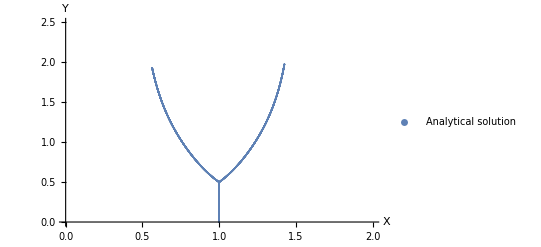

```mathematica
dx=Table[{1, 0},{6708}];
drzewo=ListPlot[biffurcationTestCoords+dx,
PlotRange->{{0,2},{0,2.5}},
PlotLegends->{"Analytical solution"},
AxesLabel->{"X","Y"}]
```

```mathematica
plotJSON[#]&/@SystemDialogInput["FileOpen"]
```

/home/oleg/dev/build/biffurcationtest.json

```mathematica
databif=OpenJSONData[];
```

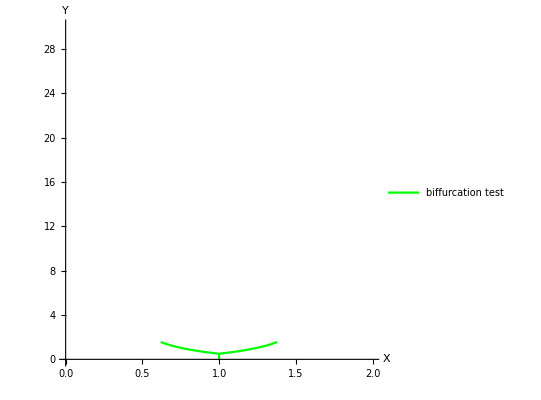

```mathematica
biftestplot=plotSimData[databif,Green,"biffurcation test"]
```

```mathematica
dx=Table[{1, 0},{6708}];
```

```mathematica
Dimensions@biffurcationTestCoords
```

{6708,2}

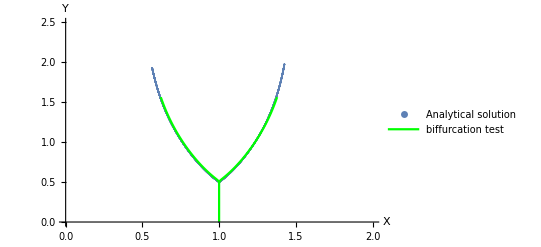

```mathematica
Show[drzewo, biftestplot]
```

# Numerical Parameters Limit

### Plot of first biffurcation point as function of ds, refinment radius, refinment fraction

#### List of json simulation files with different ds.

```mathematica
dssimdatalist=OpenJSONDialog[];
```

```mathematica
dssimdatalist//Column
```

/home/oleg/dev/build/sim_ds0.001.json
/home/oleg/dev/build/sim_ds0.0015.json
/home/oleg/dev/build/sim_ds0.002.json
/home/oleg/dev/build/sim_ds0.0025.json
/home/oleg/dev/build/sim_ds0.003.json
/home/oleg/dev/build/sim_ds0.0035.json
/home/oleg/dev/build/sim_ds0.004.json
/home/oleg/dev/build/sim_ds0.0045.json
/home/oleg/dev/build/sim_ds0.005.json
/home/oleg/dev/build/sim_ds0.0055.json
/home/oleg/dev/build/sim_ds0.006.json
/home/oleg/dev/build/sim_ds0.0065.json
/home/oleg/dev/build/sim_ds0.007.json
/home/oleg/dev/build/sim_ds0.0075.json
/home/oleg/dev/build/sim_ds0.008.json
/home/oleg/dev/build/sim_ds0.0085.json
/home/oleg/dev/build/sim_ds0.009.json
/home/oleg/dev/build/sim_ds0.0095.json
/home/oleg/dev/build/sim_ds0.01.json

```mathematica
dscoord={0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01};
```

```mathematica
dsdatalist=Import[#,"RawJSON" ]&/@dssimdatalist;
```

```mathematica
dsconvergnece = Transpose[{dscoord,#["Trees", "Branches"][[1]]["coords"][[-1,2]]&/@dsdatalist}];
```

```mathematica
fm=LinearModelFit[dsconvergnece, x, x];
```

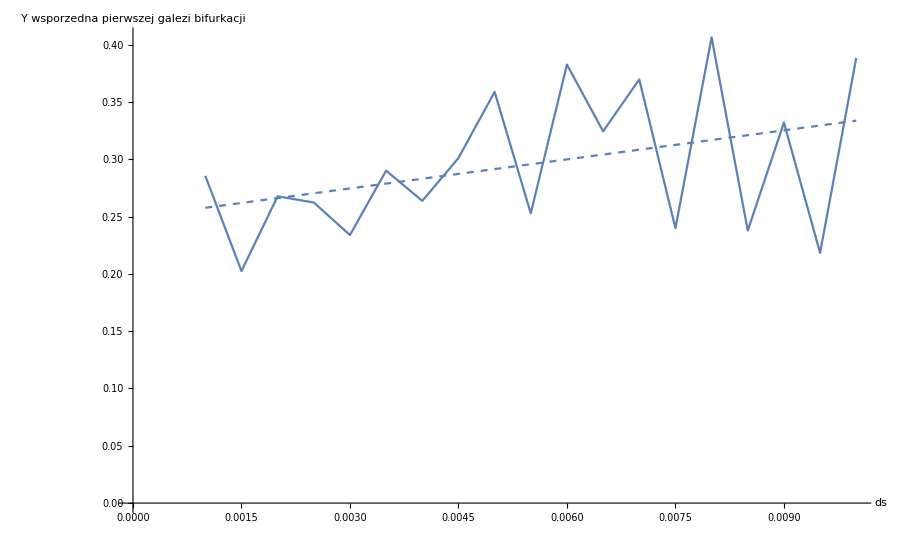

```mathematica
Show[ListPlot[dsconvergnece, Joined->True, AxesLabel->{"ds", "Y wsporzedna pierwszej galezi bifurkacji"},PlotLabel->""],Plot[fm[x],{x, 0.001, 0.01}, PlotStyle->Dashed]]
```

#### List of json simulation files with different r_refinment.

```mathematica
rrefsimdatalist=OpenJSONDialog[];
```

```mathematica
rrefsimdatalist//Column
```

/home/oleg/dev/build/sim_ref_rad_0.05.json
/home/oleg/dev/build/sim_ref_rad_0.055.json
/home/oleg/dev/build/sim_ref_rad_0.06.json
/home/oleg/dev/build/sim_ref_rad_0.065.json
/home/oleg/dev/build/sim_ref_rad_0.07.json
/home/oleg/dev/build/sim_ref_rad_0.075.json
/home/oleg/dev/build/sim_ref_rad_0.08.json
/home/oleg/dev/build/sim_ref_rad_0.085.json
/home/oleg/dev/build/sim_ref_rad_0.09.json
/home/oleg/dev/build/sim_ref_rad_0.095.json
/home/oleg/dev/build/sim_ref_rad_0.1.json
/home/oleg/dev/build/sim_ref_rad_0.2.json
/home/oleg/dev/build/sim_ref_rad_0.3.json

```mathematica
refradcoord={0.05,0.055, 0.06, 0.065, 0.07, 0.075, 0.08, 0.085, 0.09, 0.095, 0.1, 0.2, 0.3};
```

```mathematica
refraddatalist=Import[#,"RawJSON" ]&/@rrefsimdatalist;
refradconvergnece = Transpose[{refradcoord,#["Trees", "Branches"][[1]]["coords"][[-1,2]]&/@refraddatalist}];
```

```mathematica
fm=LinearModelFit[refradconvergnece[[1;;-3]], x, x];
```

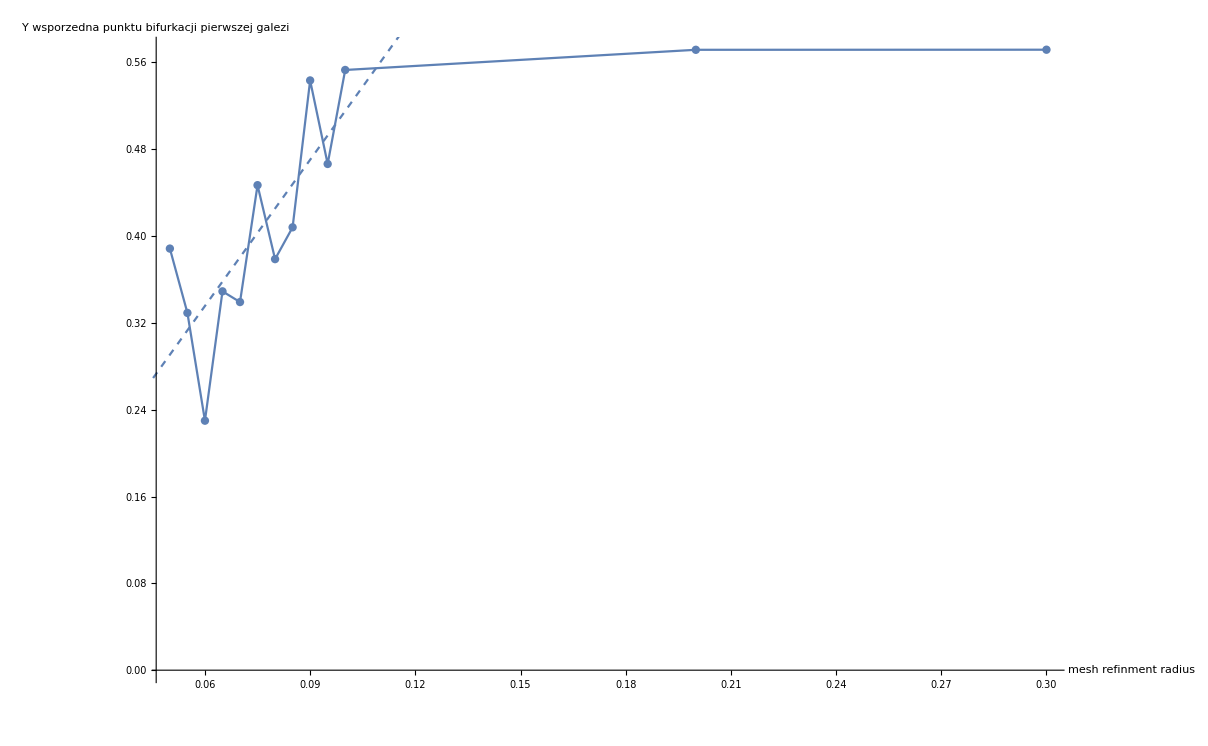

```mathematica
Show[
ListPlot[
refradconvergnece, 
Joined->True, 
AxesLabel->{"mesh refinment radius", "Y wsporzedna punktu bifurkacji pierwszej galezi"},
PlotLabel->"",
PlotRange->All,
Mesh->All],Plot[fm[x],{x, 0., 0.3}, PlotStyle->Dashed]]
```

#### List of json simulation files with different refinment-fraction parameter.

```mathematica
reffracsimdatalist=OpenJSONDialog[];
```

```mathematica
reffracsimdatalist//Column
```

/home/oleg/dev/build/sim_ref_frac_0.01.json
/home/oleg/dev/build/sim_ref_frac_0.02.json
/home/oleg/dev/build/sim_ref_frac_0.03.json
/home/oleg/dev/build/sim_ref_frac_0.04.json
/home/oleg/dev/build/sim_ref_frac_0.05.json
/home/oleg/dev/build/sim_ref_frac_0.06.json
/home/oleg/dev/build/sim_ref_frac_0.07.json
/home/oleg/dev/build/sim_ref_frac_0.08.json
/home/oleg/dev/build/sim_ref_frac_0.09.json
/home/oleg/dev/build/sim_ref_frac_0.1.json
/home/oleg/dev/build/sim_ref_frac_0.2.json
/home/oleg/dev/build/sim_ref_frac_0.3.json
/home/oleg/dev/build/sim_ref_frac_0.4.json

```mathematica
reffracvec=Join[Range[0.01, 0.1, 0.01],{0.2,0.3,0.4}];
```

```mathematica
reffracdatalist=Import[#,"RawJSON" ]&/@reffracsimdatalist;
reffracconvergnece = Transpose[{reffracvec,#["Trees", "Branches"][[1]]["coords"][[-1,2]]&/@reffracdatalist}];
```

```mathematica
fm=LinearModelFit[reffracconvergnece, x, x];
```

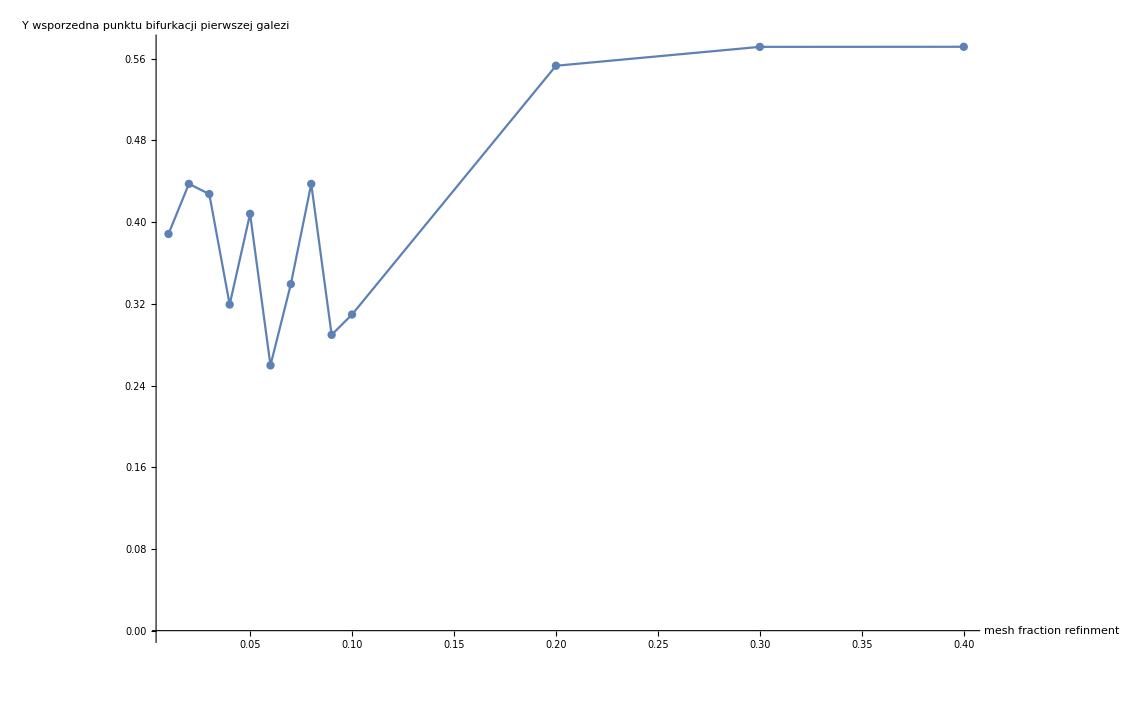

```mathematica
ListPlot[reffracconvergnece, Joined->True, Mesh->All, AxesLabel->{"mesh fraction refinment", "Y wsporzedna punktu bifurkacji pierwszej galezi"}, PlotRange->All]
```

#### Optimal parameters and ds:

```mathematica
optimallist=OpenJSONDialog[];
```

```mathematica
optimallist//Column
```

/home/oleg/dev/build/sim_optimal_ds_0.0006.json
/home/oleg/dev/build/sim_optimal_ds_0.0007.json
/home/oleg/dev/build/sim_optimal_ds_0.0008.json
/home/oleg/dev/build/sim_optimal_ds_0.0009.json
/home/oleg/dev/build/sim_optimal_ds_0.0010.json
/home/oleg/dev/build/sim_optimal_ds_0.0015.json
/home/oleg/dev/build/sim_optimal_ds_0.0020.json
/home/oleg/dev/build/sim_optimal_ds_0.0025.json
/home/oleg/dev/build/sim_optimal_ds_0.0030.json
/home/oleg/dev/build/sim_optimal_ds_0.0035.json
/home/oleg/dev/build/sim_optimal_ds_0.0040.json
/home/oleg/dev/build/sim_optimal_ds_0.0045.json
/home/oleg/dev/build/sim_optimal_ds_0.0050.json
/home/oleg/dev/build/sim_optimal_ds_0.0055.json
/home/oleg/dev/build/sim_optimal_ds_0.0060.json
/home/oleg/dev/build/sim_optimal_ds_0.0065.json
/home/oleg/dev/build/sim_optimal_ds_0.0070.json
/home/oleg/dev/build/sim_optimal_ds_0.0075.json
/home/oleg/dev/build/sim_optimal_ds_0.0080.json
/home/oleg/dev/build/sim_optimal_ds_0.0085.json
/home/oleg/dev/build/sim_optimal_ds_0.0090.json
/home/oleg/dev/build/sim_optimal_ds_0.0095.json
/home/oleg/dev/build/sim_optimal_ds_0.01.json
/home/oleg/dev/build/sim_optimal_ds_0.02.json
/home/oleg/dev/build/sim_optimal_ds_0.03.json
/home/oleg/dev/build/sim_optimal_ds_0.04.json
/home/oleg/dev/build/sim_optimal_ds_0.05.json
/home/oleg/dev/build/sim_optimal_ds_0.06.json

```mathematica
dsvalues=Join[{0.0006,0.0007,0.0008,0.0009},Range[0.001, 0.01, 0.0005],Range[0.02, 0.06, 0.01]]
```

{0.0006,0.0007,0.0008,0.0009,0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01,0.02,0.03,0.04,0.05,0.06}

```mathematica
optimaldatalist=Import[#,"RawJSON" ]&/@optimallist;
```

```mathematica
optimalconvergnece = Transpose[{dsvalues,#["Trees", "Branches"][[1]]["coords"][[-1,2]]&/@optimaldatalist}];
```

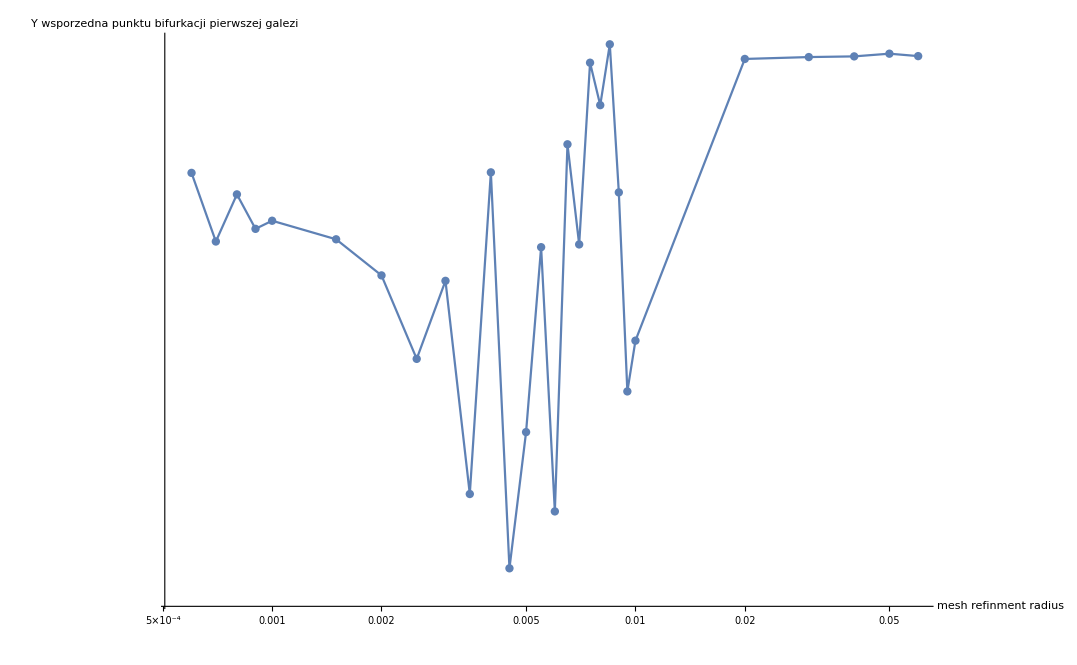

```mathematica
Show[
ListLogLogPlot[
optimalconvergnece, 
Joined->True, 
AxesLabel->{"ds", "Y wsporzedna punktu bifurkacji pierwszej galezi"},
PlotLabel->"",
PlotRange->All,
Mesh->All],
Plot[
fm[x],
{x, 0., 0.06}, 
PlotStyle->Dashed]
]
```

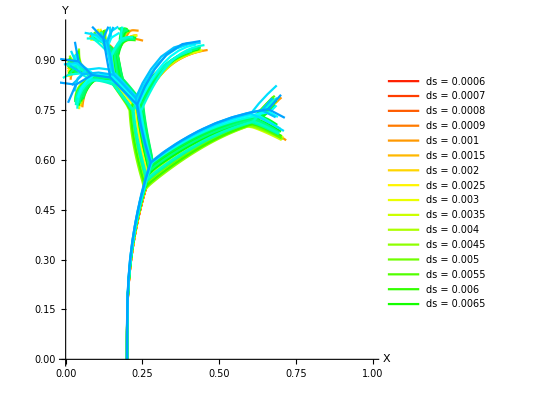

```mathematica
Show[MapThread[
plotSimData[#1,#2,#3]&,
{optimaldatalist,
Table[Hue[i*0.02],{i,1,28}],
Table[ "ds = "<>ToString[ds],{ds,dsvalues}] }]]
```

### Different values for ds.. from 0.01 to 0.001

```mathematica
differentds=OpenJSONDialog[];
```

```mathematica
differentds//Column
```

/home/oleg/dev/build/sim_ds0.001.json
/home/oleg/dev/build/sim_ds0.0015.json
/home/oleg/dev/build/sim_ds0.002.json
/home/oleg/dev/build/sim_ds0.0025.json
/home/oleg/dev/build/sim_ds0.003.json
/home/oleg/dev/build/sim_ds0.0035.json
/home/oleg/dev/build/sim_ds0.004.json
/home/oleg/dev/build/sim_ds0.0045.json
/home/oleg/dev/build/sim_ds0.005.json
/home/oleg/dev/build/sim_ds0.0055.json
/home/oleg/dev/build/sim_ds0.006.json
/home/oleg/dev/build/sim_ds0.0065.json
/home/oleg/dev/build/sim_ds0.007.json
/home/oleg/dev/build/sim_ds0.0075.json
/home/oleg/dev/build/sim_ds0.008.json
/home/oleg/dev/build/sim_ds0.0085.json
/home/oleg/dev/build/sim_ds0.009.json
/home/oleg/dev/build/sim_ds0.0095.json
/home/oleg/dev/build/sim_ds0.01.json

```mathematica
dsvalues=Range[0.001, 0.01, 0.0005]
```

{0.001,0.0015,0.002,0.0025,0.003,0.0035,0.004,0.0045,0.005,0.0055,0.006,0.0065,0.007,0.0075,0.008,0.0085,0.009,0.0095,0.01}

```mathematica
colors=Table[Hue[i*0.03],{i,1,Length[dsvalues]}];
```

```mathematica
data=Import[#,"RawJSON"]&/@differentds;
```

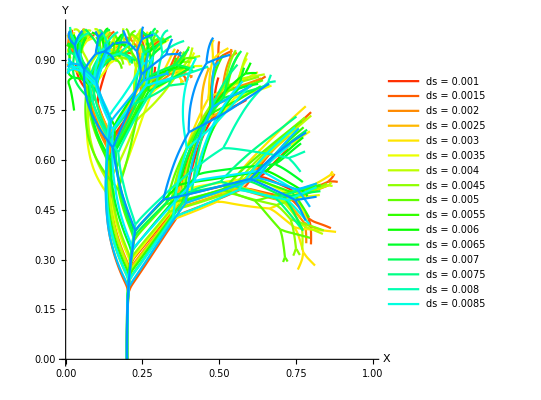

```mathematica
Show[MapThread[plotSimData[#1, #2, #3]&,{data,colors,Table["ds = "<>ToString[ds],{ds,dsvalues}]}]]
```

#### Few smalles(best) ds values. As you can see they are very close to each other

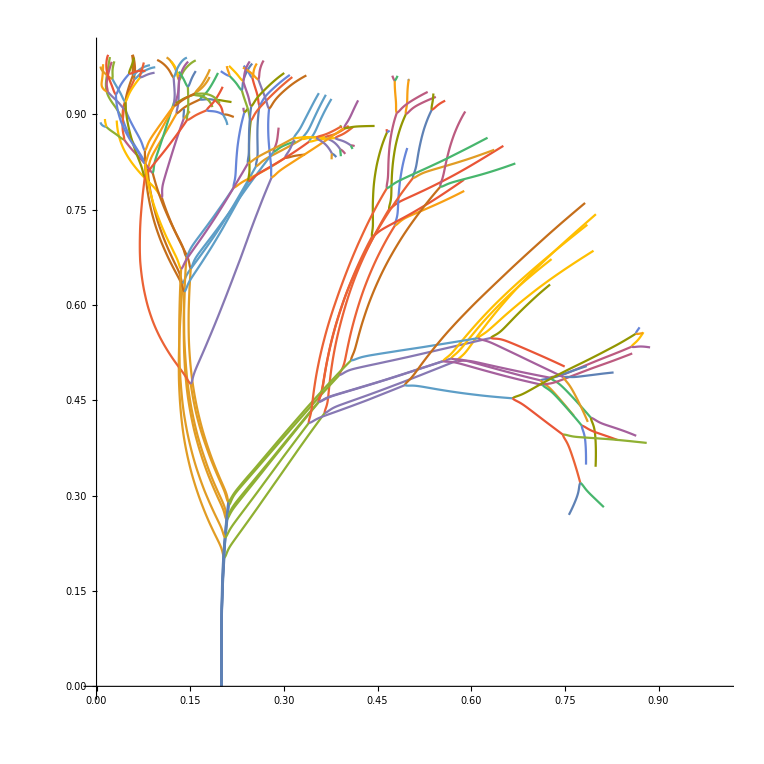

```mathematica
Show[plotJSON[#]&/@SystemDialogInput["FileOpen"]]
```

### Different mesh refinment values from 0.05 to 0.3

```mathematica
differentref=OpenJSONDialog[];
differentref//Column
```

/home/oleg/dev/build/sim_ref_rad_0.05.json
/home/oleg/dev/build/sim_ref_rad_0.055.json
/home/oleg/dev/build/sim_ref_rad_0.06.json
/home/oleg/dev/build/sim_ref_rad_0.065.json
/home/oleg/dev/build/sim_ref_rad_0.07.json
/home/oleg/dev/build/sim_ref_rad_0.075.json
/home/oleg/dev/build/sim_ref_rad_0.08.json
/home/oleg/dev/build/sim_ref_rad_0.085.json
/home/oleg/dev/build/sim_ref_rad_0.09.json
/home/oleg/dev/build/sim_ref_rad_0.095.json
/home/oleg/dev/build/sim_ref_rad_0.1.json
/home/oleg/dev/build/sim_ref_rad_0.2.json
/home/oleg/dev/build/sim_ref_rad_0.3.json

```mathematica
values=Join[Range[0.05, 0.1, 0.005],{0.2,0.3}]
```

{0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.2,0.3}

```mathematica
colors=Table[Hue[i*0.05],{i,1,Length[values]}];
```

```mathematica
data=Import[#,"RawJSON"]&/@differentref;
```

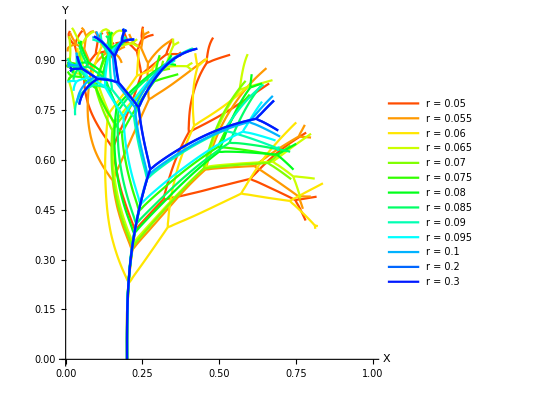

```mathematica
Show[MapThread[plotSimData[#1, #2, #3]&,{data,colors,Table["r = "<>ToString[ds],{ds,values}]}]]
```

### Mesh refinment fraction from 0.01 to 0.3

```mathematica
differentfrac=OpenJSONDialog[];
```

```mathematica
differentfrac//Column
```

/home/oleg/dev/build/sim_ref_frac_0.01.json
/home/oleg/dev/build/sim_ref_frac_0.02.json
/home/oleg/dev/build/sim_ref_frac_0.03.json
/home/oleg/dev/build/sim_ref_frac_0.04.json
/home/oleg/dev/build/sim_ref_frac_0.05.json
/home/oleg/dev/build/sim_ref_frac_0.06.json
/home/oleg/dev/build/sim_ref_frac_0.07.json
/home/oleg/dev/build/sim_ref_frac_0.08.json
/home/oleg/dev/build/sim_ref_frac_0.09.json
/home/oleg/dev/build/sim_ref_frac_0.1.json
/home/oleg/dev/build/sim_ref_frac_0.2.json
/home/oleg/dev/build/sim_ref_frac_0.3.json
/home/oleg/dev/build/sim_ref_frac_0.4.json

```mathematica
values=Join[Range[0.01,0.1, 0.01],{0.2,0.3,0.4}]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4}

```mathematica
colors=Table[Hue[i*0.05],{i,1,Length[values]}];
```

```mathematica
data=Import[#,"RawJSON"]&/@differentfrac;
```

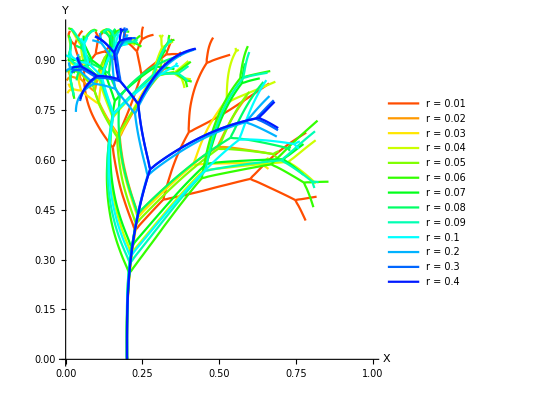

```mathematica
Show[MapThread[plotSimData[#1, #2, #3]&,{data,colors,Table["r = "<>ToString[ds],{ds,values}]}]]
```

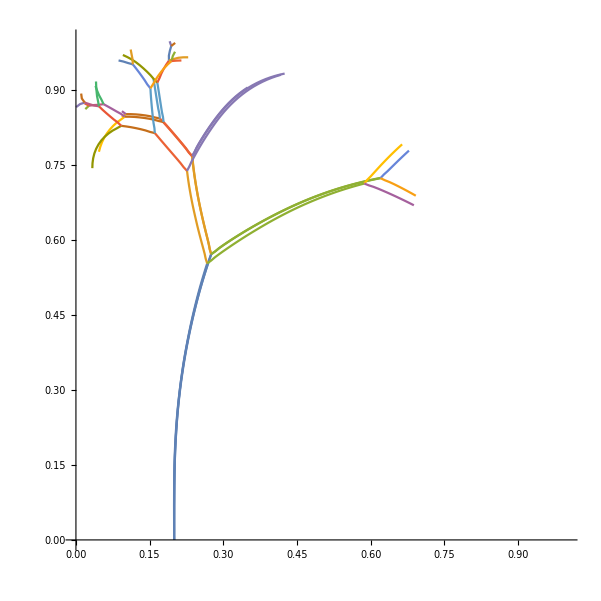

```mathematica
Show[plotJSON[#]&/@SystemDialogInput["FileOpen"]]
```

# Windows

```mathematica
RunProcess
```

```mathematica
riversimp = StartProcess[{"wsl","/home/oleg/dev/build/source/riversim"}]
```

ProcessObject[…]

```mathematica
ProcessConnection[riversimp ,"stream"]
```

ProcessConnection[ProcessObject[…],stream]

```mathematica
ReadLine[riversimp]
```

```mathematica
RunProcess[{"wsl","/home/oleg/dev/build/source/riversim","-n","2"}]
```

<|ExitCode→0,StandardOutput→
     _)                    _)           
  __| |\ \   / _ \  __| __| | __ `__ \  
 |    | \ \ /  __/ |  \__ \ | |   |   | 
_|   _|  \_/ \___|_|  ____/_|_|  _|  _| 

-------
  0
-------
   Number of active cells:       3714
   Number of degrees of freedom: 15057
   Number of active cells:       3828
   Number of degrees of freedom: 15625
   Number of active cells:       3945
   Number of degrees of freedom: 16209
a3/a1 = 102.517, bif thr = -0.1 a1 = 0.0189084, bif thr = 0.002
-------
  1
-------
   Number of active cells:       5883
   Number of degrees of freedom: 23747
   Number of active cells:       6060
   Number of degrees of freedom: 24575
   Number of active cells:       6243
   Number of degrees of freedom: 25525
a3/a1 = 61.8291, bif thr = -0.1 a1 = 0.0261518, bif thr = 0.002
,StandardError→|>

```mathematica
RunProcess[{"wsl","/home/oleg/dev/build/source/riversim","-n","2","--simulation-type=1"}]
```

<|ExitCode→0,StandardOutput→
     _)                    _)           
  __| |\ \   / _ \  __| __| | __ `__ \  
 |    | \ \ /  __/ |  \__ \ | |   |   | 
_|   _|  \_/ \___|_|  ____/_|_|  _|  _| 

,StandardError→|>

# Automatic parameters lookup

```mathematica
Clear["*"]
```

```mathematica
RunTestSimulation[modelParams_:ModelJSONStructure[],outputName_:"test", linuxDir_:"/mnt/c/users/ofcra/dev/riversim/build/", windowsDir_:"C:/Users/ofcra/dev/riversim/build/"]:=Module[{
riversimPath= linuxDir<>"source/riversim",
windowsJSONPath = windowsDir<>"mathematica_model_params.json",
linuxJSONPath = linuxDir<>"mathematica_model_params.json",
importWindowsJSONPath = windowsDir<>outputName<>".json",
log},
Export[
windowsJSONPath,
modelParams
];
log=RunProcess[{
"wsl",
riversimPath,
"-o",outputName,
"-t",2,
linuxJSONPath},
ProcessDirectory->windowsDir
];
Append[Import[importWindowsJSONPath,"RawJSON"],log]
];
```

```mathematica
data=RunTestSimulation[]
```

<|Border→<|SomeDetails→points and lines should be in counterclockwise order!,SourceIds→{{1,4}},coords→{{1.,0.},{1.,1.},{0.,1.},{0.,0.},{0.2,0.}},lines→{{0,1,4},{1,2,4},{2,3,4},{3,4,4},{4,0,4}}|>,Description→This is RiverSim simulation data,GeometryDifference→<|AlongBranches→{{1,{{0.0343932},{0.000419722},{0.0901882},{0.0464388},{0.0877448}}}},BiffuractionPoints→{},description→this structure holds info about backward river simulation.|>,Model→<|Integration→<|exponant→3.,radius→0.03,weightRadius→0.02|>,Mesh→<|eps→1,exponant→3.,maxArea→10.,minAngle→32.,minArea→1,refinmentRadius→0.2|>,Solver→<|quadratureDegree→3,refinmentFraction→0.1,refinmentSteps→3|>,biffurcationAngle→0.628319,biffurcationMinDistance→0.07,biffurcationThreshold→-0.2,biffurcationThreshold2→0.0001,biffurcationType→0,boundaryCondition→0,boundaryIds→{1,2,3,4},ds→0.005,dx→0.2,eta→0.,fieldValue→1.,growthMinDistance→0.03,growthThreshold→0,growthType→0,height→1.,riverBoundaryId→4,width→1.|>,RuntimeInfo→<|EachCycleTime→{0.546875},EndDate→Mon May 20 02:27:41 2019
,InputFile→,StartDate→Mon May 20 02:27:40 2019
,TotalTime→0.546875|>,Trees→<|Branches→{<|coords→{{0.2,0.},{0.2,0.1}},id→1,sourceAngle→1.5708,sourcePoint→{0.2,0.}|>},Relations→{},SourceIds→{1}|>,Version→2.0.1,ExitCode→0,StandardOutput→
     _)                    _)           
  __| |\ \   / _ \  __| __| | __ `__ \  
 |    | \ \ /  __/ |  \__ \ | |   |   | 
_|   _|  \_/ \___|_|  ____/_|_|  _|  _| 

-------------------------
Series parameters testing
-------------------------
   Number of active cells:       1224
   Number of degrees of freedom: 5005
   Number of active cells:       1593
   Number of degrees of freedom: 6671
   Number of active cells:       2073
   Number of degrees of freedom: 8923
,StandardError→|>

```mathematica
data["GeometryDifference"]["AlongBranches"][[1,2,All,1]]
```

{0.0343932,0.000419722,0.0901882,0.0464388,0.0877448}

```mathematica
data["StandardOutput"]
```

_)                    _)           
  __| |\ \   / _ \  __| __| | __ `__ \  
 |    | \ \ /  __/ |  \__ \ | |   |   | 
_|   _|  \_/ \___|_|  ____/_|_|  _|  _| 

-------------------------
Series parameters testing
-------------------------
   Number of active cells:       1224
   Number of degrees of freedom: 5005
   Number of active cells:       1593
   Number of degrees of freedom: 6671
   Number of active cells:       2073
   Number of degrees of freedom: 8923

## Let also update mesh refinement.

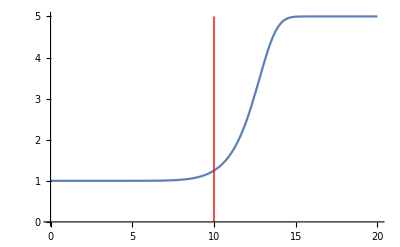

```mathematica
min=1;
max=5;
r0=10;
exp=10;
sigma=2;
Plot[(max-min)*(1-Exp[-1/(2 sigma^2) (r/r0)^exp])/(1+Exp[-1/(2 sigma^2)(r/r0)^exp])+min,{r,0,2 r0},PlotRange->{{0,2 r0},{0,max}},Epilog->{Red,Line[{{r0,0},{r0,max}}]}]
```